# Reinforcement learning via single-photon quantum walks

Fulvio Flamini^1, Marius Krumm^1, Lukas J. Fiderer^1, Thomas Müller^2, Hans J. Briegel^1
^1Institut für Theoretische Physik, Universität Innsbruck, Technikerstraße 21a,  A - 6020 Innsbruck, Austria.
^2Department of Philosophy, University of Konstanz, Universitätsstrasse 10, 78464 Konstanz, Germany.

Licensed under the Apache License, Version 2.0 (the "License");
you may not use this file except in compliance with the License.
You may obtain a copy of the License at

https : // www.apache.org/licenses/LICENSE - 2.0
 
Unless required by applicable law or agreed to in writing, software distributed under the License is distributed on an "AS IS" BASIS,
WITHOUT WARRANTIES OR CONDITIONS OF ANY KIND, either express or implied.
See the License for the specific language governing permissions and limitations under the License.

## Functions

#### Import

```mathematica
myPATHexport="...";
myPATHimport="...";
```

DIM=dimension of the circuits;

allLeakingNodes < anyLayout > [[DIM]]  has the following format:
	Table[
		findLeakingNodes[DIM,  graphINFO,  inMode,  outMode]
			, {inMode, DIM}, {outMode, DIM}]

#### Some functions

```mathematica
Off[CompiledFunction::cfsa];
```

```mathematica
(* Takes as input a real number x0 (describing a phase or a transmissivity) and outputs a new value with a gaussian imperfection sigma. *)
gaussianError[x0_,sigma_]:= RandomVariate[NormalDistribution[x0, sigma]];





HaarUnitary[sizeU_Integer]:=RandomVariate[CircularUnitaryMatrixDistribution[sizeU]];




(* Fidelity used by Clements et al. *)
fidelity[U_,Uexp_]:=Abs[Tr[ConjugateTranspose[U].Uexp]/(√(Length@U Tr[ConjugateTranspose[Uexp].Uexp]))]^2;



(* Total Variation Distance between two probability distributions A and B. *)
TVD[A_,B_]:=1/2 Total@Abs[A-B];



(* Fancy way to do the square modulus of a number with simplification for symbolic expressions. Stolen from the internet. *)
abs2[z_]:= ComplexExpand[Abs[z]^2, TargetFunctions ->{Conjugate}];




(* Evaluates the permanent of a (sub)matrix. It will be useful for future analyses with multiphoton experiments. *)
per[matrix_List]:= With[{v = Array[x, Length[matrix]]}, Coefficient[Times@@(matrix.v),Times@@v]];





(* Evaluates the transition probability from input cols to output rows for INDistinguishable photons. *)
probIND[matrix_,rows_,cols_]:=(abs2@Permanent@matrix⟦rows,cols⟧)/(Times@@(Tally[rows]⟦;;,2⟧!)Times@@(Tally[cols]⟦;;,2⟧!)); 



(* Evaluates the transition probability from input cols to output rows for DIStinguishable photons. *)
probDIS[matrix_,rows_,cols_]:=Permanent[abs2@matrix⟦rows,cols⟧]/(Times@@(Tally[cols]⟦;;,2⟧!));



(* Used for plotting. *)
barChart3D[matrix_,imageSize_:Automatic]:=Graphics3D[{
Table[
{ColorData["TemperatureMap"][matrix[[i,j]]],
Cuboid[{i-1/2,j-1/2,0},{i+1/2,j+1/2,matrix[[i,j]]}]},
{i,Length@matrix},{j,Length@matrix[[1,All]]}
]},
ImageSize->imageSize
];



BScount[m_Integer]:=(m(m-1))/2;
```

```mathematica
(* MZ with Gaussian noise on the phase and the amplitude transmissivity. Noise levels can be different. *)
noisyMZ[ϕ_,noiseLevelBS_,noiseLevelPS_]:=Module[{t1=gaussianError[1/√2,noiseLevelBS],t2=gaussianError[1/√2,noiseLevelBS],noisyϕ=gaussianError[ϕ,noiseLevelPS],noisyMZ},
Return[{
{ⅈ ⅇ^(-ⅈ noisyϕ) (-t1 t2+ⅇ^(2 ⅈ noisyϕ) √(1-t1^2) √(1-t2^2)),ⅇ^(-ⅈ noisyϕ) √(1-t1^2) t2+ⅇ^(ⅈ noisyϕ) t1 √(1-t2^2)},
{ⅇ^(ⅈ noisyϕ) √(1-t1^2) t2+ⅇ^(-ⅈ noisyϕ) t1 √(1-t2^2),ⅈ ⅇ^(-ⅈ noisyϕ) (-ⅇ^(2 ⅈ noisyϕ) t1 t2+√(1-t1^2) √(1-t2^2))}
}]
];


(* Ideal MZ with arbitrary amplitude transmissivities. Equivalent to noisyMZ for negligible levels of noise. *)
MZ[ϕ_,t1_,t2_]:=Module[{},
Return[{
{ⅈ ⅇ^(-ⅈ ϕ) (-t1 t2+ⅇ^(2 ⅈ ϕ) √(1-t1^2) √(1-t2^2)),ⅇ^(-ⅈ ϕ) √(1-t1^2) t2+ⅇ^(ⅈ ϕ) t1 √(1-t2^2)},
{ⅇ^(ⅈ ϕ) √(1-t1^2) t2+ⅇ^(-ⅈ ϕ) t1 √(1-t2^2),ⅈ ⅇ^(-ⅈ ϕ) (-ⅇ^(2 ⅈ ϕ) t1 t2+√(1-t1^2) √(1-t2^2))}
}]
];


(* Ideal MZ with 50:50 beamsplitters. *)
MZideal[ϕ_]:=({{-Sin[ϕ], Cos[ϕ]}, {Cos[ϕ], Sin[ϕ]}});(*FullSimplify[-I/2({{1, ⅈ}, {ⅈ, 1}}).({{ⅇ^(-ⅈ ϕ), 0}, {0, ⅇ^(ⅈ ϕ)}}).({{1, ⅈ}, {ⅈ, 1}})]*)
```

#### Canonical decompositions of U

```mathematica
unitaryDecomposition[unitary_,method_]:=Which[
method⟦2⟧=="Square",SquareDecomposition[unitary],
method⟦2⟧=="Triangular",TriangularDecomposition[unitary],
method⟦2⟧=="Square2PS",Square2PSDecomposition[unitary](* Square decomposition where tunable beamsplitters are implemented as tunable MZI. *)
];




(*################################# START Triangular #################################*)


(* Returns all parameters (θ,ψ) describing the MZIs that build up the unitary transformation, using the Triangular decomposition by Reck et al. *)

TriangularDecomposition[unitary_]:=
Block[{vecPara,cont=1,paraReversed,m=Length@unitary,tmp1,tmp2,u1,u2,θ,ψ,diag,u=unitary (* Do not remove this assignment *),i,j,listParameters},
vecPara=ConstantArray[0.,BScount@m];

For[i=m,i>1,i--,
For[j=1,j≤i-1,j++,

u1=u⟦i,j⟧;
u2=u⟦i,j+1⟧;
ψ=-arg@u2+arg@u1;
θ=Chop@arcTanT[ψ,u1+10^-16,u2+10^-16];
vecPara⟦cont⟧={θ,ψ};

tmp1=colReplace1[θ,u⟦#,j⟧,u⟦#,j+1⟧,ψ]&/@Range@m;
tmp2=colReplace2[θ,u⟦#,j⟧,u⟦#,j+1⟧,ψ]&/@Range@m;
u⟦;;,j⟧=tmp1;
u⟦;;,j+1⟧=tmp2;
cont++
]
];

paraReversed=Reverse@vecPara;
diag=Chop[Arg/@(Diagonal@u)];
listParameters=PrependTo[paraReversed,diag]//N;
Return@listParameters

];


(*################################# END Triangular #################################*)






(*################################## START Square ################################*)


(* Returns all parameters (θ,ψ) describing the MZIs that build up the unitary transformation, using the Square decomposition by Clements et al. *)

SquareDecomposition[unitary_]:=Block[{dim=Length@unitary,Utemp=unitary,TinvPara,Tpara,cont1=1,cont2=1,tmp,i,j,k,u1,u2,tmp1,tmp2,tmp3,diag,bs,ph,listBS,paraBS,pos},
TinvPara=ConstantArray[0.,∑_(i=0)^(Floor[dim/2]-1) (2i+1)];
Tpara=ConstantArray[0.,∑_(i=0)^(Ceiling[dim/2]-1) (2i)];

For[i=1,i<dim,i++,

If[OddQ@i,
For[j=0,j≤i-1,j++,
k=i-j;
u1=Utemp⟦dim-j,k⟧;
u2=Utemp⟦dim-j,k+1⟧;
ph=ph=-arg@u2+arg@u1;
bs=Chop@arcTanT[ph,u1+10^-16,u2+10^-16]; 
TinvPara⟦cont1⟧={bs,ph};

tmp1=colReplace1[bs,Utemp⟦#,k⟧,Utemp⟦#,k+1⟧,ph]&/@Range@dim;
tmp2=colReplace2[bs,Utemp⟦#,k⟧,Utemp⟦#,k+1⟧,ph]&/@Range@dim;
Utemp⟦;;,k⟧=tmp1;
Utemp⟦;;,k+1⟧=tmp2;
cont1++
],

For[j=0,j≤i-1,j++,
k=dim+j-i;
u1=Utemp⟦k,j+1⟧;
u2=Utemp⟦k+1,j+1⟧;
ph=-arg@u1+arg@u2;
bs=-Chop@arcTanT[ph,u2+10^-16,u1+10^-16];
Tpara⟦cont2⟧={bs,ph};

tmp1=rowReplace1[bs,Utemp⟦k,#⟧,Utemp⟦k+1,#⟧,ph]&/@Range@dim;
tmp2=rowReplace2[bs,Utemp⟦k,#⟧,Utemp⟦k+1,#⟧,ph]&/@Range@dim;
Utemp⟦k⟧=tmp1;
Utemp⟦k+1⟧=tmp2;
cont2++
]
];
];

listBS=generateListBSsquare[dim];
diag=Arg/@Chop[Diagonal@Utemp];

(* Now we move the diagonal matrix from the center to the first (last to act) position. *)
For[i=Length@Tpara,i≥1,i--,
pos=listBS⟦i⟧;
tmp3=diag⟦pos+1⟧;
diag⟦pos+1⟧=diag⟦pos⟧+Tpara⟦i,2⟧;
Tpara⟦i,2⟧=diag⟦pos⟧-tmp3
];

paraBS=Join[Tpara,Reverse@TinvPara];
Return[#&/@PrependTo[paraBS,diag]]

];

(*################################# END Square #################################*)





Square2PSDecomposition[unitary_,square2PSinit_]:=Block[{cellPositions,nBSinLayers,pos2take,DIM=Length@unitary,θlayers,ψlayers,parameters,phases},
{cellPositions,nBSinLayers,pos2take}=square2PSinit⟦DIM,;;3⟧;
parameters=Chop@unitaryDecomposition[unitary,Method->"Square"];

{θlayers,ψlayers}=TakeList[(parameters)⟦2;;,#⟧⟦pos2take⟧,nBSinLayers]&/@{1,2};
phases=Riffle[-ψlayers,2θlayers];
Return@{parameters⟦1⟧,phases}
];
```

```mathematica
(* Compiled functions to speed up the unitary decompositions. *)

expI=Compile[{{x,_Real}},ⅇ^(ⅈ x),RuntimeOptions->"Speed"];

arcTanT=Compile[{{a,_Real},{b,_Complex},{c,_Complex}},ArcTan[expI[-a]b,c],RuntimeOptions->"Speed"];

arg=Compile[{{x,_Complex}},Arg@x,RuntimeOptions->"Speed"];

rowReplace1=Compile[{{a1,_Real},{b1,_Complex},{c1,_Complex},{d1,_Real}},-Sin[a1]b1+ⅇ^(-ⅈ d1)Cos[a1]c1,RuntimeOptions->"Speed"];
rowReplace2=Compile[{{a2,_Real},{b2,_Complex},{c2,_Complex},{d2,_Real}},Cos[a2]b2+ⅇ^(-ⅈ d2)Sin[a2] c2,RuntimeOptions->"Speed"];

colReplace1=Compile[{{a1,_Real},{b1,_Complex},{c1,_Complex},{d1,_Real}},-Sin[a1]b1+ⅇ^(ⅈ d1)Cos[a1]c1,RuntimeOptions->"Speed"];
colReplace2=Compile[{{a2,_Real},{b2,_Complex},{c2,_Complex},{d2,_Real}},Cos[a2]b2+ⅇ^(ⅈ d2)Sin[a2] c2,RuntimeOptions->"Speed"];

rowReplaceNoise1=Compile[{{MZ1,_Complex},{MZ2,_Complex},{u1,_Complex},{u2,_Complex},{ϕ,_Real},{loss,_Real}},loss(MZ1 u1+ⅇ^(-I ϕ)MZ2 u2),RuntimeOptions->"Speed"];
rowReplaceNoise2=Compile[{{MZ3,_Complex},{MZ4,_Complex},{u1,_Complex},{u2,_Complex},{ϕ,_Real},{loss,_Real}},loss(MZ3 u1+ⅇ^(-I ϕ)MZ4 u2),RuntimeOptions->"Speed"];
```

```mathematica
(*Returns a list with the label of the 1st mode of the MZI, using the order induced by the decompositions. The last MZI given by this list is the first MZI to act.*)
generateListBS[method_,dim_]:=generateListBS[method,dim]=Which[
method⟦2⟧=="Square",generateListBSsquare[dim],
method⟦2⟧=="Triangular",generateListBStriangular[dim]
];



(* See generateListBS[] *)
generateListBSsquare[dim_Integer]:=generateListBSsquare[dim]=Block[{cont1=1,cont2=1,i,j,listBStinv=ConstantArray[0.,∑_(i=0)^(Floor[dim/2]-1) (2i+1)],listBSt=ConstantArray[0.,∑_(i=0)^(Ceiling[dim/2]-1) (2i)]},
For[i=1,i<dim,i++,
If[OddQ@i,
For[j=0,j≤i-1,j++,listBStinv⟦cont1++⟧={i-j}],
For[j=0,j≤i-1,j++,listBSt⟦cont2++⟧={dim+j-i}]
];
];
Flatten@Join[listBSt,Reverse@listBStinv]
];



(* See generateListBS[] *)
generateListBStriangular[dim_Integer]:=generateListBStriangular[dim]=Reverse[Flatten[Table[i,{k,dim-1},{i,dim-k}]] ];




(*################################## START Recomposition ################################*)

(* Constructs a unitary matrix by multiplying a sequence of Givens rotations, given by the list of parameters provided by the two decompositions. *)
(* It works with both numeric and symbolic values. *)
(* It supports both lossless and lossy implementations. All analyses in this file consider lossless scenarios. *)
(* It supports both noiseless and noisy implementations. *)

getUfromParameters[opt_,parametersList_,noiseLevelBSandPS_:0,transmissivity_:"Lossless"]:= 
Block[{m=Length@parametersList⟦1⟧,diag,i,k,p,pStep,bs,nBS,θPara,ψPara,γPara,τ,MZidealK,BSinMZidealϕ,noiseLevelBS,noiseLevelPS,listBS,MZk,start,tmp1,tmp2,cellPositions,nBSinLayers,pos2take,cellsUpara,newU,DIM},


If[opt⟦2⟧=="Square2PS",
DIM=(parametersList⟦2⟧//Length)/2;
{cellPositions,nBSinLayers,pos2take}=square2PSinit⟦DIM⟧⟦;;3⟧;
cellsUpara=Table[Join[#⟦s,k⟧,{1,parametersList⟦2,s,k⟧}],{s,Length@#},{k,Length[#⟦s⟧]}]&@cellPositions;
diag=DiagonalMatrix[expI@parametersList⟦1⟧];
newU=diag.Dot@@Reverse@Table[Normal@chipLayer[DIM,cellsUpara,layer],{layer,Length@cellsUpara}];
Return[newU]
];


If[ListQ[opt⟦2⟧],(*If we input the list of Mach-Zehnders, given by one of the two decompositions.*)
listBS=opt⟦2⟧,
Which[(*Otherwise, consider one of the two decompositions.*)
opt⟦2⟧=="Square",listBS=generateListBS[opt,m],
opt⟦2⟧=="Triangular",listBS=generateListBS[opt,m]
]
];

nBS=BScount@m;(*How many MZ*)

τ=Which[(*The analyses reported in this file assume lossless implementations. Lossy circuits can be studied by just setting a value for the transmissivity.*)
transmissivity=="Lossless",1,
True,√transmissivity
];

If[Length@noiseLevelBSandPS>0,

noiseLevelBS=noiseLevelBSandPS⟦1⟧;(* Controls the amount of Gaussian noise on the phase inside the MZs *)
noiseLevelPS=noiseLevelBSandPS⟦2⟧;(* Controls the amount of Gaussian noise on the phase outside the MZs *)

θPara=parametersList⟦2;;,1⟧;(* Phases inside the MZ interferometers *)
ψPara=gaussianError[#,noiseLevelPS]&/@parametersList⟦2;;,2⟧;(* Phases outside the MZ interferometers *)
γPara=gaussianError[#,noiseLevelPS]&/@parametersList⟦1⟧;(* Phases of the diagonal matrix *)

MZk=Table[noisyMZ[θPara⟦k⟧,noiseLevelBS,noiseLevelPS],{k,nBS}],

θPara=parametersList⟦2;;,1⟧;(* Phases inside the MZs *)
ψPara=parametersList⟦2;;,2⟧;(* Phases outside the MZs *)
γPara=parametersList⟦1⟧(* Phases of the diagonal matrix *)
];

diag=DiagonalMatrix[Table[expI[γPara⟦k⟧],{k,m}]];

start=IdentityMatrix@m;


If[Length@noiseLevelBSandPS>0,
Do[
pStep=listBS[[i]];
tmp1=rowReplaceNoise1[MZk⟦i,1,1⟧,MZk⟦i,1,2⟧,start⟦pStep,#⟧,start⟦pStep+1,#⟧,ψPara⟦i⟧,τ]&/@Range@m;
tmp2=rowReplaceNoise2[MZk⟦i,2,1⟧,MZk⟦i,2,2⟧,start⟦pStep,#⟧,start⟦pStep+1,#⟧,ψPara⟦i⟧,τ]&/@Range@m;
start⟦pStep⟧=tmp1;
start⟦pStep+1⟧=tmp2;
,{i,nBS,1,-1}
],
Do[
pStep=listBS[[i]];
tmp1=rowReplace1[θPara⟦i⟧,τ start⟦pStep,#⟧,τ start⟦pStep+1,#⟧,ψPara⟦i⟧]&/@Range@m;
tmp2=rowReplace2[θPara⟦i⟧,τ start⟦pStep,#⟧,τ start⟦pStep+1,#⟧,ψPara⟦i⟧]&/@Range@m;
start⟦pStep⟧=tmp1;
start⟦pStep+1⟧=tmp2;
,{i,nBS,1,-1}
]
];(*Multiplied in reversed order*)

Return[diag.start]

];

(*################################## END Recomposition ################################*)
```

Examples with unitary decompositions

```mathematica
U=N@HaarUnitary[15];

Print[Style["\nIdeal",Bold,16]];
Timing[parameters=Chop@unitaryDecomposition[U,Method->"Square"];]
Timing[outcome=getUfromParameters[Method-> "Square",parameters];]
Chop[U-outcome,10^-5]//MatrixForm

Print[Style["\nNoisy",Bold,16]];
Timing[parameters=Chop@unitaryDecomposition[U,Method->"Square"];]
Timing[outcome=getUfromParameters[Method-> "Square",parameters,{0.00005,0.00001},1];]
Chop[U-outcome,10^-5]//MatrixForm

Print[Style["\nNoisy and Lossy",Bold,16]];
Timing[parameters=Chop@unitaryDecomposition[U,Method->"Square"];]
Timing[outcome=getUfromParameters[Method-> "Square",parameters,{10^-6,10^-6},0.9999];]
Chop[U-outcome,10^-5]//MatrixForm
```

Ideal scenario

{0.,Null}

{0.,Null}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Noisy scenario

{0.,Null}

{0.,Null}

(-0.0000709483 | 0.0000446699+0.000124496 ⅈ | -0.000121473+0.0000851909 ⅈ | -0.0000803697+0.000231893 ⅈ | -0.0000114134+0.0000709575 ⅈ | -0.0000309755+0.0000260653 ⅈ | -0.000012754-0.0000694138 ⅈ | 0.000136368+0.0000366013 ⅈ | 0.0000383747-0.000014151 ⅈ | -0.0000506975+0.0000184661 ⅈ | 0.+0.000039644 ⅈ | -0.000109138+0.0000542539 ⅈ | -0.0000648755 | -0.0000824501 | 0.0000935064
-0.0000299547 | -0.0000848297 | -0.000172247+0.0000521788 ⅈ | 0.000127171-0.0000566167 ⅈ | 0.000104902-0.00007761 ⅈ | 0.0000237534+0.0000460855 ⅈ | -0.000111142+0.0000403918 ⅈ | -0.0000711537+0.0000565637 ⅈ | -0.0000885171+0.0000521762 ⅈ | -0.0000432749+0.0000583432 ⅈ | -0.000117579+0.0000457902 ⅈ | 0.0000211363 | 0.000013237-0.0000772206 ⅈ | -0.0000209393+0.0000355488 ⅈ | -0.0000562572+0.0000414552 ⅈ
-0.0000473651-0.0000338095 ⅈ | -0.000143221-0.0000273496 ⅈ | 0.0000307185-0.0000145507 ⅈ | -0.0000994241+0.0000159341 ⅈ | -0.0000599223-0.0000550708 ⅈ | -0.0000624701+0.000136494 ⅈ | 0.000121709-0.0000506983 ⅈ | -0.0000791058+0.0000833044 ⅈ | -0.0000194532-0.0000123697 ⅈ | -0.0000855675-0.0000568895 ⅈ | 0.0000936047+0.000051267 ⅈ | 0.0000223792-0.0000244883 ⅈ | -0.0000541009+0.0000103252 ⅈ | 0.-0.0000545818 ⅈ | -0.0000132042-0.0000510062 ⅈ
0.000019957-0.0000564027 ⅈ | -0.000153557+0.0000658572 ⅈ | -0.0000167186-0.0000284364 ⅈ | -0.0000291602-0.0000488117 ⅈ | -0.0000108648 | 0.-0.0000769273 ⅈ | -0.0000237404-0.0000290399 ⅈ | -0.0000107614 | 0.0000645967 | 0.+0.0000278343 ⅈ | 0.0000411017-0.0000677305 ⅈ | 0.0000927543+0.0000392435 ⅈ | 0.0000662342+0.0000610251 ⅈ | 0 | -0.0000762391+0.0000892737 ⅈ
-0.0000577961-0.0000382208 ⅈ | -0.0000121797+0.0000409788 ⅈ | 0.0000438876-0.0000281104 ⅈ | -0.0000537065-0.0000424224 ⅈ | 0.00012531+0.0000442187 ⅈ | 0.0000924412-0.0000584692 ⅈ | 0.+0.000132579 ⅈ | 0.+0.0000530637 ⅈ | 0.0000761573-0.0000209234 ⅈ | -0.000104324-0.0000507965 ⅈ | 0.0000456221+0.000095932 ⅈ | -0.0000469672+0.0000410535 ⅈ | -0.000155692-0.0000729744 ⅈ | 0.0000914274+0.000121608 ⅈ | -0.0000421634+0.0000670889 ⅈ
-0.0000483351-0.0000328336 ⅈ | -0.0000815458+0.0000547013 ⅈ | -0.0000345167 | -0.0000174648+0.0000740989 ⅈ | -0.0000890908+0.000117087 ⅈ | -0.0000742185-0.000244188 ⅈ | 0.000117094-0.0000470665 ⅈ | -0.0000296139-0.0000211773 ⅈ | 0.000051305+0.0000510825 ⅈ | 0.+0.0000337421 ⅈ | 0.000129159+0.0000232162 ⅈ | -0.0000194481 | -0.000131196+0.000121729 ⅈ | 0.0000696028-0.000122526 ⅈ | 0.0000221683-0.000125857 ⅈ
0.0000126257-0.0000287246 ⅈ | 0.0000885042+0.0000424418 ⅈ | 0.0000330544+0.0000235723 ⅈ | 0.-0.0000865856 ⅈ | 0.0000318972+0.0000867536 ⅈ | 0.0000393533+0.0000518383 ⅈ | -0.0000364292-0.0000329247 ⅈ | 0.0000123513+0.0000431961 ⅈ | -0.0000648029+0.000122672 ⅈ | -0.0000623054-0.0000166604 ⅈ | -0.0000491037+0.000111521 ⅈ | 0.+0.000104713 ⅈ | 0.0000618044 | 0.-0.000040735 ⅈ | -0.0000304151-0.0000334772 ⅈ
0.-0.0000252819 ⅈ | -0.0000208553-0.0000346452 ⅈ | -0.0000419357-0.0000658306 ⅈ | 0.0000200504-0.0000362615 ⅈ | 0.0000859+0.0000101539 ⅈ | 0.0000223828-0.0000824715 ⅈ | 0.0000123953+0.0000334103 ⅈ | 0.000126477-0.000040282 ⅈ | 0.00009683-0.000012691 ⅈ | 0.0000533612-0.0000426102 ⅈ | 0.000130113+0.0000189613 ⅈ | 0.0000350036+0.0000269334 ⅈ | -0.000043847-0.0000829306 ⅈ | -0.0000144074-0.000127404 ⅈ | 0.0000629848+0.0000151651 ⅈ
-0.0000541278+0.0000115639 ⅈ | 0.0000657167+0.000124759 ⅈ | 0.0000882018+0.0000725525 ⅈ | 0.0000228947+0.000110225 ⅈ | -0.0000410514+0.0000974776 ⅈ | -0.000120148-0.0000535666 ⅈ | -0.0000259501-0.0000695244 ⅈ | 0.0000539152 | -0.0000973723+0.0000266472 ⅈ | 0.0000218602+0.0000253299 ⅈ | 0.0000202832-0.0000923056 ⅈ | -0.0000302721-0.0000790322 ⅈ | -0.000044958+0.0000348099 ⅈ | -0.0000258784+0.0000366834 ⅈ | 0.+0.0000125029 ⅈ
-0.0000813701+0.000114284 ⅈ | -0.0000774964+0.0000292682 ⅈ | -0.0000566546 | 0 | 0 | 0.0000977466+0.0000406102 ⅈ | -0.0000841855+0.0000277611 ⅈ | 0 | 0.0000215114+0.00010716 ⅈ | 0.0000356652 | 0.000019609+0.000157421 ⅈ | 0.000100767-0.0000823381 ⅈ | -0.0000656406 | -0.0000381382+0.0000165503 ⅈ | 0.0000305777+0.0000412397 ⅈ
0.0000415566+0.0000281178 ⅈ | -0.0000640514+0.0000291753 ⅈ | 0.0000236526-0.000021168 ⅈ | 0.0000253041+0.000014107 ⅈ | -0.0000179579 | 0.0000209718-0.000062477 ⅈ | 0.000150393 | 0.0000618509 | 0.+0.000171502 ⅈ | -0.000155454+0.00012843 ⅈ | -0.0000731048+0.00014604 ⅈ | -0.0000645551+0.000128951 ⅈ | 0.-0.0000879401 ⅈ | -0.0000684061-0.00011821 ⅈ | 0.000114888
0.000019275-0.000107455 ⅈ | -0.0000313702 | -0.0000170747 | 0.000011508-0.0000492504 ⅈ | -0.0000578145+0.0000562727 ⅈ | -0.000100426-0.0000820148 ⅈ | 0.0000392446-0.000130429 ⅈ | 0.0000798686-0.0000700067 ⅈ | 0.00005962+0.0000911493 ⅈ | -0.0000960217-0.000044722 ⅈ | 0.0000531496-0.0000279145 ⅈ | 0.0000489582-0.0000557379 ⅈ | -0.000109935-0.0000473328 ⅈ | 0.0000311633+0.000125237 ⅈ | -0.000107518+0.0000156329 ⅈ
0.0000231904-0.0000432863 ⅈ | -0.000031607-0.0000202206 ⅈ | 0.000044265+0.0000419581 ⅈ | 0.0000160589 | -0.0000391506+0.0000647983 ⅈ | 0.000132253+0.0000741109 ⅈ | -0.000119287+0.00010733 ⅈ | -0.000117068 | 0.0000186171-0.000128544 ⅈ | -0.0000107813+0.0000790084 ⅈ | -0.000100163+0.000042575 ⅈ | -0.0000268881-0.00012672 ⅈ | -0.000130242-0.0000921185 ⅈ | 0.0000775631-0.000132515 ⅈ | 0.0000460522+0.000116718 ⅈ
0.0000224428 | 0 | 0.0000829275+0.0000390292 ⅈ | -0.0000546081 | 0.0000223953+0.0000308263 ⅈ | -0.0000393906 | 0.0000531492+0.0000659984 ⅈ | -0.000159104+0.0000296406 ⅈ | -0.0000600073-0.0000903479 ⅈ | -0.000181952+0.0000918007 ⅈ | 0.0000545239-0.000174896 ⅈ | -0.0000662269 | 0 | 0.0000844274+0.0000387413 ⅈ | 0.+0.000087098 ⅈ
0 | 0.0000172211 | -0.0000271828 | 0.+0.000025604 ⅈ | -0.0000826617-0.0000307447 ⅈ | 0.0000110618+0.0000475248 ⅈ | -0.0000144608+0.0000346651 ⅈ | 0.0000551861+0.0000113007 ⅈ | -0.0000427396-0.0000291503 ⅈ | 0.000126573-0.000149816 ⅈ | -0.000112231+0.0000231677 ⅈ | 0.000232729-0.0000335647 ⅈ | -0.0000226889-0.0000670867 ⅈ | -0.000104635+0.0000353409 ⅈ | 0.0000249981)

Noisy and Lossy scenario

{0.,Null}

{0.,Null}

(-0.0000438878+0.000068451 ⅈ | 0.0000491252+0.0000483879 ⅈ | 0.000102308+0.00026591 ⅈ | 0.00018947+0.0000226692 ⅈ | 0.000176992-0.0000473497 ⅈ | 0.00018404-0.0000727867 ⅈ | 0.+0.000111023 ⅈ | -0.0000804648-0.0000433439 ⅈ | 0.000048637+0.000177904 ⅈ | -0.000200897-0.0000263159 ⅈ | 0.0000520149+0.000127975 ⅈ | 0.000120064+0.00023226 ⅈ | -0.000117982+0.000120454 ⅈ | -0.0000191904+0.0000819635 ⅈ | 0.-0.000163164 ⅈ
0.000144656-0.0000337061 ⅈ | -0.00010462+0.0000428646 ⅈ | 0.0000606826+0.000019613 ⅈ | 0.0000768525+0.000183162 ⅈ | -0.000107989+0.000176446 ⅈ | 0.000138455-0.0000727989 ⅈ | -0.000169879-0.000140138 ⅈ | -0.000200635-0.00017964 ⅈ | -0.000133753+0.0000779766 ⅈ | 0.000134535+0.000122846 ⅈ | -0.0000340662-0.0000390216 ⅈ | 0.0000261209-0.0000792942 ⅈ | 0.000224383+0.000127301 ⅈ | 0.000111956+0.000043587 ⅈ | -0.000174239-0.000236824 ⅈ
-0.0000682559 | 0.0000514626+0.000163849 ⅈ | 0.0000816335+0.000135017 ⅈ | -0.0000218342+0.0000278365 ⅈ | 0.0000625231-0.0000509532 ⅈ | -0.000214061-0.0000855239 ⅈ | 0.0000574315-0.0000254661 ⅈ | 0.+0.0000584732 ⅈ | -0.000182615-0.0000516998 ⅈ | 0.0000579959+0.0000592712 ⅈ | -0.0003136+0.000326009 ⅈ | 0.0000958886-0.000262366 ⅈ | -0.0000792786 | 0.0000963007+0.0000828956 ⅈ | 0.000118674-0.0000705795 ⅈ
0.0000887265+0.0000100193 ⅈ | -0.0000877685+0.000057526 ⅈ | 0.00011941-0.0000195221 ⅈ | 0.+0.0000159949 ⅈ | 0.000085613+0.0000940218 ⅈ | 0.000222379+0.0000775502 ⅈ | 0.000154005-0.000285732 ⅈ | 0.000063769+0.000129412 ⅈ | 0.000150821+0.0000115858 ⅈ | -0.000176585-0.000195547 ⅈ | -0.000150654-0.000011567 ⅈ | -0.0000553752-0.000250229 ⅈ | -0.0000983952+0.0000364122 ⅈ | -0.0000889293-0.000253973 ⅈ | -0.0000957241
-0.0000951703+0.000196855 ⅈ | 0.-0.000075735 ⅈ | -0.000197902-0.000216059 ⅈ | 0.000173651-0.00016065 ⅈ | 0.000136682-0.0000295953 ⅈ | 0.000119741+0.0000802669 ⅈ | 0.0000719103-0.0000612379 ⅈ | -0.0000368038-0.0000235943 ⅈ | -0.000358876-0.000056813 ⅈ | -0.000175767-0.0000124661 ⅈ | -0.0000662654+0.0000362121 ⅈ | 0.0000694368+0.0000465115 ⅈ | 0.0000727753+0.000103648 ⅈ | 0.000218873-0.0000711483 ⅈ | -0.0000854872+0.000102858 ⅈ
0.0000333115-0.0000552651 ⅈ | 0.0000311153+0.000110456 ⅈ | 0.000190155-0.000219026 ⅈ | -0.0000212282+0.0000631861 ⅈ | -0.000204248-0.0000282316 ⅈ | 0.000251157-0.000102999 ⅈ | 0.0000726406+0.000146697 ⅈ | 0.-0.000192714 ⅈ | -0.0000653058+0.0000541058 ⅈ | -0.0000669093-0.0000605225 ⅈ | 0.+0.000153596 ⅈ | 0.0000690432+0.0000381153 ⅈ | 0.0000190451-0.000314555 ⅈ | 0.0000831323-0.0000906335 ⅈ | 0.000209302+0.0000714691 ⅈ
-0.000223358-0.0000836569 ⅈ | -0.0000414259-0.000272343 ⅈ | 0.000195068+0.0000591872 ⅈ | -0.0000152158-0.000150607 ⅈ | 0.000170781+0.0000450629 ⅈ | -0.0000637718-0.000103657 ⅈ | -0.0000433559-0.0000398194 ⅈ | 0.00013755-0.000225894 ⅈ | -0.000234169+0.0000996751 ⅈ | 0.0000399152-0.000119764 ⅈ | 0.0000390654-0.000179442 ⅈ | 0.-0.000145681 ⅈ | 0.0000688159-0.0000911226 ⅈ | -0.000157775-0.0000635697 ⅈ | 0.0000608197-0.000107967 ⅈ
-0.000094605-0.000195637 ⅈ | -0.000131059-0.000217539 ⅈ | -0.000130972+0.0000419313 ⅈ | 0.00010665+0.000155544 ⅈ | 0.000112142-0.000145158 ⅈ | 0.0000784913+0.000141563 ⅈ | 0.000153999-0.0000263604 ⅈ | -0.0000975938 | 0.0000959223-0.0000712206 ⅈ | -0.000163669+0.000206304 ⅈ | 0.000115795+0.000144544 ⅈ | 0.0000216972-0.000187579 ⅈ | 0.000159949-0.000241503 ⅈ | 0.+0.000107236 ⅈ | -0.0000346847
0.000168054+0.00022148 ⅈ | -0.000121035-0.0000429895 ⅈ | 0.-0.0000740775 ⅈ | -0.0000178016+0.000101946 ⅈ | 0.000328032+0.000182383 ⅈ | 0.0000681998-0.000164712 ⅈ | 0.00022955+0.0000690157 ⅈ | 0.000169263-0.0000474013 ⅈ | 0.0000824832+0.000028609 ⅈ | 0.00022293+0.0000469225 ⅈ | 0.0000978329+0.0000477931 ⅈ | -0.000141578-0.0000555613 ⅈ | 0.0000635379+0.0000289798 ⅈ | 0.0000709581+0.000162534 ⅈ | 0.00012637+0.0000912664 ⅈ
0.0000516966-0.0000259019 ⅈ | -0.0000287945-0.0000835313 ⅈ | 0.+0.0000194108 ⅈ | 0.000274161-0.000277683 ⅈ | -0.000127283+0.000187107 ⅈ | -0.0000898711+0.000126075 ⅈ | -0.000117455-0.0000646544 ⅈ | -0.0000556535-0.0000748359 ⅈ | 0.0002291+0.000070905 ⅈ | -0.000103056 | -0.000101046 | -0.000102117-0.0000962904 ⅈ | 0.000082434+0.0000521196 ⅈ | 0.000102494+0.0001152 ⅈ | 0.000310737+0.0000254394 ⅈ
0.000319989 | 0.0000551874+0.0000134852 ⅈ | -0.0000440811-0.0000397808 ⅈ | 0.000164978-0.000235676 ⅈ | -0.000057856-0.0000328705 ⅈ | 0.0000881794+0.00013805 ⅈ | 0.0000966759+0.0000602513 ⅈ | 0.0000530267+0.0000598848 ⅈ | -0.000172445-0.0000261583 ⅈ | 0.0000996217-0.0000265785 ⅈ | -0.0000702917+0.0000282608 ⅈ | 0 | -0.0000962171-0.000165162 ⅈ | -0.00024464+0.000228622 ⅈ | -0.000111564-0.000145034 ⅈ
0.000114292+0.0000463181 ⅈ | -0.0000322787-0.0000983206 ⅈ | -0.0000405198+0.0000160793 ⅈ | -0.0000190031+0.000119606 ⅈ | -0.0000833222-0.0000885043 ⅈ | 0.00002209-0.000205748 ⅈ | -0.000133688+0.000197384 ⅈ | 0.000114859+0.000291392 ⅈ | -0.00011991-0.0000309883 ⅈ | -0.000236981-0.000164273 ⅈ | 0.0000486939-0.000142176 ⅈ | -0.000120492-0.000155231 ⅈ | 0.0000312026-0.0000119632 ⅈ | 0.000151466+0.0000664727 ⅈ | 0.0000482187-0.000155253 ⅈ
0.0000719918+0.0000433826 ⅈ | 0.000299117-0.0000900419 ⅈ | 0.000180471-0.0000484593 ⅈ | -0.0000729765+0.000116938 ⅈ | 0.000168633+0.0000504167 ⅈ | -0.000010929+0.000109367 ⅈ | -0.0000876632-0.000239508 ⅈ | -0.0000256339+0.000164326 ⅈ | -0.000068638+0.000120666 ⅈ | -0.0000456916+0.000218864 ⅈ | -0.0000865679-0.000180702 ⅈ | 0.000016481+0.000136799 ⅈ | -0.0000628599-0.000222588 ⅈ | 0.0000909555+0.000052421 ⅈ | 0.0000643213
-0.000127098-0.000251585 ⅈ | -0.0000727252+0.000185185 ⅈ | 0.00003985-0.000207849 ⅈ | 0.0000340754+0.0000109452 ⅈ | 0.0000577033-0.00011055 ⅈ | 0.000102002+0.000100994 ⅈ | 0.000157104+0.0000590736 ⅈ | -0.0000277665+0.000232836 ⅈ | -0.0000990354+0.000215748 ⅈ | 0.000113314+0.000105933 ⅈ | -0.0000251465-0.00012919 ⅈ | -0.000050511+0.0000253643 ⅈ | 0.000102827+0.000254383 ⅈ | -0.0000980543+0.0000328665 ⅈ | 0.000200839-0.0000603109 ⅈ
0 | 0.000149916+0.000337884 ⅈ | -0.000108004-0.0000183657 ⅈ | 0.-0.0000110999 ⅈ | 0.000151066-0.0000137314 ⅈ | 0.0000481377+0.000155212 ⅈ | -0.000118344+0.000135459 ⅈ | 0.000136004-0.000184449 ⅈ | 0.0000391909+0.0000348303 ⅈ | -0.000053198+0.0000880333 ⅈ | 0.000119132-0.000186377 ⅈ | 0.000100469-0.000266657 ⅈ | -0.0000606445-0.0000145123 ⅈ | 0.0000557197 | -0.0000275386-0.00001113 ⅈ)

```mathematica
U=N@HaarUnitary[60];

Print[Style["\nIdeal",Bold,16]];
Timing[parameters=Chop@unitaryDecomposition[U,Method-> "Triangular"];]
Timing[outcome=getUfromParameters[Method-> "Triangular",parameters];]
Chop[U-outcome,10^-5]//MatrixForm
```

Ideal

{0.265625,Null}

{0.40625,Null}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*minDIM=1;
maxDIM=32;
square2PSinit=ConstantArray[{},{1+maxDIM-minDIM}];
DIMindex=0;

Do[
DIMindex++;
graphINFO=getGraph[DIM,Method->"Square"];
cellPositionsClements=graphINFO⟦2,2;;-2⟧;

cellPositions=Riffle[cellPositionsClements,cellPositionsClements];

BSinLayers=graphINFO⟦4,DIM+1;;-DIM-1⟧;
bsInLayer2paraMap=GroupBy[Thread[Reverse@BSinLayers->Table[i,{i,DIM(DIM-1)/2}]],#⟦1,2⟧&];
pos2take=Last@#&/@Flatten[Table[Sort@bsInLayer2paraMap[1+layer],{layer,DIM}],1];
nBSinLayers=Reverse[Length/@(Values[bsInLayer2paraMap])];

square2PSinit⟦DIMindex⟧={cellPositions,nBSinLayers,pos2take};
,{DIM,minDIM,maxDIM}
];

Put[square2PSinit,myPATHimport<>"square2PSinit.txt"]*)
```

Equivalence of the following two:

```mathematica
DIM=11;
U=N@HaarUnitary[DIM];
```

1) getUfromParameters[Method -> "Square", parameters]

```mathematica
parameters=Chop@unitaryDecomposition[U,Method->"Square"];
uRecomposed=getUfromParameters[Method-> "Square",parameters];uRecomposed//MatrixForm
```

(-0.284823-0.185493 ⅈ | 0.107762-0.238427 ⅈ | 0.0512447-0.180962 ⅈ | 0.173865-0.14111 ⅈ | -0.124679-0.0821515 ⅈ | 0.314199+0.31434 ⅈ | 0.551947-0.197149 ⅈ | 0.264696+0.130554 ⅈ | 0.0999504-0.0168357 ⅈ | 0.148838-0.191798 ⅈ | 0.104079-0.00173812 ⅈ
-0.353757-0.07846 ⅈ | -0.0944823-0.199846 ⅈ | -0.309403-0.0175044 ⅈ | 0.348187-0.0128118 ⅈ | 0.27774+0.0899455 ⅈ | 0.0558288-0.271012 ⅈ | -0.160009+0.304893 ⅈ | 0.162232+0.0207503 ⅈ | 0.0942656-0.159261 ⅈ | 0.168262+0.331656 ⅈ | 0.350297-0.00528053 ⅈ
-0.107782+0.0301503 ⅈ | -0.299259+0.171864 ⅈ | 0.376339-0.202343 ⅈ | 0.0244678-0.0388063 ⅈ | 0.0697286-0.226688 ⅈ | -0.126805-0.0137513 ⅈ | -0.0136351-0.0841724 ⅈ | -0.118042+0.160336 ⅈ | 0.210014-0.662716 ⅈ | -0.0932061+0.00930934 ⅈ | 0.0186722+0.268051 ⅈ
-0.191489-0.148557 ⅈ | -0.0532836-0.0317581 ⅈ | -0.205354-0.244971 ⅈ | -0.462613-0.512499 ⅈ | -0.19402+0.198945 ⅈ | -0.162736-0.0143063 ⅈ | -0.132467+0.205994 ⅈ | -0.0203864+0.226484 ⅈ | 0.173788+0.0649575 ⅈ | 0.198907-0.0273525 ⅈ | -0.222665+0.136569 ⅈ
-0.211287-0.136783 ⅈ | -0.111589+0.263295 ⅈ | -0.0743165-0.141504 ⅈ | -0.0586376+0.0821673 ⅈ | 0.114996-0.179763 ⅈ | -0.12724-0.465768 ⅈ | 0.449396-0.036807 ⅈ | 0.0973041+0.158682 ⅈ | -0.0993517+0.292355 ⅈ | -0.361603+0.197897 ⅈ | -0.191182+0.0263669 ⅈ
-0.136569-0.11467 ⅈ | -0.19401-0.371306 ⅈ | 0.0912886+0.13544 ⅈ | -0.187279+0.0884332 ⅈ | -0.252792-0.326684 ⅈ | -0.0215372-0.134873 ⅈ | 0.00562117-0.0213859 ⅈ | -0.29417-0.138255 ⅈ | -0.294183+0.194358 ⅈ | 0.146878+0.0114686 ⅈ | 0.290841+0.443947 ⅈ
0.17361-0.0938418 ⅈ | -0.0972719-0.205627 ⅈ | 0.230268-0.0595572 ⅈ | -0.443882+0.0214317 ⅈ | 0.149233-0.371726 ⅈ | 0.0550298+0.0848057 ⅈ | -0.18243-0.0568258 ⅈ | 0.371805+0.136693 ⅈ | 0.103386+0.0881286 ⅈ | 0.000216888+0.313321 ⅈ | 0.182797-0.375637 ⅈ
0.421529-0.195809 ⅈ | -0.379211-0.303076 ⅈ | -0.39257+0.070521 ⅈ | 0.0907076+0.101658 ⅈ | -0.0363094+0.133357 ⅈ | -0.223511+0.0346609 ⅈ | 0.181468-0.278104 ⅈ | -0.0516137+0.286167 ⅈ | -0.127024-0.216159 ⅈ | 0.0887204+0.10003 ⅈ | -0.136726-0.0784212 ⅈ
-0.150992-0.122942 ⅈ | -0.199506-0.109755 ⅈ | -0.116536+0.0264674 ⅈ | 0.00859162-0.155628 ⅈ | -0.150897+0.0361352 ⅈ | -0.203927+0.449049 ⅈ | 0.0710321+0.176348 ⅈ | -0.0453644-0.408944 ⅈ | 0.0128501-0.0527721 ⅈ | -0.58302+0.196578 ⅈ | 0.0669465-0.113722 ⅈ
0.242611+0.465223 ⅈ | -0.387321-0.0733564 ⅈ | 0.0550527-0.222409 ⅈ | 0.20047-0.0765774 ⅈ | 0.0698157+0.00151791 ⅈ | 0.110116+0.175032 ⅈ | 0.0045609+0.189906 ⅈ | 0.323923-0.00671182 ⅈ | -0.0156695+0.298664 ⅈ | 0.0112256+0.0920686 ⅈ | -0.15892+0.398448 ⅈ
-0.0425987+0.129454 ⅈ | 0.00987908+0.0877709 ⅈ | -0.46404+0.183975 ⅈ | 0.0996506+0.0166545 ⅈ | -0.144472-0.559876 ⅈ | 0.256564+0.134044 ⅈ | -0.196448+0.0962736 ⅈ | -0.150024+0.34094 ⅈ | 0.208841+0.0277683 ⅈ | -0.197727-0.140501 ⅈ | -0.079158-0.00398527 ⅈ)

2) getUfromParameters[Method -> "Square2PS", phases]

```mathematica
phases=Square2PSDecomposition[U,square2PSinit];
uRecomposed=getUfromParameters[Method-> "Square2PS",phases];uRecomposed//MatrixForm
```

(-0.284823-0.185493 ⅈ | 0.107762-0.238427 ⅈ | 0.0512447-0.180962 ⅈ | 0.173865-0.14111 ⅈ | -0.124679-0.0821515 ⅈ | 0.314199+0.31434 ⅈ | 0.551947-0.197149 ⅈ | 0.264696+0.130554 ⅈ | 0.0999504-0.0168357 ⅈ | 0.148838-0.191798 ⅈ | 0.104079-0.00173812 ⅈ
-0.353757-0.07846 ⅈ | -0.0944823-0.199846 ⅈ | -0.309403-0.0175044 ⅈ | 0.348187-0.0128118 ⅈ | 0.27774+0.0899455 ⅈ | 0.0558288-0.271012 ⅈ | -0.160009+0.304893 ⅈ | 0.162232+0.0207503 ⅈ | 0.0942656-0.159261 ⅈ | 0.168262+0.331656 ⅈ | 0.350297-0.00528053 ⅈ
-0.107782+0.0301503 ⅈ | -0.299259+0.171864 ⅈ | 0.376339-0.202343 ⅈ | 0.0244678-0.0388063 ⅈ | 0.0697286-0.226688 ⅈ | -0.126805-0.0137513 ⅈ | -0.0136351-0.0841724 ⅈ | -0.118042+0.160336 ⅈ | 0.210014-0.662716 ⅈ | -0.0932061+0.00930934 ⅈ | 0.0186722+0.268051 ⅈ
-0.191489-0.148557 ⅈ | -0.0532836-0.0317581 ⅈ | -0.205354-0.244971 ⅈ | -0.462613-0.512499 ⅈ | -0.19402+0.198945 ⅈ | -0.162736-0.0143063 ⅈ | -0.132467+0.205994 ⅈ | -0.0203864+0.226484 ⅈ | 0.173788+0.0649575 ⅈ | 0.198907-0.0273525 ⅈ | -0.222665+0.136569 ⅈ
-0.211287-0.136783 ⅈ | -0.111589+0.263295 ⅈ | -0.0743165-0.141504 ⅈ | -0.0586376+0.0821673 ⅈ | 0.114996-0.179763 ⅈ | -0.12724-0.465768 ⅈ | 0.449396-0.036807 ⅈ | 0.0973041+0.158682 ⅈ | -0.0993517+0.292355 ⅈ | -0.361603+0.197897 ⅈ | -0.191182+0.0263669 ⅈ
-0.136569-0.11467 ⅈ | -0.19401-0.371306 ⅈ | 0.0912886+0.13544 ⅈ | -0.187279+0.0884332 ⅈ | -0.252792-0.326684 ⅈ | -0.0215372-0.134873 ⅈ | 0.00562117-0.0213859 ⅈ | -0.29417-0.138255 ⅈ | -0.294183+0.194358 ⅈ | 0.146878+0.0114686 ⅈ | 0.290841+0.443947 ⅈ
0.17361-0.0938418 ⅈ | -0.0972719-0.205627 ⅈ | 0.230268-0.0595572 ⅈ | -0.443882+0.0214317 ⅈ | 0.149233-0.371726 ⅈ | 0.0550298+0.0848057 ⅈ | -0.18243-0.0568258 ⅈ | 0.371805+0.136693 ⅈ | 0.103386+0.0881286 ⅈ | 0.000216888+0.313321 ⅈ | 0.182797-0.375637 ⅈ
0.421529-0.195809 ⅈ | -0.379211-0.303076 ⅈ | -0.39257+0.070521 ⅈ | 0.0907076+0.101658 ⅈ | -0.0363094+0.133357 ⅈ | -0.223511+0.0346609 ⅈ | 0.181468-0.278104 ⅈ | -0.0516137+0.286167 ⅈ | -0.127024-0.216159 ⅈ | 0.0887204+0.10003 ⅈ | -0.136726-0.0784212 ⅈ
-0.150992-0.122942 ⅈ | -0.199506-0.109755 ⅈ | -0.116536+0.0264674 ⅈ | 0.00859162-0.155628 ⅈ | -0.150897+0.0361352 ⅈ | -0.203927+0.449049 ⅈ | 0.0710321+0.176348 ⅈ | -0.0453644-0.408944 ⅈ | 0.0128501-0.0527721 ⅈ | -0.58302+0.196578 ⅈ | 0.0669465-0.113722 ⅈ
0.242611+0.465223 ⅈ | -0.387321-0.0733564 ⅈ | 0.0550527-0.222409 ⅈ | 0.20047-0.0765774 ⅈ | 0.0698157+0.00151791 ⅈ | 0.110116+0.175032 ⅈ | 0.0045609+0.189906 ⅈ | 0.323923-0.00671182 ⅈ | -0.0156695+0.298664 ⅈ | 0.0112256+0.0920686 ⅈ | -0.15892+0.398448 ⅈ
-0.0425987+0.129454 ⅈ | 0.00987908+0.0877709 ⅈ | -0.46404+0.183975 ⅈ | 0.0996506+0.0166545 ⅈ | -0.144472-0.559876 ⅈ | 0.256564+0.134044 ⅈ | -0.196448+0.0962736 ⅈ | -0.150024+0.34094 ⅈ | 0.208841+0.0277683 ⅈ | -0.197727-0.140501 ⅈ | -0.079158-0.00398527 ⅈ)

```mathematica
(* Unit cell building up a linear optical interferometer: two PS, losses and one BS. A specific chip is retrieved using the variable cells below. *)
unitCell[parameters_,layer_:1]:=Module[{λ(*=parameters⟦1⟧;*),P=parameters⟦2⟧},
(*Return[{{ⅇ^(-ⅈ P)/(√2),-ⅇ^(ⅈ P)/(√2)},{ⅇ^(-ⅈ P)/(√2),ⅇ^(ⅈ P)/(√2)}}(*({{Cos[π/(4λ)], -Sin[π/(4λ)]}, {Sin[π/(4λ)], Cos[π/(4λ)]}}).({{ⅇ^(-ⅈ P/λ), 0}, {0, ⅇ^(ⅈ P/λ)}})*)] *)
Return[1/(√2)({{1, I}, {I, 1}}).({{ⅇ^(-ⅈ P/2+ⅈ((P-π)/2) Boole@OddQ@layer), 0}, {0, ⅇ^(ⅈ P/2+ⅈ ((P-π)/2)Boole@OddQ@layer)}})]
];




(* A chip consists of many layers. Each layer s consists of many unitCells, whose positions are given by the elements of the list cells at position s. *)
chipLayer[sizeU_Integer,cells_,s_Integer]:=Module[{layerCells,modes,modesFlattened,settings},

modes=cells⟦s,;;,1;;2⟧; (* Cells⟦s⟧ contains a list of all pairs of modes that are coupled in layer s, i.e. where a unitCell is located. *)
modesFlattened=modes//Flatten;
settings=cells⟦s,;;,3;;⟧; (* These are the parameters that describe the unitCell. *)

layerCells=Table[unitCell[settings⟦k⟧,s],{k,Length@modes}]; (* The function unitCell is called for every coupled pair of modes. *)

(* This mess here should return the unitary matrix describing layer s. *)
SparseArray[({i_,i_}/;MemberQ[modesFlattened,i]):>(layerCells⟦#⟦1,1⟧⟧⟦#⟦1,2⟧,#⟦1,2⟧⟧&@Position[modes,i]),{sizeU,sizeU},0]+
SparseArray[({i_,i_}/;Not@MemberQ[modesFlattened,i]):>1,{sizeU,sizeU},0]+
SparseArray[({i_,j_}/;MemberQ[modes,{i,j}|{j,i}]):>(If[i>j,#⟦2,1⟧,#⟦1,2⟧]&@layerCells⟦Position[modes,i]⟦1,1⟧⟧),{sizeU,sizeU},0]
];




(* Layers are multiplied (in reverse order!) to produce the full unitary transformation of size sizeU. Cells contains all the information necessary to construct the interferometer. *)
chip[sizeU_Integer,cells_]:=Dot@@(chipLayer[sizeU,cells,#]&/@Range[Length@cells,1,-1]);
```

```mathematica
(* Returns the unitary transformation from a list of layers, taking into account the dependency on the wavelength lambda. See also the function getUfromParameters(.) *)

getChipLambda[DIM_,cellPositions_,L_,Pvalues_]:=Module[{listBS,i1,i2,tmp1,tmp2,BStransmissivity,Utmp=IdentityMatrix@DIM,nBS=BScount[DIM]},
listBS=Flatten[cellPositions,1];

Do[
i1=listBS[[step,1]];
i2=listBS[[step,2]];
tmp1=rowReplaceCrosstalkLambda1[L,Pvalues⟦step⟧,Utmp⟦i1,#⟧,Utmp⟦i2,#⟧]&/@Range@DIM;
tmp2=rowReplaceCrosstalkLambda2[L,Pvalues⟦step⟧,Utmp⟦i1,#⟧,Utmp⟦i2,#⟧]&/@Range@DIM;
Utmp⟦i1⟧=tmp1;
Utmp⟦i2⟧=tmp2;
,{step,2nBS}
];

Return@Utmp
];



rowReplaceCrosstalkLambda1=Compile[{{L,_Real},{P,_Real},{a,_Complex},{b,_Complex}},Cos[π/(4L)]a-b ⅇ^(ⅈ P/L) Sin[π/(4L)],RuntimeOptions->"Speed"];
rowReplaceCrosstalkLambda2=Compile[{{L,_Real},{P,_Real},{a,_Complex},{b,_Complex}},Sin[π/(4L)]a+b ⅇ^(ⅈ P/L) Cos[π/(4L)],RuntimeOptions->"Speed"];
```

```mathematica
plotGraph[graph_,layout_,imagesize_]:=Graph3D[graph,
VertexShapeFunction->"Circle",
(*VertexLabels->"Name",*)
VertexSize->0.2,
ImageSize->imagesize,
EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.004],
VertexLabelStyle->Directive[Black,10],
(*VertexStyle->{3->Lighter@Green,1->White,2->White,4->Lighter@Green,5->White,6->White},*)
GraphLayout->layout
];
```

#### Graph representation of circuits

See also the following reference for related discussions and code:
⟶ “Emergence of Biased Errors in Imperfect Optical Circuits”, F. Flamini, Phys. Rev. Applied 16, 064038 (2021).

```mathematica
(* Returns the information required to study the canonical architectures as graphs. *)

getGraph[DIM_Integer,method_,cells_:"None"]:=Module[{
cellPositions,connections={},chipNodes,listBSinout,node,METHOD,previousNode,l,mod,layers,partialCounts,layersBSlabels,
currentLayer,modes,searching,currentLayerBeforeNumber,currentLayerBefore,currentModes,node1,node2,inoutNodes,listBS,m,nblocks,count,midLayer,layer,chipNodesTMP},



(* First step: construct a list of pairs of adjacent modes (which will be connected by a node in the graph). *)

Which[
method⟦2⟧=="Random",(* A circuit with random topology can be simulated by starting from the Square mesh and removing some MZs. NB This option is not used in the reported analyses. *)

listBS=Join[RandomSample[generateListBS[Method->"Square",DIM]],RandomSample[generateListBS[Method->"Square",DIM]]];
cellPositions=Reverse@listBS;
chipNodes={{#,#+1},1}&/@cellPositions,

method⟦2⟧=="Triangular",

listBS=generateListBS[method,DIM];
cellPositions=Reverse@listBS; (* First in this list means first to act. *)
(*chipNodes={{#,#+1},1}&/@cellPositions,*)(* 1st element: what pairs of adjacent modes a node is connecting. 2nd element: see the "Second step" below. *)
chipNodes={{#,#+1},1}&/@Riffle[cellPositions,cellPositions],(* 1st element: what pairs of adjacent modes a node is connecting. 2nd element: see the "Second step" below. *)

method⟦2⟧=="Square",

listBS=generateListBS[method,DIM];
cellPositions=Reverse@listBS;
chipNodes={{#,#+1},1}&/@cellPositions, (* 1st element: what pairs of adjacent modes a node is connecting. 2nd element: see the "Second step" below.*)

method⟦2⟧=="Square2PS",

listBS=generateListBS[Method->"Square",DIM];
cellPositions=Reverse@listBS;
chipNodes={{#,#+1},1}&/@Riffle[cellPositions,cellPositions], (* 2PS in every MZ. 1st element: what pairs of adjacent modes a node is connecting. 2nd element: see the "Second step" below.*)

True,

{m,nblocks}=ToExpression[method⟦2⟧];
listBS=Flatten@Table[generateListBS[Method->"Square",m]+(block-1) m,{block,nblocks}];
cellPositions=Reverse@listBS;
count=1;
midLayer=DeleteDuplicates@DeleteCases[Flatten[Table[{Sort@{count++,k+(block-1)m},2},{k,m},{block,nblocks}],1],u_/;u⟦1,1⟧==u⟦1,2⟧];
chipNodesTMP={{#,#+1},1}&/@cellPositions;   (* 2PS in every MZ. 1st element: what pairs of adjacent modes a node is connecting. 2nd element: see the "Second step" below.*)
layer=Flatten[Join[chipNodesTMP,midLayer],{1}];
chipNodes=Flatten[ConstantArray[layer,4],1];
];




(* Second step: re-order the "list of pairs of modes constructed in the first step", so that the MZ positions resembles the layout of the architectures. This step does not change the structure, it only rearranges the MZs so that "MZs acting on disjoint pairs of elements" can act in parallel - preserving the original order.
This is done by checking, for each node "i" in chipNodes, its second element (i.e. {{#,#+1}, THIS ONE}), which contains information on the depth where the node is allocated. Whenever a new node is considered and an overlap is found with a previous node, the new node starts from the depth of the deepest node found so far. *)

For[node=1,node≤Length@chipNodes,node++,
For[previousNode=node-1,previousNode≥1,previousNode--,
If[Length@Intersection[chipNodes⟦node,1⟧,chipNodes⟦previousNode,1⟧]>0,
chipNodes⟦node,2⟧=Max[chipNodes⟦node,2⟧,chipNodes⟦previousNode,2⟧]
];
];
chipNodes⟦node,2⟧++;
];



(* Third step: create a layered structure. *)

If[Length[ToExpression[method⟦2⟧]]==2,
listBSinout=Join[
{{#},1}&/@Range@(nblocks m),(* Input nodes *)
chipNodes, (* Middle nodes *)
{{#},1+Max[chipNodes⟦;;,2⟧]}&/@Range@(nblocks m) (* Output nodes *)
]; ,
listBSinout=Join[
{{#},1}&/@Range@DIM,(* Input nodes *)
chipNodes, (* Middle nodes *)
{{#},1+Max[chipNodes⟦;;,2⟧]}&/@Range@DIM (* Output nodes *)
]; 
];



layers=Sort/@GatherBy[listBSinout,#⟦2⟧&]⟦;;,;;,1⟧;(* Creates a layered architecture, using the information stored in the 2nd element of each node. *)
partialCounts=Prepend[Accumulate[Length/@layers],0];
layersBSlabels=Table[bs+partialCounts⟦l⟧,{l,Length@layers},{bs,Length@layers⟦l⟧}];(* Assign names to the nodes. This name is different from the order induced by the decompositions and by the vertex labeling in Mathematica. *)




(* Fourth step: create directed edges between nodes. The following lines support arbitrary connectivities, while simpler approaches can be used for the canonical architectures. *)

For[l=Length@layers,l>1,l--,(* For all layers... *)

currentLayer=layers⟦l⟧;
modes=Flatten@currentLayer;

For[mod=1,mod≤Length@modes,mod++,(* For all modes in the current layer... *)
searching=True;(* Boolean variable *)
currentLayerBeforeNumber=l;(* Remember where you were, since "currentLayerBeforeNumber" will be updated. *)

While[currentLayerBeforeNumber≥2 &&searching,

currentLayerBeforeNumber=currentLayerBeforeNumber-1;
currentLayerBefore=layers⟦currentLayerBeforeNumber⟧;
currentModes=Flatten@currentLayerBefore;

If[MemberQ[currentModes,modes⟦mod⟧],
node1=layersBSlabels⟦currentLayerBeforeNumber,Position[currentLayerBefore,modes⟦mod⟧]⟦1,1⟧⟧;
node2=layersBSlabels⟦l,Position[currentLayer,modes⟦mod⟧]⟦1,1⟧⟧;
AppendTo[connections,node1->node2];(* Add an edge between node1 and node 2 *)
searching=False
];
];
];
];

Return@{Sort@connections,layers,layersBSlabels,listBSinout,listBS} (* The first output is the actual graph (but the reported analyses will use also the other quantities).  *)

];
```

```mathematica
(* Map from node_label to beamsplitter_label. This is used to display labels on graphs. *)

fromNodetoBS[graphINFO_,DIM_Integer]:=Module[{(*nBS=BScount@DIM*)nBS,connections=graphINFO⟦1⟧,layers=graphINFO⟦2⟧,layersBSlabels=graphINFO⟦3⟧,MZlist=graphINFO⟦4⟧,MZlayers,map},

nBS=Length@MZlist-2DIM;
MZlayers=Table[{#⟦i,j⟧,i},{i,Length@#},{j,Length@#⟦i⟧}]&@layers;

map=Table[nBS+1+DIM-
Position[MZlist,First@Extract[MZlayers,Position[layersBSlabels,node]]]⟦1,1⟧
,{node,DIM+1,VertexCount@connections -DIM}
];

Return@Table[{DIM+bs,map⟦bs⟧},{bs,nBS}] (* Element #N in this list tells what {θ,ψ} in the decomposition node #N points to. *)
];
```

Examples

```mathematica
DIM=6;
graphINFO=getGraph[DIM,Method->"Square2PS"];

TableForm[graphINFO,
TableSpacing->{10, 2},
TableHeadings->{Style[#,Bold,15,Magenta]&/@{"Graph","Modes connected in each layer","MZ label in each layer","Node and layer label","ListBS"},None}
]
```

Graph | 1→7 | 2→7 | 3→8 | 4→8 | 5→9 | 6→9 | 7→10 | 7→10 | 8→11 | 8→11 | 9→12 | 9→12 | 10→13 | 10→17 | 11→13 | 11→14 | 12→14 | 12→19 | 13→15 | 13→15 | 14→16 | 14→16 | 15→17 | 15→18 | 16→18 | 16→19 | 17→20 | 17→20 | 18→21 | 18→21 | 19→22 | 19→22 | 20→23 | 20→27 | 21→23 | 21→24 | 22→24 | 22→29 | 23→25 | 23→25 | 24→26 | 24→26 | 25→27 | 25→28 | 26→28 | 26→29 | 27→30 | 27→30 | 28→31 | 28→31 | 29→32 | 29→32 | 30→33 | 30→37 | 31→33 | 31→34 | 32→34 | 32→42 | 33→35 | 33→35 | 34→36 | 34→36 | 35→38 | 35→39 | 36→40 | 36→41
Modes connected in each layer | 1
2
3
4
5
6 | 1 | 2
3 | 4
5 | 6 | 1 | 2
3 | 4
5 | 6 | 2 | 3
4 | 5 | 2 | 3
4 | 5 | 1 | 2
3 | 4
5 | 6 | 1 | 2
3 | 4
5 | 6 | 2 | 3
4 | 5 | 2 | 3
4 | 5 | 1 | 2
3 | 4
5 | 6 | 1 | 2
3 | 4
5 | 6 | 2 | 3
4 | 5 | 2 | 3
4 | 5 | 1
2
3
4
5
6 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
MZ label in each layer | 1
2
3
4
5
6 | 7
8
9 | 10
11
12 | 13
14 | 15
16 | 17
18
19 | 20
21
22 | 23
24 | 25
26 | 27
28
29 | 30
31
32 | 33
34 | 35
36 | 37
38
39
40
41
42 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Node and layer label | 1
1 | 2
1 | 3
1 | 4
1 | 5
1 | 6
1 | 1 | 2
2 |  | 1 | 2
3 |  | 3 | 4
2 |  | 3 | 4
3 |  | 2 | 3
4 |  | 2 | 3
5 |  | 1 | 2
6 |  | 1 | 2
7 |  | 5 | 6
2 |  | 5 | 6
3 |  | 4 | 5
4 |  | 4 | 5
5 |  | 3 | 4
6 |  | 3 | 4
7 |  | 2 | 3
8 |  | 2 | 3
9 |  | 1 | 2
10 |  | 1 | 2
11 |  | 5 | 6
6 |  | 5 | 6
7 |  | 4 | 5
8 |  | 4 | 5
9 |  | 3 | 4
10 |  | 3 | 4
11 |  | 2 | 3
12 |  | 2 | 3
13 |  | 5 | 6
10 |  | 5 | 6
11 |  | 4 | 5
12 |  | 4 | 5
13 |  | 1
14 | 2
14 | 3
14 | 4
14 | 5
14 | 6
14 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
ListBS | 4 | 5 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

{1→3,2→3,3→4,3→4,4→5,4→6}

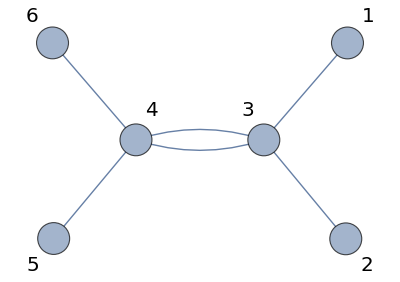

```mathematica
(* This is just a simple example to show how getGraph[.] works. *)

beamsplitter=First@getGraph[2,Method->"Square2PS"]

Graph[beamsplitter,
VertexShapeFunction->"Circle",
VertexLabels->"Name",
VertexSize->0.25,
EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.066],
VertexLabelStyle->Directive[Black,20],
(*VertexStyle->{3->Lighter@Green,1->White,2->White,4->Lighter@Green,5->White,6->White},*)
GraphLayout->"SpringEmbedding"
]
```

#### Quantum ECM

```mathematica
getDAG[vertexCount_Integer,edgeCount_Integer]:=DirectedGraph[RandomGraph[{vertexCount,edgeCount}],"Acyclic"]
```

```mathematica
initializeQuantumECM[dag_]:=Module[{n=1,nMax=20,oneAction=True,percepts,actions,graphECM,fromPerceptUtoActions=<||>,fromStoActions=<||>,fromStoECMsubgraph},

While[n<nMax&&oneAction,(* Try again as long as (1) there is only one action (not interesting) and (2) as long as the graph is not connected (can be controlled by adding more edges) *)

graphECM=dag;

If[ConnectedGraphQ[UndirectedGraph@graphECM],(* Is it connected? *)

percepts=Cases[Table[
If[Length@VertexInComponent[graphECM,{v},{1}]==0,v]
,{v,VertexList@graphECM}],_Integer];(* Percepts don't have parent nodes. *)

actions=Cases[Table[
If[Length@VertexOutComponent[graphECM,{v},{1}]==0,v]
,{v,VertexList@graphECM}],_Integer];(* Actions don't have children nodes. *)

If[Length@actions<2,(* We are not interested in ECMs with only one action. *)
oneAction=True;
Print["There was only one action for n="<>ToString@n<>"!"],
n=nMax
];

];

n++ (* We try again. *)
];


fromStoECMsubgraph=Association@Table[s->Subgraph[graphECM,VertexOutComponent[graphECM,s]],{s,percepts}];
fromStoActions=Association@Table[s->Intersection[actions,VertexOutComponent[graphECM,s]],{s,percepts}];;

Return@Association@{
"graphECM"->graphECM,
"percepts"->percepts,"actions"->actions,
"fromStoECMsubgraph"->fromStoECMsubgraph,
"nModes"->VertexCount@ graphECM,
"fromStoActions"->fromStoActions };
];
```

```mathematica
findCausalPartition[graph_,startNodes_,endNodes_]:=Module[{layer=1,candidateVerticesPreviousLayerNoPercepts,verticesPreviousLayer,parentVerticesFromPreviousLayer,layeredVertices={endNodes},verticesInPreviousLayer},

verticesPreviousLayer=VertexInComponent[graph,{#},{1}]&/@layeredVertices⟦-layer⟧;(* What transformations Us act before the current Us? *)
candidateVerticesPreviousLayerNoPercepts=Complement[DeleteDuplicates@Flatten@verticesPreviousLayer,startNodes]; (* We are not interested in percepts here. *)

While[Length@candidateVerticesPreviousLayerNoPercepts>0,(* If some Us acts before the current Us ... (n.b. we don't know when they act, we only know that it happens before)*)

verticesPreviousLayer=VertexInComponent[graph,{#},{1}]&/@layeredVertices⟦-layer⟧;
candidateVerticesPreviousLayerNoPercepts=Complement[DeleteDuplicates@Flatten@verticesPreviousLayer,startNodes];

parentVerticesFromPreviousLayer=Drop[#,1]&/@(VertexInComponent[graph,{#}]&/@candidateVerticesPreviousLayerNoPercepts);
verticesInPreviousLayer=Complement[candidateVerticesPreviousLayerNoPercepts,DeleteDuplicates@Flatten[parentVerticesFromPreviousLayer]];(* The vertices to assign to the layer before are those who are in the candidate list (of course) and are not in the parent list of the candidate list itself. *)

If[Length@verticesInPreviousLayer>0,
PrependTo[layeredVertices,verticesInPreviousLayer](* Next, we will repeat the analysis focusing on verticesInPreviousLayer. *)
];

layer++
];

Return@PrependTo[layeredVertices,startNodes];
];
```

```mathematica
infoPercept[percept_Integer,fromStoECMsubgraph_,graphECM_,fromVtoUnitary_]:=Module[{graphFromS,indicesUfromINOUTmodes},

graphFromS=fromStoECMsubgraph[percept];

(*indicesUfromINOUTmodes=Association[Table[
v->Partition[Tuples[{#,#}&@fromVtoINOUTvertices[v]],(* All in/out modes for the unitary transformation associated with vertex v. *)
Length@fromVtoINOUTvertices[v]
]
,{v,VertexList@graphFromS}]];*)

Return@Association@{
"percept"->percept,
"subgraph"->graphFromS,
"vertices"->VertexList@graphFromS,
"nSteps"->VertexCount@graphFromS-1,
"unitaries"->Association[(#->fromVtoUnitary[#])&/@VertexList@graphFromS]}
]
```

```mathematica
(* This function embeds the small unitary transformation (innerU) associated with a vertex into a large transformation of size "sizeECM", which takes into account the size of the whole ECM. *)
getUstep[sizeECM_Integer,INOUTvertices_,Unode_]:=Module[{hugeLayersInit,indices,matrix=IdentityMatrix[sizeECM]},

indices=Partition[Tuples[{#,#}&@INOUTvertices],Length@INOUTvertices];(* All in/out modes for the unitary transformation associated with vertex v. *)

Table[matrix⟦indices⟦i,j,1⟧,indices⟦i,j,2⟧⟧=Unode⟦i,j⟧,{i,Length@Unode},{j,Length@Unode}];
matrix
];
```

```mathematica
graphsCstructure=Table[getGraph[dim,Method->"Square"]⟦1⟧,{dim,25}];(* Precomputes the graph associated with the square architecture by Clements et al. *)
```

## Quantum ECM

#### Initialization

```mathematica
findLeakingNodesAnyDAG[dag_,IN_Integer,OUT_Integer]:=Module[{leakingNodesMinimal,nodesInCausalDiamond,notLeakingNodes,leakingNodes},

nodesInCausalDiamond=Intersection[VertexOutComponent[dag,{IN}],VertexInComponent[dag,{OUT}]];
leakingNodesMinimal=Append[Flatten@Select[nodesInCausalDiamond,Not[And@@((MemberQ[nodesInCausalDiamond,#]&)/@VertexOutComponent[dag, {#},1])]&],OUT];
notLeakingNodes=Complement[nodesInCausalDiamond,leakingNodesMinimal];

Return[{nodesInCausalDiamond,notLeakingNodes,leakingNodesMinimal}]
];
```

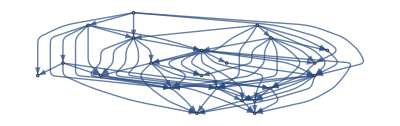

```mathematica
(*graphINFO=getGraph[DIM=10,Method->"Random"];
dag=Sort@DeleteDuplicates[graphINFO⟦1⟧];*)
(*ECMfig2={1->4,2->4,1->3,2->5,3->6,4-> 5,4->6,1->7,4->7,5->7,3->8,6->8,5->9,6->9,7-> 9,7->8};*)
dag=getDAG[vertexCount=22,edgeCountTMP=70]

infoQECM=initializeQuantumECM[dag(*ECMfig2*)];

qECM=infoQECM["graphECM"];
fromStoECMsubgraph=infoQECM["fromStoECMsubgraph"];
percepts=infoQECM["percepts"];
actions=infoQECM["actions"];
fromStoActions=infoQECM["fromStoActions"];
verticesQECM=VertexCount@qECM;


fromVtoINOUTvertices=Association[(#->Sort@VertexInComponent[qECM,#,1]&)/@(Range@verticesQECM)];(* For each vertex V, the list of vertices before and after V. *)
fromVtoUnitary=Association[#->HaarUnitary[Length@fromVtoINOUTvertices[#]]&/@Range@verticesQECM];(* For each vertex V, a Haar-random unitary U with size given by the local connectivity. *)

(*layeredVertices=findCausalPartition[graphECM,percepts,actions];*)
layeredVertices=findCausalPartition[qECM,percepts,actions];

infoPercepts=Association@Table[s->infoPercept[s,fromStoECMsubgraph,qECM,fromVtoUnitary],{s,percepts}];
```

```mathematica
(* For each vertex V, the following line retrieves the parameters that implement each unitary transformation. It is currently not used in this version of the code. *)
(*fromVtoUnitaryParameters=Association@Table[v->fromUtoParaUinit[HaarUnitary[Length@fromVtoINOUTvertices[v]],square2PSinit],{v,Range@verticesQECM}];*)
```

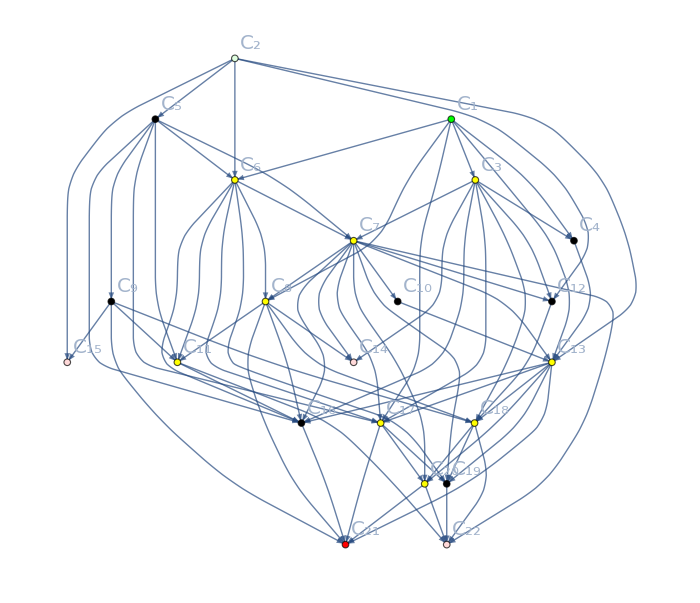

```mathematica
(* For each (s,a) pair, the following line retrieves the set of unitaries (vertices, in yellow) that need to be tuned to increase the probability that the quantum walk starting from s arrives in a. *)
leakingNodesQECM=Association@Flatten@Table[{s,a}->findLeakingNodesAnyDAG[qECM,s,a]⟦3⟧,{s,infoQECM["percepts"]},{a,infoQECM["actions"]}];

s=RandomChoice@infoQECM["percepts"];
a=RandomChoice@infoQECM["actions"];

Framed@HighlightGraph[qECM,Join[
Table[Style[node,Black],{node,VertexCount@qECM}],
Table[Style[node,Yellow],{node,leakingNodesQECM[{s,a}]}],
Table[Style[node,LightGreen],{node,infoQECM["percepts"]}],
Table[Style[node,LightRed],{node,infoQECM["actions"]}],
{Style[a,Red]},
{Style[s,Green]}
],
VertexLabels->Table[i->Style[Subscript["C",i],20],{i,verticesQECM}],
VertexSize->0.3,ImageSize->700,
AspectRatio->0.85
]
```

#### Visualization

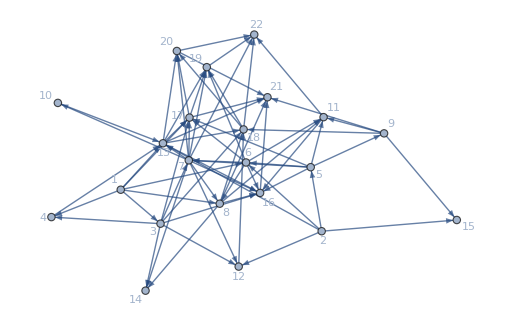
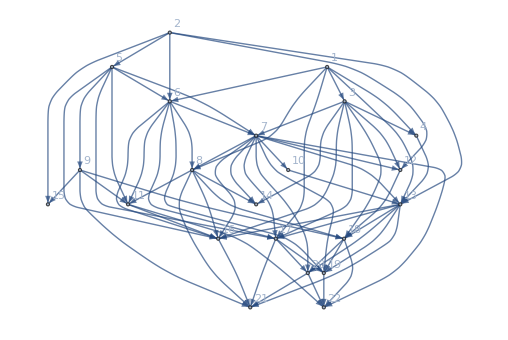
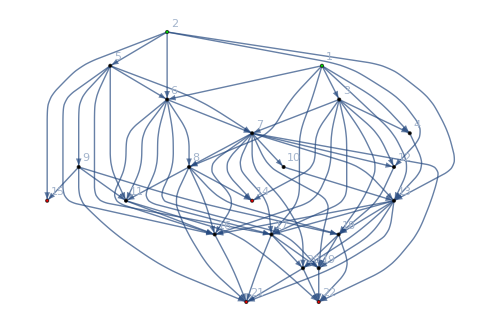

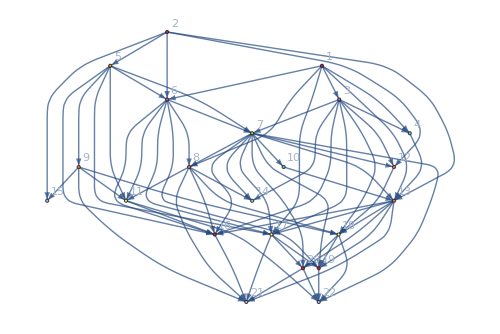
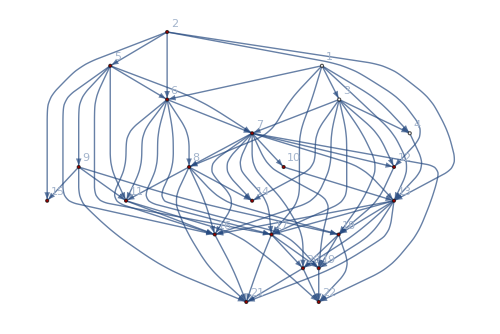

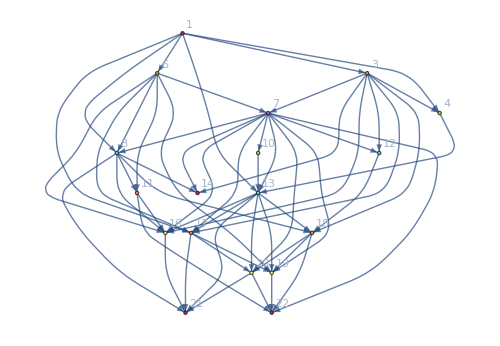
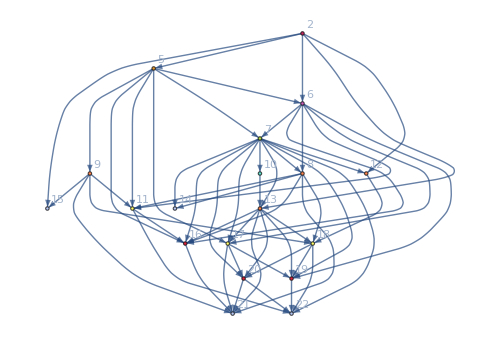

```mathematica
imageSizeFixed=500;
palette=Flatten@ConstantArray[ColorData[54,"ColorList"],5];



plotGraphECM=Framed[Graph[qECM,
ImageSize->imageSizeFixed+8,
VertexLabels->"Name",
GraphLayout->"SpringElectricalEmbedding"],
FrameMargins->0,Alignment->Center,FrameStyle->LightGray];


plotGraphECMlayered=Framed[Graph[qECM,
ImageSize->imageSizeFixed+8,
VertexLabels->"Name"
,AspectRatio->0.66],
FrameMargins->0,Alignment->Center,FrameStyle->LightGray];


plotGraphECMwithSA=Framed[HighlightGraph[qECM,
Join[
Table[Style[node,Black],{node,verticesQECM}],
Table[Style[node,Green],{node,percepts}],
Table[Style[node,Red],{node,actions}]
],
VertexLabels->"Name",
(*VertexSize->0.3,*)ImageSize->imageSizeFixed,
AspectRatio->0.66
],
FrameStyle->LightGray];


{plotGraphECM,plotGraphECMlayered,plotGraphECMwithSA}



plotGraphECMwithLayers=Framed[HighlightGraph[qECM,
Table[Style[#,palette⟦l⟧]&/@layeredVertices⟦l⟧,{l,Length@layeredVertices}],
VertexLabels->"Name",
(*VertexSize->0.3,*)ImageSize->imageSizeFixed,AspectRatio->0.66
],
FrameStyle->LightGray];


plotGraphECMsubgraph=Framed[HighlightGraph[qECM,
Join[
Table[Style[node,White],{node,verticesQECM}],
Table[Style[node,Darker@Red],{node,VertexList@fromStoECMsubgraph[First@TakeLargestBy[percepts,(Length@VertexOutComponent[qECM,#])&,1]]}]
],
VertexLabels->"Name",
(*VertexSize->0.3,*)ImageSize->imageSizeFixed,
AspectRatio->0.66
],
FrameStyle->LightGray];


{plotGraphECMwithLayers,plotGraphECMsubgraph}


(* Here, vertices are colored according to the layered structure of the qECM. *)
Framed[Table[
With[{layeredVerticesFromS=findCausalPartition[fromStoECMsubgraph[s],{s},fromStoActions[s]],g=fromStoECMsubgraph[s]},
Framed[
HighlightGraph[g,
Table[Style[#,palette⟦l⟧]&/@layeredVerticesFromS⟦l⟧,{l,Length@layeredVerticesFromS}],
VertexLabels->"Name",
(*VertexSize->0.2,*)AspectRatio->0.66,
ImageSize->imageSizeFixed
],
Background->White
]
],
{s,percepts}
],
Background->LightGray,
FrameMargins->20
]
```

```mathematica
examplePercept=1;
infoS=infoPercepts[examplePercept(* This is the integer associated with a percept. *)];

VertexList@infoS["subgraph"]
findCausalPartition[fromStoECMsubgraph[examplePercept],{examplePercept},fromStoActions[examplePercept]]
```

{1,3,4,6,8,13,17,7,12,14,16,18,11,19,21,20,10,22}

{{1},{3,6},{7},{4,10},{8,12,13},{11,17,18},{16,19,20},{14,21,22}}

| QUANTITY | VARIABLE | VALUE
1 | How many modes in the chip (edges in the ECM) | nModes | 22
2 | ECM graph with edge labels | extendedEdgeLabels | 
3 | Percept clips | percepts | {1,2}
4 | Action clips | actions | {14,15,21,22}
5 | ECM graph from each percept | fromStoECMsubgraph | 
6 | Action clips from each percept | fromStoActions | 
7 | Unitary for each vertex | fromVtoUnitary | 
8 | Full info about all percepts | infoPercepts | 
9 | Full info about percept S | infoS | 
10 | Percept | infoS[percept] | 1
11 | ECM graph from percept | infoS[subgraph] | 
12 | Unitaries applied to percept | infoS[nSteps] | 17
13 | Nodes from percept (unitaries from input mode) | infoS[vertices] | 
14 | Unitaries from percept | infoS[unitaries] | 
15 | IN-OUT vertices for each vertex | fromVtoINOUTvertices |

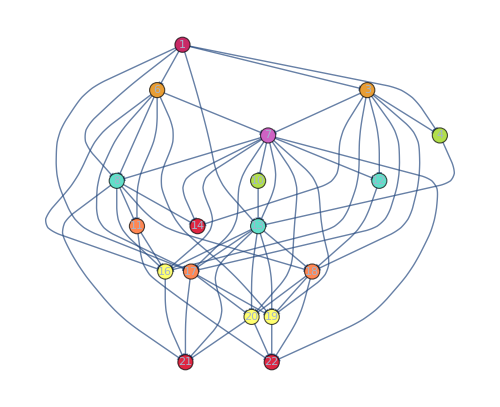
{-Graphics-, | U^0 | U^1 | U^2 | U^3 | U^4 | U^5 | U^6 | U^7 | U^8 | U^9 | U^10 | U^11 | U^12 | U^13 | U^14 | U^15 | U^16 | U^17
1 | OUT | IN | IN |  | IN |  | IN |  | IN |  | IN |  |  |  |  |  |  | 
2 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
3 |  | OUT |  | IN | IN |  |  | IN |  |  | IN | IN | IN |  |  | IN |  | 
4 |  |  |  |  | OUT |  |  |  | IN |  |  |  |  |  |  |  |  | 
5 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
6 |  |  | OUT | IN |  |  | IN |  |  | IN | IN |  | IN | IN |  |  |  | 
7 |  |  |  | OUT |  | IN | IN | IN | IN |  | IN |  | IN | IN | IN | IN |  | IN
8 |  |  |  |  |  |  | OUT |  |  | IN |  | IN | IN |  |  | IN | IN | 
9 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
10 |  |  |  |  |  | OUT |  |  | IN |  |  |  |  |  |  |  |  | 
11 |  |  |  |  |  |  |  |  |  | OUT |  |  | IN |  |  |  |  | IN
12 |  |  |  |  |  |  |  | OUT |  |  |  | IN |  |  |  |  |  | 
13 |  |  |  |  |  |  |  |  | OUT |  | IN | IN | IN | IN | IN |  | IN | 
14 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | Action |  | 
15 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
16 |  |  |  |  |  |  |  |  |  |  |  |  | OUT |  |  |  | IN | 
17 |  |  |  |  |  |  |  |  |  |  | OUT |  |  | IN | IN |  | IN | 
18 |  |  |  |  |  |  |  |  |  |  |  | OUT |  | IN | IN |  |  | IN
19 |  |  |  |  |  |  |  |  |  |  |  |  |  | OUT |  |  |  | IN
20 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | OUT |  | IN | IN
21 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | Action | 
22 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | Action, | C_1 | C_3 | C_4 | C_6 | C_8 | C_13 | C_17 | C_7 | C_12 | C_14 | C_16 | C_18 | C_11 | C_19 | C_21 | C_20 | C_10 | C_22
IN Clips     |  | C_1 | C_1
C_3 | C_1 | C_1
C_6
C_7 | C_1
C_4
C_7
C_10 | C_1
C_3
C_6
C_7
C_13 | C_3
C_6 | C_3
C_7 | C_3
C_7
C_8 | C_3
C_6
C_7
C_8
C_11
C_13 | C_3
C_8
C_12
C_13 | C_6
C_8 | C_6
C_7
C_13
C_17
C_18 | C_8
C_13
C_16
C_17
C_20 | C_7
C_13
C_17
C_18 | C_7 | C_7
C_11
C_18
C_19
C_20
OUT Clips    | C_3
C_4
C_6
C_8
C_13
C_17 | C_4
C_7
C_12
C_14
C_16
C_17
C_18 | C_13 | C_7
C_8
C_11
C_16
C_17
C_19 | C_11
C_14
C_16
C_18
C_21 | C_16
C_17
C_18
C_19
C_20
C_21 | C_19
C_20
C_21 | C_8
C_10
C_12
C_13
C_14
C_16
C_17
C_19
C_20
C_22 | C_18 |  | C_21 | C_19
C_20
C_22 | C_16
C_22 | C_22 |  | C_21
C_22 | C_13 | }

```mathematica
summary=Framed[TableForm[Join[Map[TextCell[#,"Text",Background->LightGreen,CellFrame->True]&,{
{"How many modes in the chip (edges in the ECM)","nModes",infoQECM["nModes"]},
{"ECM graph with edge labels","extendedEdgeLabels"},
{"Percept clips","percepts",percepts},{"Action clips","actions",actions},
{"ECM graph from each percept","fromStoECMsubgraph"},
{"Action clips from each percept","fromStoActions"},
{"Unitary for each vertex","fromVtoUnitary"},
{"Full info about all percepts","infoPercepts"},{"Full info about percept S","infoS"}
},{2}],
Map[TextCell[#,"Text",Background->LightOrange,CellFrame->True]&,{
{"Percept","infoS[percept]",infoS["percept"]},
{"ECM graph from percept","infoS[subgraph]"},
{"Unitaries applied to percept","infoS[nSteps]",infoS["nSteps"]},
{"Nodes from percept (unitaries from input mode)","infoS[vertices]"},
{"Unitaries from percept","infoS[unitaries]"}
},{2}],
Map[TextCell[#,"Text",Background->LightPink,CellFrame->True]&,{
{"IN-OUT vertices for each vertex","fromVtoINOUTvertices"}
},{2}]
],
TableHeadings->{Automatic,TextCell[#,"Text",Background->LightGray,CellFrame->True]&/@{"QUANTITY","VARIABLE","VALUE"}}
],
FrameMargins->10,
Background->White
];


Print@summary;

(* ---------------------------------------------------- *)


Framed[
{

With[{
labelingAssoc=AssociationThread[infoS["vertices"],Placed[{Last@#,#2},{Tooltip,Center}]&@@@Transpose[{MatrixForm/@Values@infoS["unitaries"],infoS["vertices"]}]],
layeredVerticesFromPerceptU=findCausalPartition[infoS["subgraph"],{infoS["percept"]},fromStoActions[infoS["percept"]]]},
Framed[HighlightGraph[infoS["subgraph"],
Table[Style[#,ColorData[54,"ColorList"]⟦l⟧]&/@layeredVerticesFromPerceptU⟦l⟧,{l,Length@layeredVerticesFromPerceptU}],
VertexLabels->{v_:>labelingAssoc[v]},
VertexSize->0.75,
ImageSize->500,
AspectRatio->0.75
],
Background->White,
FrameMargins->20
]
],


(* ---------------------------------------------------- *)

fromVtoINOUTverticesSubgraph=Association[(#->Sort@VertexInComponent[infoS["subgraph"],#,{1}]&)/@(VertexList@infoS["subgraph"])];

With[{steps=VertexCount@qECM-Length[infoQECM["fromStoActions"][examplePercept]]},
Framed[TableForm[
Table[Which[
row==col&&MemberQ[infoQECM["fromStoActions"][examplePercept],row],Item["Action",Alignment->Center,Background->LightRed,Frame->True],
row==col,Item["OUT",Alignment->Center,Background->LightOrange,Frame->True],
MemberQ[fromVtoINOUTverticesSubgraph[col],row],Item["IN",Alignment->Center,Background->LightBlue,Frame->True],
True,""],
{row,VertexCount@qECM},{col,Flatten@findCausalPartition[fromStoECMsubgraph[examplePercept],{examplePercept},fromStoActions[examplePercept]]}
],
TableHeadings->{Automatic,Table[Superscript["U",l-1],{l,Length@VertexList@infoS["subgraph"]+1}]},
TableSpacing->{0.5,3},
TableAlignments->{Right,Center}
],
Background->White,
FrameMargins->10
]
],

(* ---------------------------------------------------- *)


Framed[TableForm[{
Subscript["C", #]&/@Sort@VertexInComponent[infoS["subgraph"],#,{1}]&/@infoS["vertices"],
Subscript["C", #]&/@Sort@VertexOutComponent[infoS["subgraph"],#,{1}]&/@infoS["vertices"]
},
TableHeadings->{{"IN Clips    ","OUT Clips   "},Subscript["C", #]&/@infoS["vertices"]},
TableSpacing->{5,3}]
,
Background->White,
FrameMargins->30
]

},

Background->Gray
]
```

#### Training

```mathematica
initializeParametrizedVertices[sizeU_Integer,vertexLabel_Integer]:=Module[{graphINFO,cellPositions,cellsUpara,layersPara,phaseSettingsInit},

graphINFO=getGraph[sizeU,Method->"Square2PS"];
cellPositions=graphINFO⟦2,2;;-2⟧;
cellsUpara=Table[Join[#⟦s,k⟧,{1,Subscript[P, s,k,graphINFO⟦3,s+1,k⟧,vertexLabel]}],{s, Length@#},{k,Length[#⟦s⟧]}]&@cellPositions;

layersPara=Table[Normal@chipLayer[sizeU,cellsUpara,layer],{layer,Length@cellPositions}];

phaseSettingsInit=Map[(#->RandomReal[{0,2π}])&,Table[
Subscript[P, s,k,graphINFO⟦3,s+1,k⟧,vertexLabel] ,{s,Length@cellPositions},{k,Length[cellPositions⟦s⟧]}],{2}
];

Return@{layersPara,phaseSettingsInit}
]; 




fromUtoParaUinit[U_,square2PSinit_]:=Module[{dim=Length@U,cellPositions,nBSinLayers,pos2take,phases,cellsUpara,diag,newU,layersPara},

If[dim>2,
{cellPositions,nBSinLayers,pos2take}=square2PSinit⟦dim⟧⟦;;3⟧;
phases=Square2PSDecomposition[U,square2PSinit];

cellsUpara=Table[Join[#⟦s,k⟧,{1,phases⟦2,s,k⟧}],{s,Length@#},{k,Length[#⟦s⟧]}]&@cellPositions;
diag=DiagonalMatrix[expI@phases⟦1⟧];
layersPara=Chop@Table[Normal@chipLayer[dim,cellsUpara,layer],{layer,Length@cellsUpara}];
{U,Join[{diag,layersPara}]}
,
diag=DiagonalMatrix[expI@RandomReal[{0,2π},dim]];
Return@{diag,Join[{diag,IdentityMatrix@dim}]}
]

(*newU=diag.Dot@@Reverse@layerPara;*)
];
```

```mathematica
infoQECM["percepts"]
infoQECM["fromStoActions"]
{s,a}=Last@SortBy[Flatten[Table[{s,a},{s,infoQECM["percepts"]},{a,infoQECM["fromStoActions"][s]}],1],VertexCount@Subgraph[qECM,FindShortestPath[qECM,#⟦1⟧,#⟦2⟧]]&]
```

{1,2}

<|1→{14,21,22},2→{14,15,21,22}|>

{2,22}

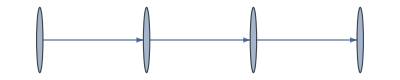

{5,7,22}

{{2,5},{5,7},{7,22}}

<|5→{2,5},7→{5,7},22→{7,22}|>

<|5→{1,2},7→{2,4},22→{1,6}|>

{2,5,6,7,10,8,9,12,13,11,17,18,16,19,20,14,15,21,22}

{{2},{5},{6},{7},{10,8,9,12,13,11,17,18,16,19,20,14,15,21},{22}}

```mathematica
optimizedPath=Subgraph[qECM,FindShortestPath[qECM,s,a]] (* This is the path in the ECM that will be optimized via Gram-Schmidt (or any other approach). *)
UtoOptimize=Drop[VertexList@optimizedPath,1]

inOutModesToOptimize=Partition[VertexList@optimizedPath,2,1] (* Retrieves the in/out modes to be optimized. *)
fromVtoInOutModesToOptimize=Association@Thread[UtoOptimize->inOutModesToOptimize](* These are the in/out modes of huge qECM unitary that, at each step in the qECM, will be optimized via a Gram-Schmidt process. <| vertex -> (in,out), ... |> *)

inMode=s;
outMode=a;

indicesToOptimize=Association@Table[
v->(Position[fromVtoINOUTvertices[v],#]⟦1,1⟧&/@fromVtoInOutModesToOptimize[v]),
{v,Keys@fromVtoInOutModesToOptimize}
](* These are the in/out modes of each unitary that, at each step in the qECM, will be optimized via a Gram-Schmidt process. <| vertex -> (in,out), ... |> *)

orderedVerticesFromS=Select[Flatten@layeredVertices,MemberQ[infoPercepts[s]["vertices"],#]&]

SplitBy[orderedVerticesFromS,MemberQ[UtoOptimize,#]&]
```

```mathematica
nOptSteps=40;
rewardValues={1.1,1.2,1.3};
prob=ConstantArray[0,{Length@rewardValues,nOptSteps}];

monitoredSteps={2,nOptSteps};
savedConfig4Trace=ConstantArray[0,2];
savedConfigCont=0;

(*MatrixForm[Chop[abs2@infoPercepts[s]["unitaries"][#],10^-4]]&/@FindShortestPath[qECM,s,a]*)



Do[
initUlist=infoPercepts[s]["unitaries"];

Do[

If[MemberQ[monitoredSteps,step]&&nReward==Length@rewardValues,
savedConfigCont++;
savedConfig4Trace⟦savedConfigCont⟧=initUlist
];

Do[
If[MemberQ[UtoOptimize,v],
initUlist[v]=variateGS[initUlist[v],indicesToOptimize[v]⟦1⟧,indicesToOptimize[v]⟦2⟧,rewardValues⟦nReward⟧],(* Unitaries are updated via a Gram-Schmidt process. *)
Do[initUlist[v]=variateGS[initUlist[v],i,i,rewardValues⟦nReward⟧],{i,Length@initUlist[v]}](* Unitaries are updated via a Gram-Schmidt process. *)
]
,{v,orderedVerticesFromS}];

allLayers=Reverse@ParallelTable[
getUstep[infoQECM["nModes"],fromVtoINOUTvertices[v],initUlist[v]],{v,orderedVerticesFromS}]; (* Embeds each unitary U into a larger transformation whose size is given by the size of the quantum ECM. *);

UfullECM=Dot@@allLayers;
prob⟦nReward,step⟧=abs2[UfullECM⟦outMode,inMode⟧];
,{step,nOptSteps}
]
,{nReward,Length@rewardValues}
];
```

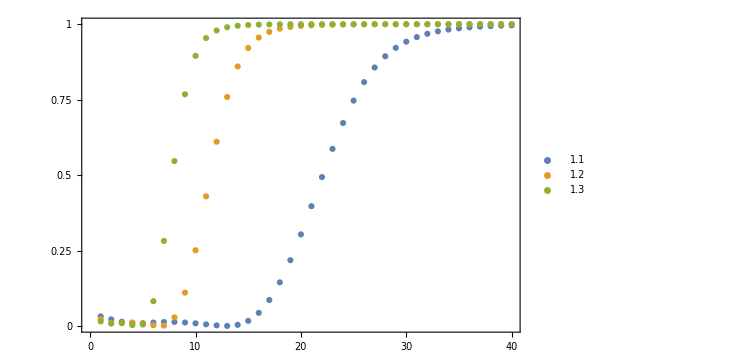

```mathematica
ListPlot[prob,
PlotRange->{0,1},
ImageSize->550,
BaseStyle->22,
PlotStyle->PointSize[0.008],
Frame->True,
AspectRatio->0.66,
FrameTicks->{{{0,0.25,0.5,0.75,1},None},{{0,10,20,30,40,50},None}},
PlotLegends->Placed[Style[#,18]&/@rewardValues,{Left,Top}](*,
PlotLabels->(Style[ToString@#,14]&/@rewardValues)*)(*,
Epilog->Inset[causalDiamondGraphNotAnnotated,Scaled[{.7,.25}],Automatic,200,{1,0}],*)
]
```

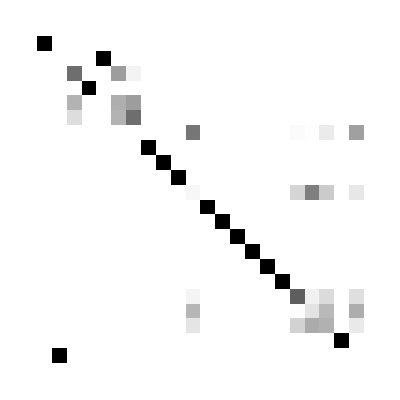

```mathematica
ArrayPlot[abs2@UfullECM,ImageSize->400]
```

```mathematica
partialProbs=ConstantArray[0,{2,Length@orderedVerticesFromS}];


Do[
init=IdentityMatrix@infoQECM["nModes"];
step=0;

Do[
step++;
initUlist=savedConfig4Trace⟦monitoredStep⟧;

partialU=getUstep[infoQECM["nModes"],fromVtoINOUTvertices[v],initUlist[v]].init;
partialProbs⟦monitoredStep,step⟧=abs2@partialU⟦;;,inMode⟧;
init=partialU;

,{v,orderedVerticesFromS}
]
,{monitoredStep,2}
];



barChart3D[partialProbs⟦#⟧,500]&/@{1,2} (* Before and after learning, the transition probabilities in the qECM become sharp. *)
```

{-Graphics3D-,-Graphics3D-}

## Variational approaches to RL

### Based on Causal Diamonds

#### Functions

```mathematica
(* This function uses the graph representation of optical circuits that is input via "graphINFO", the name used in this package for the output of the function "getGraph", described in Sec. "Graph representation" above. *)
(* This function is written for the square architecture with beamsplitters implemented as MZI. In this layout one always has a set of nodes (each containing a phase shifter) that connect to only one node each (the phase shifter inside the MZI), and this is not interpreted correctly when retrieving the surface of the causal diamond (light does not leak out from these nodes, but still it has to be tuned). *)
(* Other architectures can be studied with this function by reducing the numbers in orange "(*" by 1. *)


findLeakingNodes[dim_(* Size of the circuit. *),graphINFO_,IN_(* Mode *),OUT_(* Mode *)]:=Module[{directedGraph,leakingNodesMinimal,leakingNodesExtension,nodesInCausalDiamond,notLeakingNodes,lightConeNodes,leakingNodes,borders,extraNodes},

directedGraph=DeleteDuplicates@graphINFO⟦1⟧;(* In the square architecture with BS implemented as MZI, some PS have a double edge to the next PS. *)

nodesInCausalDiamond=Intersection[VertexOutComponent[directedGraph,{IN}],VertexInComponent[directedGraph,{OUT}]];(* By definition. *)

(* Code below repeats the following instruction 4 times:
Pick each vertex of [...] with the property that NOT ALL vertices in its in/out-component belong to "nodesInCausalDiamond". *)

notLeakingNodes=Flatten@Select[
nodesInCausalDiamond,
Not[And@@((MemberQ[nodesInCausalDiamond,#]&)/@VertexInComponent[directedGraph, {#},1(**)])]&
];

leakingNodesMinimal=Flatten@Select[
nodesInCausalDiamond,
Not[And@@((MemberQ[nodesInCausalDiamond,#]&)/@VertexOutComponent[directedGraph, {#},1(**)])]&
];

leakingNodesExtension=Flatten@Select[
notLeakingNodes,
Not[And@@((MemberQ[nodesInCausalDiamond,#]&)/@VertexOutComponent[directedGraph, {#},{2(**)}])]&
];

borders=Intersection[
nodesInCausalDiamond,
Flatten@graphINFO⟦3,2;;-2,{1,-1}⟧(* These are the upper/lower borders of the optical circuit. Light cannot escape here, and this is taken into account so that we don't optimize unnecessary phase shifters. *)
];

extraNodes=Select[
borders,
Not[And@@((MemberQ[nodesInCausalDiamond,#]&)/@VertexOutComponent[directedGraph, {#},2])]&
];

leakingNodes=Sort@DeleteDuplicates@Join[
extraNodes,
Sort@DeleteDuplicates@Join[leakingNodesMinimal,leakingNodesExtension]
];

lightConeNodes=Sort@DeleteDuplicates@Join[notLeakingNodes,leakingNodes];

Return[{lightConeNodes,leakingNodes}]

];
```

```mathematica
(* This function updates phase shifters according to the [variational approach based on causal diamonds] described in the paper. To speed it up, this implementation is a bit more convoluted than the high-level description. *)
(* Since the purpose of this code is to illustrate and test the proposed algorithm, this function only involves a simple mechanism for the update (θ⟶θ±δ). More sophisticated update rules can easily by integrated. *)

(* The intuitive implementation of the update based on causal diamonds (a) is sped up in the following way (b):

a) Instead of iteratively (1) taking the layer-wise representation of a circuit, (2) changing one phase, (3) multiplying all layers to evaluate the updated U;

	b) We iteratively (1) multiply all layers that appear before and after the layer "ϕlayer" with the first phase that will be updated, to get the partial transformations "layersFixedPartBefore" and "layersFixedPartAfter", respectively, (2) change the phase, (3) evaluate U=layersFixedPartAfter.ϕlayer.layersFixedPartBefore, (4) include ϕlayer into "layersFixedPartBefore" and remove it from "layersFixedPartAfter".
*)

updateCausalDiamond[
layersFixed_,(* The set of layers at the beginning of the circuit, which will not be updated. *)
layersPara_,(* The set of layers that contain relevant parameters and will be updated. *)
updateCausalDiamondSequence_,(* The set of nodes in the graph representation that point to parameters that will be tuned. *)
startingLayer_,finalLayer_,(* The labels of the first/last layers we want to update. *)
posNodesInLayers_,(* Where in the vertical layer is located the phase shifter (node) we want to update? *)
phase2change_,(* Phase values that will be updated. *)
ϕshift_,(* By how much we change each phase shifter during the optimization. This is a simple and intuitive mechanism to illustrate the algorithm, here one can be creative. *)
pairSA_(* Percept/Action pair. *)
]:=Module[{
IN,OUT,
updateCDnodesLayerwise,
layersFixedPartBefore=layersFixed,
layersFixedPartAfter,
newLayer,(* Current circuit layer with phase values already inserted. *)
nEffLayers,
ϕtmp=phase2change,
newTargetValues1,newTargetValues2,
currentU,
currentTargetValue,
newU1,newU2,
currentLayerIndex,
δ,
l,
ϕlayer,
nodePos
},

{IN,OUT}=pairSA;

updateCDnodesLayerwise=Values@updateCausalDiamondSequence;

nEffLayers=finalLayer-startingLayer+1;(* How many circuit layers we effectively go through during the optimization. *)

layersFixedPartAfter=Dot@@Reverse@Table[
layersPara⟦1+layer⟧/.ϕtmp⟦startingLayer+layer⟧
,{layer,1,nEffLayers-1}];

δ=ϕshift;


(* ------------------------------------------------------------------ *)


Do[

l=startingLayer+currentLayerIndex-1;(* "l" stands for layer. This quantity keeps track of "in what layers are we now?". *)

Do[

nodePos=posNodesInLayers⟦l⟧[node];

If[Not[MissingQ@nodePos],

(* ------------------------------------------------- *)

ϕlayer=ϕtmp⟦l⟧;

currentU=layersFixedPartAfter.(layersPara⟦currentLayerIndex⟧/.ϕlayer).layersFixedPartBefore;
currentTargetValue=abs2@currentU⟦OUT,IN⟧;(* Relevant transition probability. We want to maximize this quantity. *)

ϕlayer⟦nodePos,2⟧+=δ;
newLayer=layersPara⟦currentLayerIndex⟧/.ϕlayer;
newU1=layersFixedPartAfter.newLayer.layersFixedPartBefore;
newTargetValues1=abs2@newU1⟦OUT,IN⟧;

ϕlayer=ϕtmp⟦l⟧;

ϕlayer⟦nodePos,2⟧-=δ;
newLayer=layersPara⟦currentLayerIndex⟧/.ϕlayer;
newU2=layersFixedPartAfter.newLayer.layersFixedPartBefore;
newTargetValues2=abs2@newU2⟦OUT,IN⟧;

(* ------------------------------------------------- *)

Which[
currentTargetValue>newTargetValues1&&currentTargetValue>newTargetValues2,(* If the current transition probability is larger than the updated version with θ⟶θ±δ, we keep the value of the phase. *)
Nothing,
newTargetValues1>newTargetValues2,
ϕtmp⟦l,nodePos,2⟧+=δ;,
newTargetValues1≤newTargetValues2,
ϕtmp⟦l,nodePos,2⟧-=δ;
],

Nothing
];

,{node,updateCDnodesLayerwise⟦currentLayerIndex⟧}
];


(* ------ Here we update the fixed transformations before and after the current layer, to speed up the optimization. ------ *)
layersFixedPartBefore=(layersPara⟦currentLayerIndex⟧/.ϕtmp⟦l⟧).layersFixedPartBefore;

If[currentLayerIndex<nEffLayers,
layersFixedPartAfter=Chop[layersFixedPartAfter.Inverse[layersPara⟦currentLayerIndex+1⟧/.ϕtmp⟦l+1⟧]]
];
(* ------------------------------------------------------------------------------------------------------ *)


,{currentLayerIndex,nEffLayers}
];

currentU=layersFixedPartBefore;

Return[{ϕtmp,currentU}]

];
```

#### Square architecture

```mathematica
(*minDIM=1;
maxDIM=30;
allLeakingNodesDIMS=ConstantArray[{},{1+maxDIM-minDIM}];
DIMindex=0;

Do[
DIMindex++;
graphINFO=getGraph[DIM,Method->"Square2PS"];
directedGraph=DeleteDuplicates@graphINFO⟦1⟧;
nVertices=VertexCount@directedGraph;
allLeakingNodesDIMS⟦DIMindex⟧=Table[findLeakingNodes[DIM,graphINFO,inMode,nVertices-DIM+outMode],{inMode,DIM},{outMode,DIM}];
,{DIM,minDIM,maxDIM}
];

Put[allLeakingNodesDIMS,myPATHimport<>"allLeakingNodes2PSDIMS.txt"]*)
```

```mathematica
allLeakingNodesDIMS=Get[myPATHimport<>"allLeakingNodes2PSDIMS.txt"];
```

```mathematica
DIM=11;(* Size of the circuit. *)

graphINFO=getGraph[DIM,Method->"Square2PS"]; (* "Square2PS" is the label for the square architecture where beamsplitters are implemented as tunable MZI. *)
directedGraph=DeleteDuplicates@graphINFO⟦1⟧;(* DeleteDuplicates takes care of the double connection between adjacent phase shifters in the "Square2PS" implementation. *)
nVertices=VertexCount@directedGraph;
g=directedGraph/.(xxx_->yyy_)->(xxx<->yyy);

allLeakingNodes=allLeakingNodesDIMS⟦DIM⟧;(* Pre-computed quantity for all circuits of size DIM, see above. *)

cellPositions=graphINFO⟦2,2;;-2⟧;

cellsUpara=Table[
Join[#⟦s,k⟧,{1,Subscript[P, s,k,graphINFO⟦3,s+1,k⟧]}](* There are three indices here: 1) s = layer in the circuit; 2) k = position of the phase shifter in the layer; 3) MZ label in each layer. *)
,{s, Length@#},{k,Length[#⟦s⟧]}]&@cellPositions;

layersPara=Table[Normal@chipLayer[DIM,cellsUpara,layer],{layer,Length@cellPositions}];(* All layers in the circuit, given the parameter specification in "cellsUpara". *)

phaseSettingsInitialization=Map[(#->RandomReal[{0,2π}])&,Table[
Subscript[P, s,k,graphINFO⟦3,s+1,k⟧] ,{s,Length@cellPositions},{k,Length[cellPositions⟦s⟧]}],{2}
]
```

{{P_(1,1,12)→2.47525,P_(1,2,13)→1.18683,P_(1,3,14)→3.56952,P_(1,4,15)→0.479832,P_(1,5,16)→5.28574},{P_(2,1,17)→1.68381,P_(2,2,18)→1.17596,P_(2,3,19)→3.59209,P_(2,4,20)→5.87986,P_(2,5,21)→2.70435},{P_(3,1,22)→5.93274,P_(3,2,23)→4.27131,P_(3,3,24)→4.04543,P_(3,4,25)→5.70656,P_(3,5,26)→2.81865},{P_(4,1,27)→0.269661,P_(4,2,28)→2.74143,P_(4,3,29)→0.150985,P_(4,4,30)→0.367665,P_(4,5,31)→2.17461},{P_(5,1,32)→6.22224,P_(5,2,33)→1.19592,P_(5,3,34)→0.498472,P_(5,4,35)→2.76916,P_(5,5,36)→3.7833},{P_(6,1,37)→3.99158,P_(6,2,38)→4.02373,P_(6,3,39)→3.34163,P_(6,4,40)→0.416141,P_(6,5,41)→1.43493},{P_(7,1,42)→6.24402,P_(7,2,43)→2.94545,P_(7,3,44)→3.23,P_(7,4,45)→1.99545,P_(7,5,46)→5.08001},{P_(8,1,47)→1.25007,P_(8,2,48)→6.13491,P_(8,3,49)→2.73744,P_(8,4,50)→0.438909,P_(8,5,51)→1.07386},{P_(9,1,52)→4.64472,P_(9,2,53)→1.7609,P_(9,3,54)→5.86661,P_(9,4,55)→6.16577,P_(9,5,56)→2.11898},{P_(10,1,57)→4.9726,P_(10,2,58)→3.05265,P_(10,3,59)→4.97478,P_(10,4,60)→1.58181,P_(10,5,61)→4.87267},{P_(11,1,62)→2.6274,P_(11,2,63)→1.07475,P_(11,3,64)→0.29878,P_(11,4,65)→6.28162,P_(11,5,66)→0.842702},{P_(12,1,67)→1.66404,P_(12,2,68)→1.55876,P_(12,3,69)→0.451269,P_(12,4,70)→0.464335,P_(12,5,71)→1.75629},{P_(13,1,72)→5.69585,P_(13,2,73)→4.15621,P_(13,3,74)→3.92783,P_(13,4,75)→0.337724,P_(13,5,76)→0.83935},{P_(14,1,77)→3.27794,P_(14,2,78)→0.146792,P_(14,3,79)→4.95136,P_(14,4,80)→1.99529,P_(14,5,81)→3.50186},{P_(15,1,82)→2.79113,P_(15,2,83)→2.382,P_(15,3,84)→3.24287,P_(15,4,85)→0.899505,P_(15,5,86)→1.26837},{P_(16,1,87)→3.67215,P_(16,2,88)→4.53631,P_(16,3,89)→0.0501091,P_(16,4,90)→1.10602,P_(16,5,91)→2.89396},{P_(17,1,92)→2.60901,P_(17,2,93)→0.623,P_(17,3,94)→5.64612,P_(17,4,95)→6.06009,P_(17,5,96)→6.14767},{P_(18,1,97)→4.003,P_(18,2,98)→2.42657,P_(18,3,99)→3.60699,P_(18,4,100)→2.33791,P_(18,5,101)→4.85104},{P_(19,1,102)→5.75838,P_(19,2,103)→1.86579,P_(19,3,104)→6.06303,P_(19,4,105)→3.69642,P_(19,5,106)→1.68882},{P_(20,1,107)→4.31355,P_(20,2,108)→3.29297,P_(20,3,109)→2.82237,P_(20,4,110)→3.99781,P_(20,5,111)→1.72958},{P_(21,1,112)→1.15998,P_(21,2,113)→2.54884,P_(21,3,114)→4.11576,P_(21,4,115)→2.30211,P_(21,5,116)→0.980653},{P_(22,1,117)→5.33871,P_(22,2,118)→4.48714,P_(22,3,119)→3.94639,P_(22,4,120)→3.66423,P_(22,5,121)→1.85087}}

```mathematica
Niterations=500;

phaseSettings=phaseSettingsInitialization;

nodesLayer=graphINFO⟦3,2;;-2⟧;
posNodesInLayers=Table[Association[(nodesLayer⟦l,#⟧->#)&/@Range@Length@cellPositions⟦l⟧],{l,Length@cellPositions}];

fromNodetoLayer=Association@Flatten@Table[nodesLayer⟦l,i⟧->l,{l,Length@nodesLayer},{i,Length@nodesLayer⟦l⟧}];
updateCausalDiamondSequence=Table[
Sort[Join[(<|(#-> {x})&/@Range[Min@#,Max@#]&@Keys@#|>),#]&@GroupBy[allLeakingNodes⟦inMode,outMode,2⟧,fromNodetoLayer],#1>#2&](* This line groups nodes by their layer in the circuit. NB: I don't remember why I wrote the first half of this line (brown), which seems to be unnecessary, but I remember it used to be necessary :). I leave it here since it is harmless, maybe it becomes essential for more general connectivities. *)
,{inMode,DIM},{outMode,DIM}];
updateCDstartingLayer=Map[Min@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDfinalLayer=Map[Max@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDnodesLayerwise=Map[Values,updateCausalDiamondSequence,{2}];


ϕupdateINIT=0.033;(* Initial size of the phase shift. Larger values lead to faster optimizations but might result in lower maxima or poorer performance when there are multiple rewarded (s,a). *)
ϕupdateFIN=0.002;(* Final size of the phase shift. Larger values lead to faster optimizations but might result in lower maxima or poorer performance when there are multiple rewarded (s,a). *)
ϕupdate=ϕupdateINIT;
ϕstep=(ϕupdateINIT-ϕupdateFIN)/Niterations;(* The size of the phase shift is progressively reduced in a linear way. *)
ϕupdate-=ϕstep;

NsampledPairs=Floor@(DIM/2)-1;(* Here we select how many percept/action pairs are rewarded. The larger the number, the harder the task. Min=1, Max=Floor@(DIM/2), since 2 modes encode 1 percept. *)
inModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
outModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
possiblePairs=Sort[{inModes⟦#⟧,outModes⟦#⟧}&/@Range@NsampledPairs];
Print["These are the percept/action pairs that are rewarded: ",possiblePairs];

currentProbPercept2Action=ConstantArray[0.,{NsampledPairs,Niterations}];



Do[

{s,a}=RandomChoice[possiblePairs];
indexNextPair=Position[possiblePairs,{s,a}]⟦1,1⟧;

If[updateCDstartingLayer⟦s,a⟧≠1,
layersFixed=Dot@@Reverse@Table[layersPara⟦layer⟧/.phaseSettings⟦layer⟧,{layer,updateCDstartingLayer⟦s,a⟧-1}];,
layersFixed=IdentityMatrix@DIM
];
layersVariable=layersPara⟦updateCDstartingLayer⟦s,a⟧;;⟧;

updateResult=updateCausalDiamond[layersFixed,layersVariable,updateCausalDiamondSequence⟦s,a⟧,updateCDstartingLayer⟦s,a⟧, updateCDfinalLayer⟦s,a⟧,posNodesInLayers,phaseSettings,ϕupdate,{s,a}];

phaseSettings=updateResult⟦1⟧;(* New phase settings after one step of the update. *)
u=updateResult⟦2⟧;(* New unitary after one step of the update. *)
currentProbPercept2Action⟦indexNextPair,iter⟧=abs2@u⟦a,s⟧;
,

{iter,Niterations}
];
```

These are the percept/action pairs that are rewarded: {{2,6},{4,8},{6,2},{10,4}}

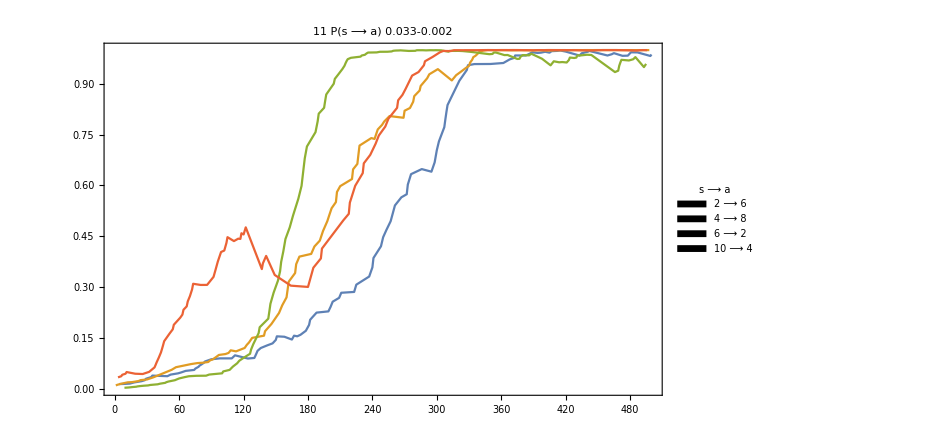

```mathematica
evolutionProbsPercept2ActionTMP=currentProbPercept2Action⟦Position[possiblePairs,#]⟦1,1⟧⟧&/@possiblePairs;
evolutionProbsPercept2Action=Table[If[evolutionProbsPercept2ActionTMP⟦pair,iter⟧≠0.,{iter,evolutionProbsPercept2ActionTMP⟦pair,iter⟧},Nothing],{pair,NsampledPairs},{iter,Niterations}];

ListPlot[evolutionProbsPercept2Action,
PlotRange->{0,1},
ImageSize->700,
Frame->True,
Joined->True,
BaseStyle->16,
PlotLegends->Placed[SwatchLegend[
Style[(""<>ToString[#⟦1⟧]<>" ⟶ "<>ToString[#⟦2⟧]),14]&/@possiblePairs,
LegendLabel->Style["  s ⟶ a",15],
LegendMarkers->Graphics[Disk[]],
LegendFunction->(Framed[#,Background->LightGray]&)],{Bottom,Right}],
FrameTicks->{Automatic,Automatic},(*
Epilog->Inset[causalDiamondGraphNotAnnotated,Scaled[{.7,.25}],Automatic,200,{1,0}],*)
PlotLabel->ToString@DIM<>"          P(s ⟶ a)         "<>ToString@ϕupdateINIT<>"-"<>ToString@ϕupdateFIN
]
```

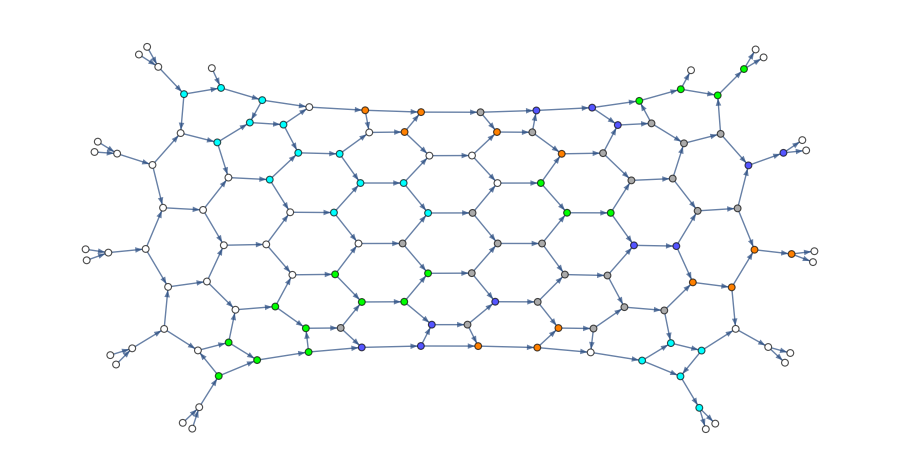

```mathematica
colors={Green,Lighter@Blue,Orange,Cyan,Red,Pink,Yellow,Magenta,Brown};

allLeakingNodesAllPairs=allLeakingNodes⟦possiblePairs⟦#,1⟧,possiblePairs⟦#,2⟧,2⟧&/@Range@NsampledPairs;

highlightedNodes=Flatten@Table[Style[allLeakingNodesAllPairs⟦pathN,node⟧,colors⟦pathN⟧,Thick],{pathN,Length@allLeakingNodesAllPairs},{node,Length@allLeakingNodesAllPairs⟦pathN⟧}];

overlappingNodes=First/@Cases[Tally[Flatten@allLeakingNodesAllPairs],u_/;u[[2]]≥2];
highlightedOverlappingNodes=Flatten@Table[Style[node,Lighter@Gray],{node,overlappingNodes}];

otherNodes=Style[#,White]&/@Complement[VertexList@g,DeleteDuplicates@Flatten@allLeakingNodesAllPairs];

HighlightGraph[Graph@directedGraph,
Join[highlightedNodes,highlightedOverlappingNodes,otherNodes],
ImageSize->900
]
```

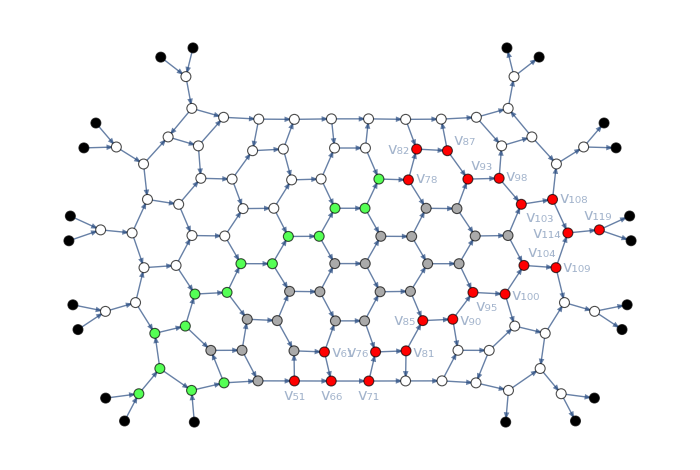
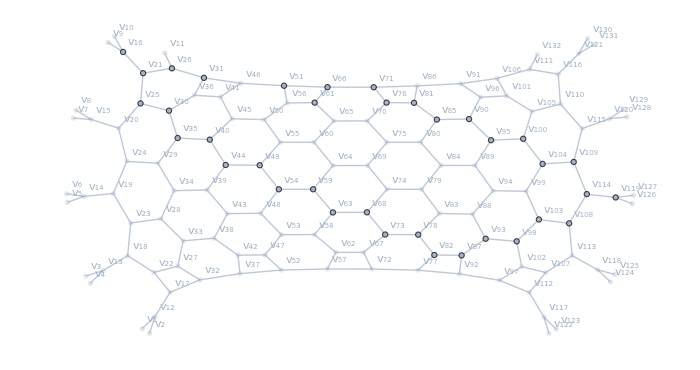

```mathematica
inMode=10; (* Example *)
outMode=5;(* Example *)

{lightCone,leakingNodes}=allLeakingNodes⟦inMode,outMode⟧;

highlightedNodes=Join[
Style[#,White]&/@Range[DIM+1,nVertices-DIM],
Style[#,Lighter@Gray]&/@Complement[Intersection[VertexOutComponent[directedGraph,{inMode}],VertexInComponent[directedGraph,{nVertices-DIM+outMode}]],lightCone],
Style[#,Lighter@Green]&/@Complement[lightCone,leakingNodes],
Style[#,Red]&/@leakingNodes,
Style[#,Black]&/@Range@DIM,
Style[#,Black]&/@Range[nVertices-DIM+1,nVertices]
];


{
HighlightGraph[directedGraph,
highlightedNodes,
VertexSize->Large,
GraphLayout->"SpringEmbedding",
ImageSize->700,
VertexLabels->Table[i->Style[Subscript[v, i],16],{i,leakingNodes}]
],

causalDiamondGraphAnnotated=HighlightGraph[g,
GraphLayout->"SpringEmbedding",
GraphHighlight->lightCone,
GraphHighlightStyle->"DehighlightFade",
ImageSize->700,
VertexLabels->Table[i->Subscript[v, i],{i,nVertices}]
]
}
```

#### Triangular architecture

```mathematica
(*minDIM=1;
maxDIM=30;
allLeakingNodesDIMS=ConstantArray[{},{1+maxDIM-minDIM}];
DIMindex=0;

Do[
DIMindex++;
graphINFO=getGraph[DIM,Method->"Triangular"];
directedGraph=DeleteDuplicates@graphINFO⟦1⟧;
nVertices=VertexCount@directedGraph;
allLeakingNodesDIMS⟦DIMindex⟧=Table[findLeakingNodes[DIM,graphINFO,inMode,nVertices-DIM+outMode],{inMode,DIM},{outMode,DIM}];
,{DIM,minDIM,maxDIM}
];

Put[allLeakingNodesDIMS,myPATHimport<>"allLeakingNodesTriangularDIMS.txt"]*)
```

```mathematica
allLeakingNodesTriangularDIMS=Get[myPATHimport<>"allLeakingNodesTriangularDIMS.txt"];
```

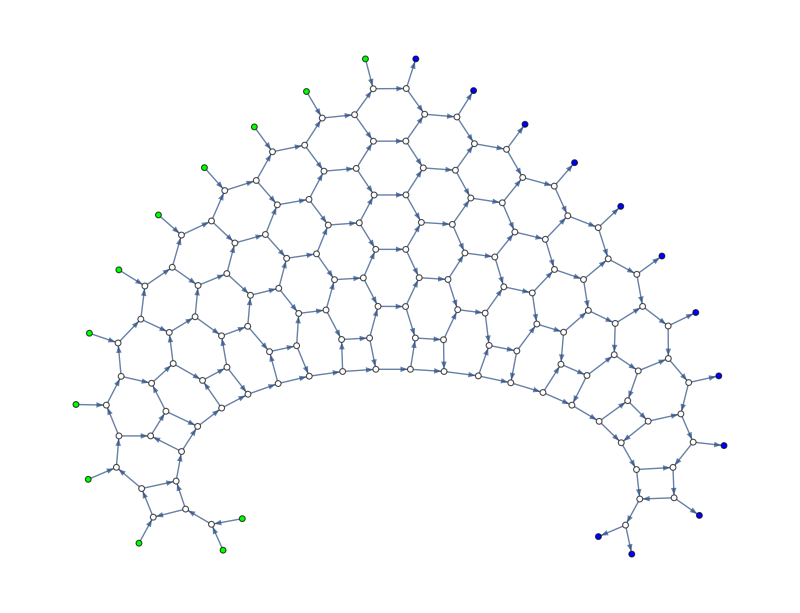

```mathematica
(* For comments to this section, we refer to Section "Square architecture" above. *)

DIM=12;

graphINFO=getGraph[DIM,Method->"Triangular"];
directedGraph=DeleteDuplicates@graphINFO⟦1⟧;
nVertices=VertexCount@directedGraph;

allLeakingNodes=allLeakingNodesTriangularDIMS⟦DIM⟧;

HighlightGraph[Graph@directedGraph(*/.(xxx_->yyy_)->(xxx<->yyy)*),
Join[
Style[#,White]&/@Range[DIM+1,nVertices-DIM],
Style[#,Green]&/@Range@DIM,
Style[#,Blue]&/@Range[nVertices-DIM+1,nVertices]
],
GraphLayout->"SpringEmbedding",
ImageSize->800
]

cellPositions=graphINFO⟦2,2;;-2⟧;

cellsUpara=Table[
Join[#⟦s,k⟧,{1,Subscript[P, s,k,graphINFO⟦3,s+1,k⟧]}](* There are three indices here: 1) s = layer in the circuit; 2) k = position of the phase shifter in the layer; 3) MZ label in each layer. *)
,{s, Length@#},{k,Length[#⟦s⟧]}]&@cellPositions;

layersPara=Table[Normal@chipLayer[DIM,cellsUpara,layer],{layer,Length@cellPositions}];

phaseSettingsInitialization=Map[(#->RandomReal[{0,2π}])&,Table[
Subscript[P, s,k,graphINFO⟦3,s+1,k⟧] ,{s,Length@cellPositions},{k,Length[cellPositions⟦s⟧]}],{2}
];
```

```mathematica
Niterations=1000;

phaseSettings=phaseSettingsInitialization;

nodesLayer=graphINFO⟦3,2;;-2⟧;
posNodesInLayers=Table[Association[(nodesLayer⟦l,#⟧->#)&/@Range@Length@cellPositions⟦l⟧],{l,Length@cellPositions}];

fromNodetoLayer=Association@Flatten@Table[nodesLayer⟦l,i⟧->l,{l,Length@nodesLayer},{i,Length@nodesLayer⟦l⟧}];
updateCausalDiamondSequence=Table[
Sort[Join[(<|(#-> {x})&/@Range[Min@#,Max@#]&@Keys@#|>),#]&@GroupBy[allLeakingNodes⟦inMode,outMode,1⟧,fromNodetoLayer],#1>#2&]
,{inMode,DIM},{outMode,DIM}];
updateCDstartingLayer=Map[Min@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDfinalLayer=Map[Max@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDnodesLayerwise=Map[Values,updateCausalDiamondSequence,{2}];


ϕupdateINIT=0.035;
ϕupdateFIN=0.0015;
ϕupdate=ϕupdateINIT;
ϕstep=(ϕupdateINIT-ϕupdateFIN)/Niterations;
ϕupdate-=ϕstep;

NsampledPairs=Floor@(DIM/2)-1;
inModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
outModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
possiblePairs=Sort[{inModes⟦#⟧,outModes⟦#⟧}&/@Range@NsampledPairs];
Print["These are the percept/action pairs that are rewarded: ",possiblePairs];

currentProbPercept2Action=ConstantArray[0.,{NsampledPairs,Niterations}];



Do[

{s,a}=RandomChoice[possiblePairs];
indexNextPair=Position[possiblePairs,{s,a}]⟦1,1⟧;

If[updateCDstartingLayer⟦s,a⟧≠1,
layersFixed=Dot@@Reverse@Table[layersPara⟦layer⟧/.phaseSettings⟦layer⟧,{layer,updateCDstartingLayer⟦s,a⟧-1}];,
layersFixed=IdentityMatrix@DIM
];
layersVariable=layersPara⟦updateCDstartingLayer⟦s,a⟧;;⟧;

updateResult=updateCausalDiamond[layersFixed,layersVariable,
updateCausalDiamondSequence⟦s,a⟧,updateCDstartingLayer⟦s,a⟧, updateCDfinalLayer⟦s,a⟧,
posNodesInLayers,phaseSettings,ϕupdate,{s,a}];

phaseSettings=updateResult⟦1⟧;
u=updateResult⟦2⟧;
currentProbPercept2Action⟦indexNextPair,iter⟧=abs2@u⟦a,s⟧;
,

{iter,Niterations}
];
```

{{2,10},{6,8},{8,6},{10,4},{12,2}}

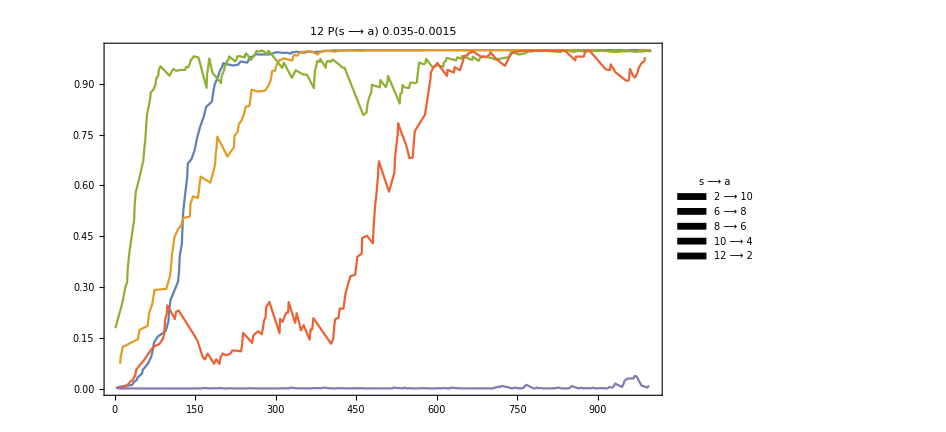

```mathematica
evolutionProbsPercept2ActionTMP=currentProbPercept2Action⟦Position[possiblePairs,#]⟦1,1⟧⟧&/@possiblePairs;
evolutionProbsPercept2Action=Table[If[evolutionProbsPercept2ActionTMP⟦pair,iter⟧≠0.,{iter,evolutionProbsPercept2ActionTMP⟦pair,iter⟧},Nothing],{pair,NsampledPairs},{iter,Niterations}];

ListPlot[evolutionProbsPercept2Action,
PlotRange->{0,1},
ImageSize->700,
Frame->True,
Joined->True,
BaseStyle->16,
PlotLegends->Placed[SwatchLegend[
Style[(""<>ToString[#⟦1⟧]<>" ⟶ "<>ToString[#⟦2⟧]),14]&/@possiblePairs,
LegendLabel->Style["  s ⟶ a",15],
LegendMarkers->Graphics[Disk[]],
LegendFunction->(Framed[#,Background->LightGray]&)],{Bottom,Right}],
FrameTicks->{Automatic,Automatic},
PlotLabel->ToString@DIM<>"          P(s ⟶ a)         "<>ToString@ϕupdateINIT<>"-"<>ToString@ϕupdateFIN
]
```

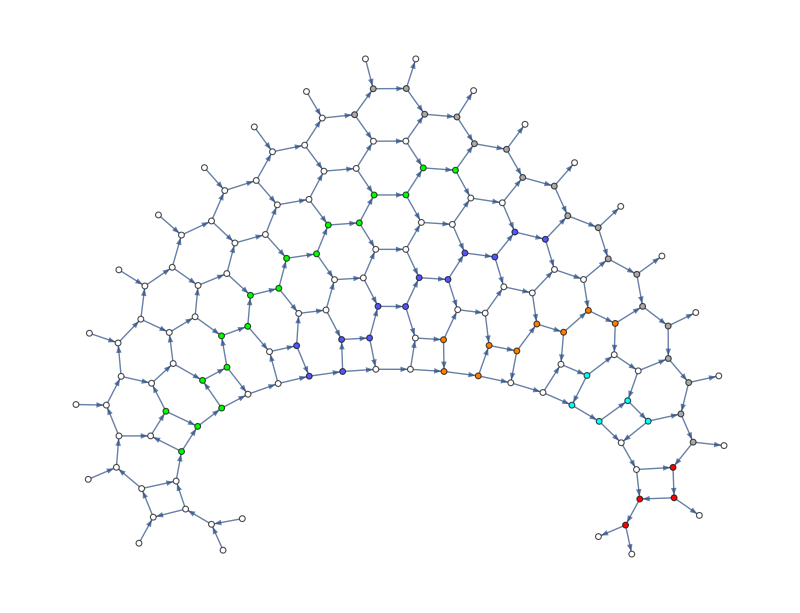

```mathematica
colors={Green,Lighter@Blue,Orange,Cyan,Red,Pink,Yellow,Magenta,Brown};

allLeakingNodesAllPairs=allLeakingNodes⟦possiblePairs⟦#,1⟧,possiblePairs⟦#,2⟧,2⟧&/@Range@NsampledPairs;

highlightedNodes=Flatten@Table[Style[allLeakingNodesAllPairs⟦pathN,node⟧,colors⟦pathN⟧,Thick],{pathN,Length@allLeakingNodesAllPairs},{node,Length@allLeakingNodesAllPairs⟦pathN⟧}];

overlappingNodes=First/@Cases[Tally[Flatten@allLeakingNodesAllPairs],u_/;u[[2]]≥2];
highlightedOverlappingNodes=Flatten@Table[Style[node,Lighter@Gray],{node,overlappingNodes}];

otherNodes=Style[#,White]&/@Complement[VertexList@directedGraph,DeleteDuplicates@Flatten@allLeakingNodesAllPairs];

HighlightGraph[Graph@directedGraph,
Join[highlightedNodes,highlightedOverlappingNodes,otherNodes],
GraphLayout->"SpringEmbedding",
ImageSize->800
]
```

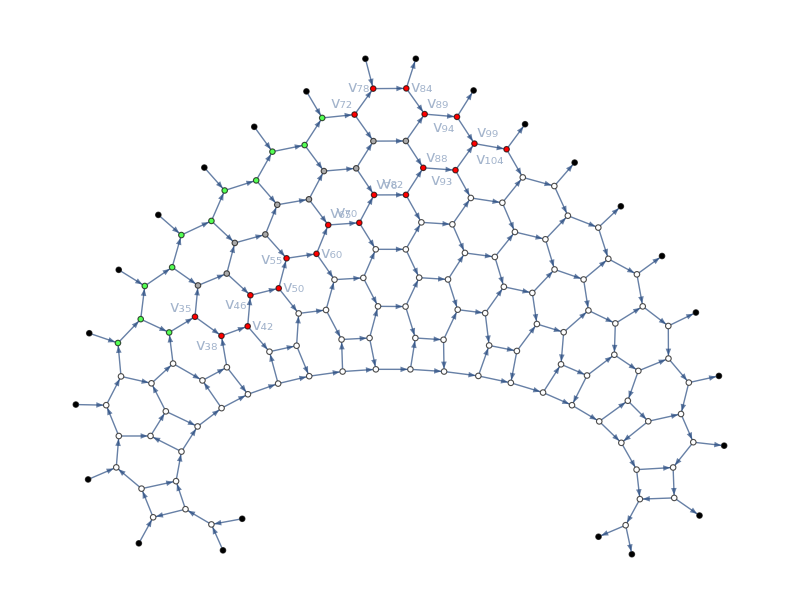

```mathematica
inMode=6;
outMode=10;

{lightCone,leakingNodes}=allLeakingNodes⟦inMode,outMode⟧;

highlightedNodes=Join[
Style[#,White]&/@Range[DIM+1,nVertices-DIM],
Style[#,Lighter@Gray]&/@Complement[Intersection[VertexOutComponent[directedGraph,{inMode}],VertexInComponent[directedGraph,{nVertices-DIM+outMode}]],lightCone],
Style[#,Lighter@Green]&/@Complement[lightCone,leakingNodes],
Style[#,Red]&/@leakingNodes,
Style[#,Black]&/@Range@DIM,
Style[#,Black]&/@Range[nVertices-DIM+1,nVertices]
];

causalDiamondGraphMinimal=HighlightGraph[directedGraph,
highlightedNodes,
VertexSize->Medium,
GraphLayout->"SpringEmbedding",
ImageSize->800,
VertexLabels->Table[i->Style[Subscript[v, i],16],{i,(*VertexList@*)leakingNodes}]
]
```

#### Circuits with random connectivity

```mathematica
(*minDIM=1;
maxDIM=17;
allLeakingNodesRandomDIMS=ConstantArray[{},{1+maxDIM-minDIM}];
DIMindex=0;

Do[
DIMindex++;
Block[{directedGraph,nVertices,graphINFO},
graphINFO=getGraph[DIM,Method->"Random"];
directedGraph=DeleteDuplicates@graphINFO⟦1⟧;
nVertices=VertexCount@directedGraph;
While[Times@@Flatten@Table[Length@FindPath[graphINFO⟦1⟧,inMode,nVertices-DIM+outMode],{inMode,DIM},{outMode,DIM}]==0,
graphINFO=getGraph[DIM,Method->"Random"];
Print[DIM,"  Trying again"]
];
allLeakingNodesRandomDIMS⟦DIMindex⟧={graphINFO,ParallelTable[findLeakingNodes[DIM,graphINFO,inMode,nVertices-DIM+outMode],{inMode,DIM},{outMode,DIM}]};
]
,{DIM,minDIM,maxDIM}
];

Put[allLeakingNodesRandomDIMS,myPATHimport<>"allLeakingNodesRandomDIMS.txt"]*)
```

```mathematica
allLeakingNodesRandomDIMS=Get[myPATHimport<>"allLeakingNodesRandomDIMS.txt"];
```

```mathematica
DIM=14;(* From minDIM to maxDIM, see above. *)

graphINFO=allLeakingNodesRandomDIMS⟦DIM⟧⟦1⟧;
allLeakingNodes=allLeakingNodesRandomDIMS⟦DIM⟧⟦2⟧;

(*graphINFO=getGraph[DIM,Method->"Random"];*)
directedGraph=graphINFO⟦1⟧;
nVertices=VertexCount@directedGraph;


HighlightGraph[Graph@directedGraph/.(xxx_->yyy_)->(xxx<->yyy),
Join[
Style[#,White]&/@Range[DIM+1,nVertices-DIM],
Style[#,Green]&/@Range@DIM,
Style[#,Blue]&/@Range[nVertices-DIM+1,nVertices]
],
ImageSize->800
]


cellPositions=graphINFO⟦2,2;;-2⟧;

cellsUpara=Table[
Join[#⟦s,k⟧,{1,Subscript[P, s,k,graphINFO⟦3,s+1,k⟧]}](* There are three indices here: 1) s = layer in the circuit; 2) k = position of the phase shifter in the layer; 3) MZ label in each layer. *)
,{s, Length@#},{k,Length[#⟦s⟧]}]&@cellPositions;

layersPara=Table[Normal@chipLayer[DIM,cellsUpara,layer],{layer,Length@cellPositions}];

phaseSettingsInitialization=Map[(#->RandomReal[{0,2π}])&,Table[
Subscript[P, s,k,graphINFO⟦3,s+1,k⟧] ,{s,Length@cellPositions},{k,Length[cellPositions⟦s⟧]}],{2}
];
```

-Graphics-

```mathematica
Niterations=1000;

phaseSettings=phaseSettingsInitialization;

nodesLayer=graphINFO⟦3,2;;-2⟧;
posNodesInLayers=Table[Association[(nodesLayer⟦l,#⟧->#)&/@Range@Length@cellPositions⟦l⟧],{l,Length@cellPositions}];

fromNodetoLayer=Association@Flatten@Table[nodesLayer⟦l,i⟧->l,{l,Length@nodesLayer},{i,Length@nodesLayer⟦l⟧}];
updateCausalDiamondSequence=Table[
Sort[Join[(<|(#-> {x})&/@Range[Min@#,Max@#]&@Keys@#|>),#]&@GroupBy[allLeakingNodes⟦inMode,outMode,1⟧,fromNodetoLayer],#1>#2&]
,{inMode,DIM},{outMode,DIM}];
updateCDstartingLayer=Map[Min@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDfinalLayer=Map[Max@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDnodesLayerwise=Map[Values,updateCausalDiamondSequence,{2}];


ϕupdateINIT=0.03;
ϕupdateFIN=0.002;
ϕupdate=ϕupdateINIT;
ϕstep=(ϕupdateINIT-ϕupdateFIN)/Niterations;
ϕupdate-=ϕstep;

NsampledPairs=Floor@(DIM/2)-3;(* The more pairs are rewarded, the worse the performance gets. *)
inModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
outModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
possiblePairs=Sort[{inModes⟦#⟧,outModes⟦#⟧}&/@Range@NsampledPairs];
Print["These are the percept/action pairs that are rewarded: ",possiblePairs];

lessProbablePairIndex=RandomChoice@Range@NsampledPairs;

currentProbPercept2Action=ConstantArray[0.,{NsampledPairs,Niterations}];


Do[

{s,a}=possiblePairs⟦RandomChoice[{0.9,0.1}->{lessProbablePairIndex,RandomChoice[Range@NsampledPairs]}]⟧;
indexNextPair=Position[possiblePairs,{s,a}]⟦1,1⟧;

If[updateCDstartingLayer⟦s,a⟧≠1,
layersFixed=Dot@@Reverse@Table[layersPara⟦layer⟧/.phaseSettings⟦layer⟧,{layer,updateCDstartingLayer⟦s,a⟧-1}];,
layersFixed=IdentityMatrix@DIM
];
layersVariable=layersPara⟦updateCDstartingLayer⟦s,a⟧;;⟧;

updateResult=updateCausalDiamond[layersFixed,layersVariable,
updateCausalDiamondSequence⟦s,a⟧,updateCDstartingLayer⟦s,a⟧, updateCDfinalLayer⟦s,a⟧,
posNodesInLayers,phaseSettings,ϕupdate,{s,a}];

phaseSettings=updateResult⟦1⟧;
u=updateResult⟦2⟧;
currentProbPercept2Action⟦indexNextPair,iter⟧=abs2@u⟦a,s⟧;
lessProbablePairIndex=With[{probs=(abs2[u⟦Sequence[#⟦2⟧,#⟦1⟧]⟧])&/@possiblePairs},
Position[probs,Min@probs]⟦1,1⟧
];
,

{iter,Niterations}
];

(* Performance significantly depends on how many pairs are optimized, and the circuit connectivity. It might be impossible to optimize at the same time two or more pairs, if their updates compete with each other. *)
```

{{2,12},{4,14},{8,10},{10,4}}

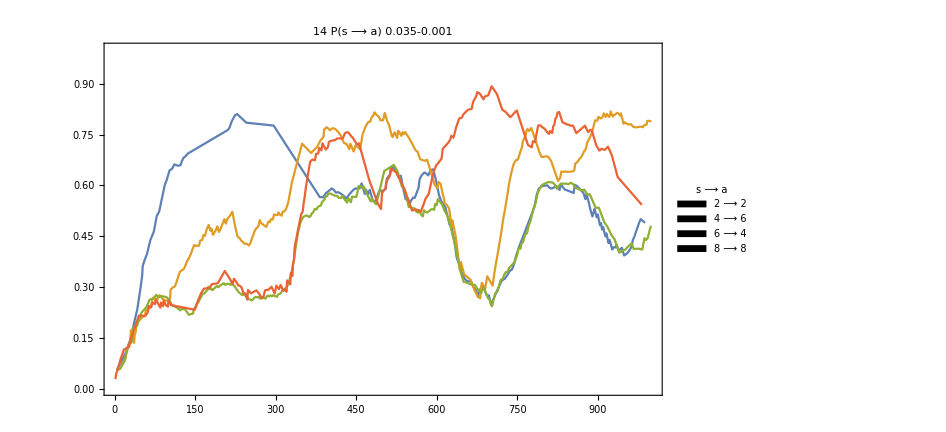

```mathematica
evolutionProbsPercept2ActionTMP=currentProbPercept2Action[[Position[possiblePairs,#]⟦1,1⟧]]&/@possiblePairs;
evolutionProbsPercept2Action=Table[If[evolutionProbsPercept2ActionTMP⟦pair,iter⟧≠0.,{iter,evolutionProbsPercept2ActionTMP⟦pair,iter⟧},Nothing],{pair,NsampledPairs},{iter,Niterations}];

ListPlot[evolutionProbsPercept2Action,
PlotRange->{0,1},
ImageSize->700,
Frame->True,
Joined->True,
BaseStyle->18,
PlotLegends->Placed[SwatchLegend[
Style[(""<>ToString[#⟦1⟧]<>" ⟶ "<>ToString[#⟦2⟧]),16]&/@possiblePairs,
LegendLabel->Style["  s ⟶ a\n",17],
LegendMarkers->Graphics[Disk[]],
LegendFunction->(Framed[#,Background->LightGray]&)],{Bottom,Right}],
FrameTicks->{Automatic,Automatic},
PlotLabel->ToString@DIM<>"          P(s ⟶ a)         "<>ToString@ϕupdateINIT<>"-"<>ToString@ϕupdateFIN
]
```

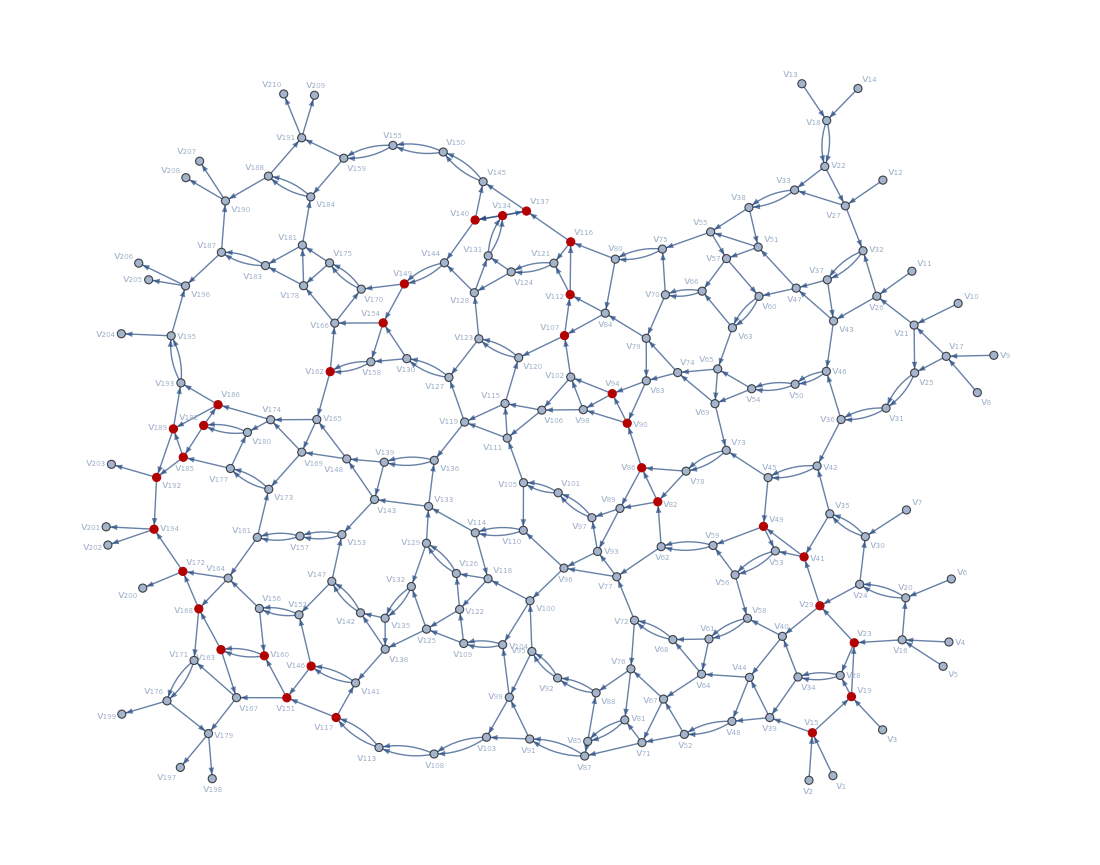

```mathematica
HighlightGraph[directedGraph,
Join[allLeakingNodes⟦possiblePairs⟦1,1⟧,possiblePairs⟦1,2⟧,1⟧],
ImageSize->1100,
GraphLayout->"SpringEmbedding",
VertexLabels->Table[i->Subscript[v, i],{i,nVertices}]
]
```

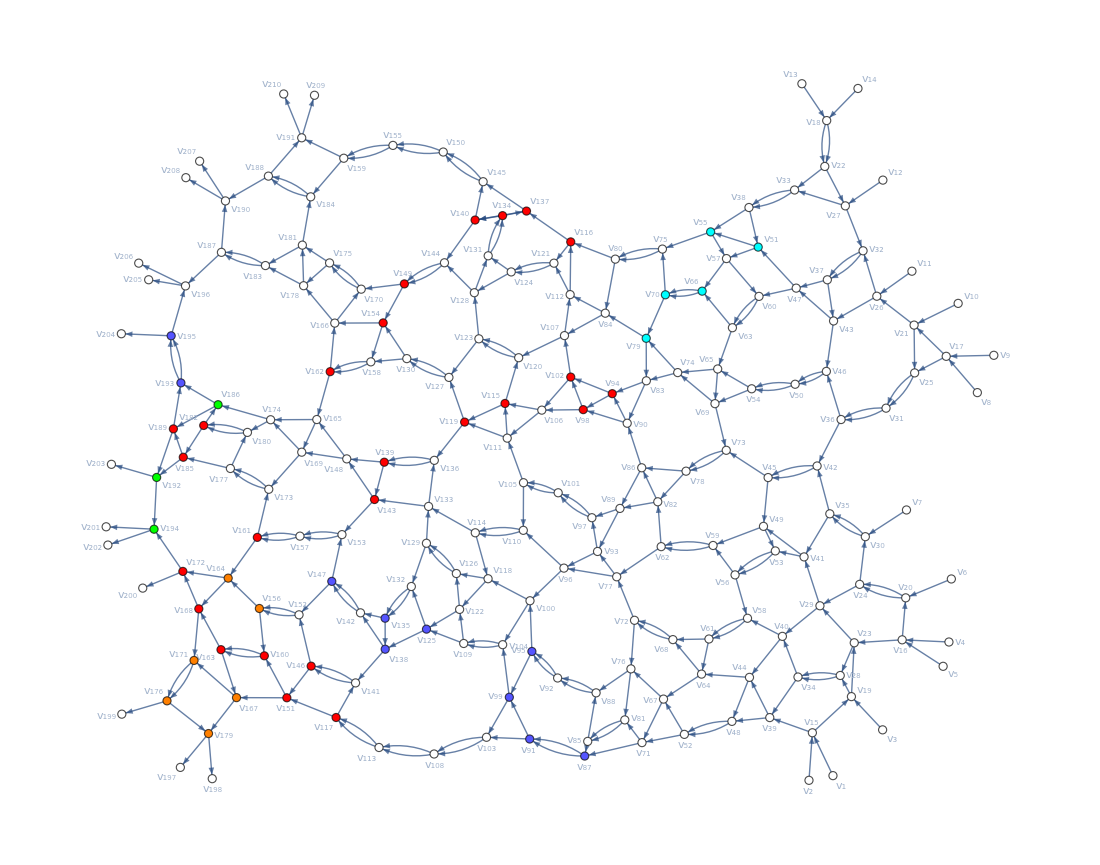

```mathematica
colors={Green,Lighter@Blue,Orange,Cyan,Pink,Yellow,Magenta,Brown};

allLeakingNodesAllPairs=allLeakingNodes⟦possiblePairs⟦#,1⟧,possiblePairs⟦#,2⟧,2⟧&/@Range@NsampledPairs;

highlightedNodes=Flatten@Table[Style[allLeakingNodesAllPairs⟦pathN,node⟧,colors⟦pathN⟧,Thick],{pathN,Length@allLeakingNodesAllPairs},{node,Length@allLeakingNodesAllPairs⟦pathN⟧}];

overlappingNodes=First/@Cases[Tally[Flatten@allLeakingNodesAllPairs],u_/;u[[2]]≥2];
highlightedOverlappingNodes=Flatten@Table[Style[node,Red],{node,overlappingNodes}];

otherNodes=Style[#,White]&/@Complement[VertexList@directedGraph,DeleteDuplicates@Flatten@allLeakingNodesAllPairs];

HighlightGraph[directedGraph,
Join[highlightedNodes,highlightedOverlappingNodes,otherNodes],
ImageSize->1100,
GraphLayout->"SpringEmbedding",
VertexLabels->Table[i->Subscript[v, i],{i,nVertices}]
]
```

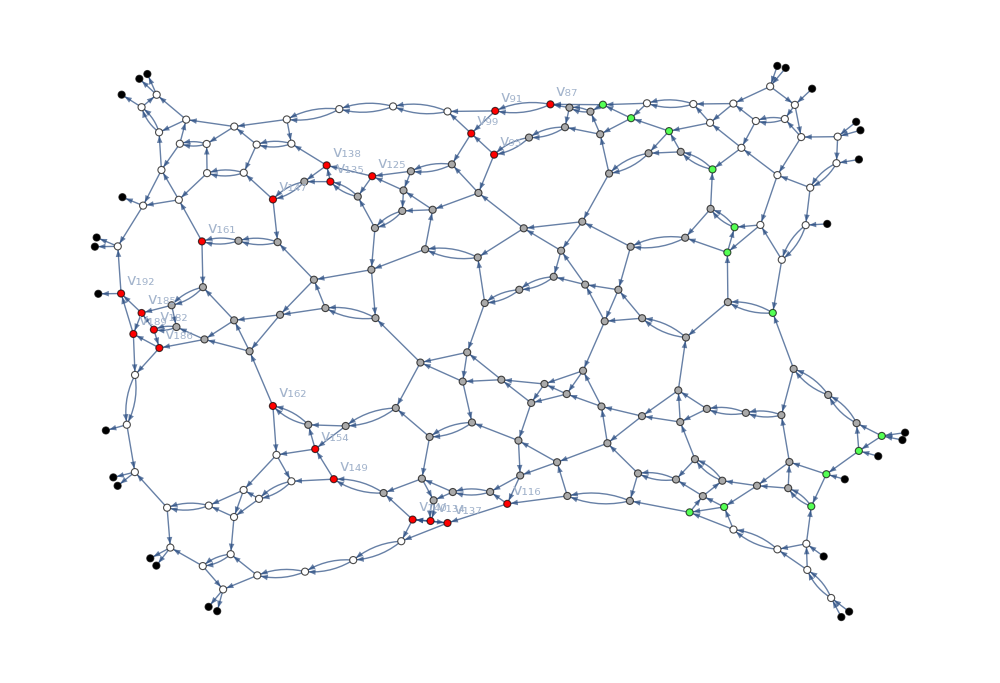

```mathematica
inMode=9;
outMode=7;

{lightCone,leakingNodes}=allLeakingNodes⟦inMode,outMode⟧;

g=directedGraph/.(xxx_->yyy_)->(xxx<->yyy);


highlightedNodes=Join[
Style[#,White]&/@Range[DIM+1,nVertices-DIM],
Style[#,Lighter@Gray]&/@Complement[Intersection[VertexOutComponent[directedGraph,{inMode}],VertexInComponent[directedGraph,{nVertices-DIM+outMode}]],lightCone],
Style[#,Lighter@Green]&/@Complement[lightCone,leakingNodes],
Style[#,Red]&/@leakingNodes,
Style[#,Black]&/@Range@DIM,
Style[#,Black]&/@Range[nVertices-DIM+1,nVertices]
];

causalDiamondGraphMinimal=HighlightGraph[Graph@directedGraph,
highlightedNodes,
ImageSize->1000,
VertexLabels->Table[i->Style[Subscript[v, i],16],{i,(*VertexList@*)leakingNodes}]
]
```

#### Multiple wavelengths λ

```mathematica
(* This function studies the behaviour of the variational algorithm based on causal diamonds when one injects photons with different wavelength λ. Research question: Does the approach work for multiple λ at the same time? *)

(* For comments to the function below, we refer to Section "Functions", where "updateCausalDiamond(.)" was introduced. *)

(* This function currently works with 3 wavelengths (and it can be extended with little adjustments). Blocks of code are copy-pasted and adjusted to address each λ independently. It basically applies parts of the function "updateCausalDiamond(.)" to each λ and combines the results in a single figure of merit (here, the geometric mean). *)


updateCausalDiamondLambda[
layersFixedLambda_,
layersParaLambda_,
updateCausalDiamondSequence_,
startingLayer_,finalLayer_,
posNodesInLayers_,
phase2changeLambda_,
ϕshift_,
pairSA_
]:=Module[{
IN,OUT,
updateCDnodesLayerwise,
layersFixedPartBeforeLambda=layersFixedLambda,
layersFixedPartAfterLambda,
newLayer,
nEffLayers,
ϕtmpLambda=phase2changeLambda,
newTargetValues1,newTargetValues2,
currentU,currentTargetValue,currentLayerIndex,
δ,l,ϕlayer,nodePos,
newU1,newU2,
newUa1,newUa2,newUa3,
newUb1,newUb2,newUb3,
currentU1,currentU2,currentU3
},


{IN,OUT}=pairSA;
updateCDnodesLayerwise=Values@updateCausalDiamondSequence;
nEffLayers=finalLayer-startingLayer+1;
layersFixedPartAfterLambda=Table[Dot@@Reverse@Table[
layersParaLambda⟦λindex,1+layer⟧/.ϕtmpLambda⟦λindex,startingLayer+layer⟧
,{layer,1,nEffLayers-1}],{λindex,3}];

δ=ϕshift;



Do[

l=startingLayer+currentLayerIndex-1;

Do[

nodePos=posNodesInLayers⟦l⟧[node];

If[Not[MissingQ@nodePos],

currentU1=layersFixedPartAfterLambda[[1]].(layersParaLambda⟦1,currentLayerIndex⟧/.ϕtmpLambda⟦1,l⟧).layersFixedPartBeforeLambda[[1]];
currentU2=layersFixedPartAfterLambda[[2]].(layersParaLambda⟦2,currentLayerIndex⟧/.ϕtmpLambda⟦2,l⟧).layersFixedPartBeforeLambda[[2]];
currentU3=layersFixedPartAfterLambda[[3]].(layersParaLambda⟦3,currentLayerIndex⟧/.ϕtmpLambda⟦3,l⟧).layersFixedPartBeforeLambda[[3]];
currentTargetValue=(abs2@currentU1⟦OUT,IN⟧abs2@currentU2⟦OUT,IN⟧abs2@currentU3⟦OUT,IN⟧)^(1/3);


(* -------------------- *)


ϕlayer=ϕtmpLambda⟦1,l⟧;

ϕlayer⟦nodePos,2⟧+=0.995δ;
newLayer=layersParaLambda⟦1,currentLayerIndex⟧/.ϕlayer;
newUa1=layersFixedPartAfterLambda[[1]].newLayer.layersFixedPartBeforeLambda[[1]];

ϕlayer=ϕtmpLambda⟦2,l⟧;

ϕlayer⟦nodePos,2⟧+=δ;
newLayer=layersParaLambda⟦2,currentLayerIndex⟧/.ϕlayer;
newUa2=layersFixedPartAfterLambda[[2]].newLayer.layersFixedPartBeforeLambda[[2]];

ϕlayer=ϕtmpLambda⟦3,l⟧;

ϕlayer⟦nodePos,2⟧+=1.005δ;
newLayer=layersParaLambda⟦3,currentLayerIndex⟧/.ϕlayer;
newUa3=layersFixedPartAfterLambda[[3]].newLayer.layersFixedPartBeforeLambda[[3]];

newTargetValues1=(abs2@newUa1⟦OUT,IN⟧abs2@newUa2⟦OUT,IN⟧abs2@newUa3⟦OUT,IN⟧)^(1/3);


(* -------------------- *)


ϕlayer=ϕtmpLambda⟦1,l⟧;

ϕlayer⟦nodePos,2⟧-=0.995δ;
newLayer=layersParaLambda⟦1,currentLayerIndex⟧/.ϕlayer;
newUb1=layersFixedPartAfterLambda[[1]].newLayer.layersFixedPartBeforeLambda[[1]];

ϕlayer=ϕtmpLambda⟦2,l⟧;

ϕlayer⟦nodePos,2⟧-=δ;
newLayer=layersParaLambda⟦2,currentLayerIndex⟧/.ϕlayer;
newUb2=layersFixedPartAfterLambda[[2]].newLayer.layersFixedPartBeforeLambda[[2]];

ϕlayer=ϕtmpLambda⟦3,l⟧;

ϕlayer⟦nodePos,2⟧-=1.005δ;
newLayer=layersParaLambda⟦3,currentLayerIndex⟧/.ϕlayer;
newUb3=layersFixedPartAfterLambda[[3]].newLayer.layersFixedPartBeforeLambda[[3]];

newTargetValues2=(abs2@newUb1⟦OUT,IN⟧abs2@newUb2⟦OUT,IN⟧abs2@newUb3⟦OUT,IN⟧)^(1/3);


(* -------------------- *)


Which[
currentTargetValue>newTargetValues1&&currentTargetValue>newTargetValues2,
Nothing,
newTargetValues1>newTargetValues2,
ϕtmpLambda⟦1,l,nodePos,2⟧+=0.995δ;
ϕtmpLambda⟦2,l,nodePos,2⟧+=δ;
ϕtmpLambda⟦3,l,nodePos,2⟧+=1.005δ;,
newTargetValues1≤newTargetValues2,
ϕtmpLambda⟦1,l,nodePos,2⟧-=0.995δ;
ϕtmpLambda⟦2,l,nodePos,2⟧-=δ;
ϕtmpLambda⟦3,l,nodePos,2⟧-=1.005δ;
],

Nothing
];

,{node,updateCDnodesLayerwise⟦currentLayerIndex⟧}
];


(* -------------------- *)
layersFixedPartBeforeLambda=Table[(layersParaLambda⟦λindex,currentLayerIndex⟧/.ϕtmpLambda⟦λindex,l⟧).layersFixedPartBeforeLambda⟦λindex⟧,{λindex,3}];

If[currentLayerIndex<nEffLayers,
layersFixedPartAfterLambda=Table[Chop[layersFixedPartAfterLambda⟦λindex⟧.Inverse[layersParaLambda⟦λindex,currentLayerIndex+1⟧/.ϕtmpLambda⟦λindex,l+1⟧]],{λindex,3}]
];
(* -------------------- *)


,{currentLayerIndex,nEffLayers}
];

(*currentU=layersFixedPartBeforeLambda;*)

Return[{ϕtmpLambda,layersFixedPartBeforeLambda}]
];
```

```mathematica
allLeakingNodesDIMS=Get[myPATHimport<>"allLeakingNodes2PSDIMS.txt"];
```

```mathematica
DIM=9;
graphINFO=getGraph[DIM,Method->"Square2PS"];

allLeakingNodes=allLeakingNodesDIMS⟦DIM⟧;

cellPositions=graphINFO⟦2,2;;-2⟧;

cellsUpara=Table[
Join[#⟦s,k⟧,{1,Subscript[P, s,k,graphINFO⟦3,s+1,k⟧]}](* There are three indices here: 1) s = layer in the circuit; 2) k = position of the phase shifter in the layer; 3) MZ label in each layer. *)
,{s, Length@#},{k,Length[#⟦s⟧]}]&@cellPositions;

layersParaλ=Table[Normal@chipLayer[DIM,cellsUpara,layer],{λindex,3},{layer,Length@cellPositions}];

randomSettings=Table[RandomReal[{0,2π}],{s,Length@cellPositions},{k,Length[cellPositions⟦s⟧]}];

phaseSettingsInitialization=Table[
Subscript[P, s,k,graphINFO⟦3,s+1,k⟧] -># randomSettings⟦s,k⟧,{s,Length@cellPositions},{k,Length[cellPositions⟦s⟧]}]&/@{0.995,1,1.005}
```

{{{P_(1,1,10)→1.02531,P_(1,2,11)→1.03418,P_(1,3,12)→2.59367,P_(1,4,13)→5.87587},{P_(2,1,14)→3.08915,P_(2,2,15)→5.37563,P_(2,3,16)→5.45105,P_(2,4,17)→1.81356},{P_(3,1,18)→3.38443,P_(3,2,19)→0.839454,P_(3,3,20)→3.19924,P_(3,4,21)→3.80657},{P_(4,1,22)→3.3651,P_(4,2,23)→4.58885,P_(4,3,24)→1.4734,P_(4,4,25)→3.38382},{P_(5,1,26)→4.50915,P_(5,2,27)→2.13101,P_(5,3,28)→1.72661,P_(5,4,29)→0.311545},{P_(6,1,30)→4.9133,P_(6,2,31)→4.20293,P_(6,3,32)→3.81816,P_(6,4,33)→5.92327},{P_(7,1,34)→0.805411,P_(7,2,35)→4.43854,P_(7,3,36)→2.73878,P_(7,4,37)→1.07872},{P_(8,1,38)→1.58056,P_(8,2,39)→1.12601,P_(8,3,40)→0.666938,P_(8,4,41)→4.86405},{P_(9,1,42)→3.53591,P_(9,2,43)→3.99736,P_(9,3,44)→0.0681532,P_(9,4,45)→3.49854},{P_(10,1,46)→1.34534,P_(10,2,47)→3.91193,P_(10,3,48)→4.71944,P_(10,4,49)→1.96285},{P_(11,1,50)→5.33042,P_(11,2,51)→3.44518,P_(11,3,52)→0.900653,P_(11,4,53)→0.813974},{P_(12,1,54)→1.19433,P_(12,2,55)→4.12677,P_(12,3,56)→4.25279,P_(12,4,57)→4.27186},{P_(13,1,58)→2.21145,P_(13,2,59)→5.1487,P_(13,3,60)→1.15277,P_(13,4,61)→5.93181},{P_(14,1,62)→3.85091,P_(14,2,63)→1.29562,P_(14,3,64)→0.419969,P_(14,4,65)→4.56291},{P_(15,1,66)→6.20974,P_(15,2,67)→3.97256,P_(15,3,68)→4.8144,P_(15,4,69)→0.575542},{P_(16,1,70)→0.954253,P_(16,2,71)→0.779163,P_(16,3,72)→2.8622,P_(16,4,73)→0.577943},{P_(17,1,74)→1.77162,P_(17,2,75)→2.55818,P_(17,3,76)→5.56258,P_(17,4,77)→1.29247},{P_(18,1,78)→0.532645,P_(18,2,79)→2.35441,P_(18,3,80)→0.485469,P_(18,4,81)→4.17967}},{{P_(1,1,10)→1.03046,P_(1,2,11)→1.03937,P_(1,3,12)→2.6067,P_(1,4,13)→5.9054},{P_(2,1,14)→3.10468,P_(2,2,15)→5.40264,P_(2,3,16)→5.47844,P_(2,4,17)→1.82267},{P_(3,1,18)→3.40144,P_(3,2,19)→0.843672,P_(3,3,20)→3.21532,P_(3,4,21)→3.8257},{P_(4,1,22)→3.38201,P_(4,2,23)→4.61191,P_(4,3,24)→1.4808,P_(4,4,25)→3.40083},{P_(5,1,26)→4.5318,P_(5,2,27)→2.14172,P_(5,3,28)→1.73528,P_(5,4,29)→0.31311},{P_(6,1,30)→4.93799,P_(6,2,31)→4.22405,P_(6,3,32)→3.83734,P_(6,4,33)→5.95303},{P_(7,1,34)→0.809458,P_(7,2,35)→4.46084,P_(7,3,36)→2.75254,P_(7,4,37)→1.08414},{P_(8,1,38)→1.58851,P_(8,2,39)→1.13167,P_(8,3,40)→0.67029,P_(8,4,41)→4.88849},{P_(9,1,42)→3.55368,P_(9,2,43)→4.01745,P_(9,3,44)→0.0684957,P_(9,4,45)→3.51612},{P_(10,1,46)→1.3521,P_(10,2,47)→3.93159,P_(10,3,48)→4.74315,P_(10,4,49)→1.97271},{P_(11,1,50)→5.3572,P_(11,2,51)→3.46249,P_(11,3,52)→0.905179,P_(11,4,53)→0.818064},{P_(12,1,54)→1.20033,P_(12,2,55)→4.1475,P_(12,3,56)→4.27416,P_(12,4,57)→4.29332},{P_(13,1,58)→2.22256,P_(13,2,59)→5.17457,P_(13,3,60)→1.15857,P_(13,4,61)→5.96162},{P_(14,1,62)→3.87026,P_(14,2,63)→1.30213,P_(14,3,64)→0.42208,P_(14,4,65)→4.58584},{P_(15,1,66)→6.24095,P_(15,2,67)→3.99252,P_(15,3,68)→4.83859,P_(15,4,69)→0.578435},{P_(16,1,70)→0.959048,P_(16,2,71)→0.783078,P_(16,3,72)→2.87659,P_(16,4,73)→0.580847},{P_(17,1,74)→1.78052,P_(17,2,75)→2.57104,P_(17,3,76)→5.59053,P_(17,4,77)→1.29896},{P_(18,1,78)→0.535322,P_(18,2,79)→2.36624,P_(18,3,80)→0.487909,P_(18,4,81)→4.20067}},{{P_(1,1,10)→1.03561,P_(1,2,11)→1.04457,P_(1,3,12)→2.61974,P_(1,4,13)→5.93493},{P_(2,1,14)→3.1202,P_(2,2,15)→5.42966,P_(2,3,16)→5.50583,P_(2,4,17)→1.83178},{P_(3,1,18)→3.41845,P_(3,2,19)→0.847891,P_(3,3,20)→3.23139,P_(3,4,21)→3.84483},{P_(4,1,22)→3.39892,P_(4,2,23)→4.63497,P_(4,3,24)→1.4882,P_(4,4,25)→3.41783},{P_(5,1,26)→4.55446,P_(5,2,27)→2.15243,P_(5,3,28)→1.74396,P_(5,4,29)→0.314676},{P_(6,1,30)→4.96268,P_(6,2,31)→4.24517,P_(6,3,32)→3.85653,P_(6,4,33)→5.9828},{P_(7,1,34)→0.813505,P_(7,2,35)→4.48314,P_(7,3,36)→2.76631,P_(7,4,37)→1.08956},{P_(8,1,38)→1.59645,P_(8,2,39)→1.13733,P_(8,3,40)→0.673641,P_(8,4,41)→4.91293},{P_(9,1,42)→3.57145,P_(9,2,43)→4.03754,P_(9,3,44)→0.0688382,P_(9,4,45)→3.5337},{P_(10,1,46)→1.35886,P_(10,2,47)→3.95125,P_(10,3,48)→4.76687,P_(10,4,49)→1.98258},{P_(11,1,50)→5.38399,P_(11,2,51)→3.47981,P_(11,3,52)→0.909705,P_(11,4,53)→0.822154},{P_(12,1,54)→1.20633,P_(12,2,55)→4.16824,P_(12,3,56)→4.29553,P_(12,4,57)→4.31479},{P_(13,1,58)→2.23368,P_(13,2,59)→5.20044,P_(13,3,60)→1.16436,P_(13,4,61)→5.99143},{P_(14,1,62)→3.88961,P_(14,2,63)→1.30864,P_(14,3,64)→0.42419,P_(14,4,65)→4.60877},{P_(15,1,66)→6.27215,P_(15,2,67)→4.01248,P_(15,3,68)→4.86279,P_(15,4,69)→0.581327},{P_(16,1,70)→0.963843,P_(16,2,71)→0.786993,P_(16,3,72)→2.89097,P_(16,4,73)→0.583751},{P_(17,1,74)→1.78942,P_(17,2,75)→2.58389,P_(17,3,76)→5.61848,P_(17,4,77)→1.30546},{P_(18,1,78)→0.537999,P_(18,2,79)→2.37808,P_(18,3,80)→0.490349,P_(18,4,81)→4.22168}}}

```mathematica
Niterations=600;

phaseSettingsλ=phaseSettingsInitialization;

nodesLayer=graphINFO⟦3,2;;-2⟧;
posNodesInLayers=Table[Association[(nodesLayer[[l,#]]->#)&/@Range@Length@cellPositions⟦l⟧],{l,Length@cellPositions}];

fromNodetoLayer=Association@Flatten@Table[nodesLayer[[l,i]]->l,{l,Length@nodesLayer},{i,Length@nodesLayer[[l]]}];
updateCausalDiamondSequence=Table[
Sort[Join[(<|(#-> {x})&/@Range[Min@#,Max@#]&@Keys@#|>),#]&@GroupBy[allLeakingNodes⟦inMode,outMode,2⟧,fromNodetoLayer],#1>#2&]
,{inMode,DIM},{outMode,DIM}];
updateCDstartingLayer=Map[Min@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDfinalLayer=Map[Max@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDnodesLayerwise=Map[Values,updateCausalDiamondSequence,{2}];

ϕupdateINIT=0.033;
ϕupdateFIN=0.002;
ϕupdate=ϕupdateINIT;
ϕstep=(ϕupdateINIT-ϕupdateFIN)/Niterations;
ϕupdate-=ϕstep;

NsampledPairs=Floor@(DIM/2)-1;
inModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
outModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
possiblePairs=Sort[{inModes⟦#⟧,outModes⟦#⟧}&/@Range@NsampledPairs]

currentProbPercept2Action=ConstantArray[0.,{NsampledPairs,Niterations}];



Do[

{s,a}=RandomChoice[possiblePairs];
indexNextPair=Position[possiblePairs,{s,a}]⟦1,1⟧;

layersFixedλ=ConstantArray[{},3];

Table[
If[updateCDstartingLayer⟦s,a⟧≠1,
layersFixedλ⟦λindex⟧=Dot@@Reverse@Table[layersParaλ⟦λindex,layer⟧/.phaseSettingsλ⟦λindex,layer⟧,{layer,updateCDstartingLayer⟦s,a⟧-1}];,
layersFixedλ⟦λindex⟧=IdentityMatrix@DIM
],{λindex,3}
];
layersVariableλ=Table[layersParaλ⟦λindex,updateCDstartingLayer⟦s,a⟧;;⟧,{λindex,3}];

updateResult=updateCausalDiamondLambda[layersFixedλ,layersVariableλ,
updateCausalDiamondSequence⟦s,a⟧,updateCDstartingLayer⟦s,a⟧, updateCDfinalLayer⟦s,a⟧,
posNodesInLayers,phaseSettingsλ,ϕupdate,{s,a}];

phaseSettingsλ=updateResult⟦1⟧;
u=updateResult⟦2⟧;
currentProbPercept2Action⟦indexNextPair,iter⟧=(abs2@u⟦1,a,s⟧abs2@u⟦2,a,s⟧abs2@u⟦3,a,s⟧)^(1/3);
,

{iter,Niterations}
];
```

{{4,8},{6,6},{8,4}}

```mathematica
MatrixForm/@Chop[abs2@u,10^-4]
```

{(0.820655 | 0.000130647 | 0.0531776 | 0.0326337 | 0.0879061 | 0 | 0.00515011 | 0.000310849 | 0
0.000298795 | 0.000259186 | 0.000112077 | 0 | 0 | 0 | 0.000185178 | 0.999013 | 0
0.140401 | 0.000138939 | 0.115483 | 0.101061 | 0.642135 | 0 | 0.000640762 | 0 | 0
0.000151852 | 0 | 0.000721012 | 0 | 0.000102863 | 0.998794 | 0 | 0 | 0
0.0381118 | 0 | 0.1802 | 0.50767 | 0.15668 | 0.000464835 | 0.116641 | 0 | 0.00013419
0.000123249 | 0.99941 | 0 | 0 | 0 | 0 | 0 | 0.000253244 | 0
0 | 0 | 0.0274351 | 0.118307 | 0.00327649 | 0.000171377 | 0.461216 | 0 | 0.389507
0.000252355 | 0 | 0.531519 | 0.153929 | 0.107668 | 0.000265917 | 0.175817 | 0.000108822 | 0.0304267
0 | 0 | 0.091299 | 0.0862482 | 0.00204941 | 0.000135288 | 0.240268 | 0 | 0.579925),(0.815504 | 0 | 0.0512824 | 0.0366777 | 0.0913864 | 0 | 0.00509462 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.999925 | 0
0.142688 | 0 | 0.100487 | 0.107991 | 0.647997 | 0 | 0.000800307 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.999716 | 0.000140923 | 0 | 0
0.041432 | 0 | 0.173478 | 0.519541 | 0.163117 | 0 | 0.102392 | 0 | 0
0 | 0.999912 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.0313274 | 0.109986 | 0.00285063 | 0 | 0.47297 | 0 | 0.382777
0.000301934 | 0 | 0.552361 | 0.143078 | 0.0929531 | 0.000130027 | 0.182025 | 0 | 0.0291223
0 | 0 | 0.0910163 | 0.0826751 | 0.00161689 | 0 | 0.236573 | 0 | 0.588097),(0.809926 | 0.00014271 | 0.0491634 | 0.0408627 | 0.0946147 | 0 | 0.00501624 | 0.000175398 | 0
0 | 0.000202737 | 0.000129665 | 0 | 0 | 0.000209626 | 0.000172005 | 0.999113 | 0
0.144327 | 0.000261889 | 0.0857868 | 0.115289 | 0.653251 | 0 | 0.00106016 | 0 | 0
0.000159392 | 0 | 0.00103197 | 0 | 0.000217444 | 0.997981 | 0.000348806 | 0.000211984 | 0
0.0448687 | 0 | 0.166401 | 0.530097 | 0.169286 | 0.000182629 | 0.0889304 | 0 | 0
0.000220382 | 0.999239 | 0 | 0 | 0.000250721 | 0 | 0 | 0.000206468 | 0
0 | 0 | 0.0360866 | 0.101611 | 0.00251416 | 0 | 0.484107 | 0 | 0.375519
0.00038004 | 0 | 0.571016 | 0.133092 | 0.0784995 | 0.00143129 | 0.187793 | 0 | 0.0277148
0 | 0 | 0.0903649 | 0.078998 | 0.00129662 | 0 | 0.232566 | 0 | 0.596677)}

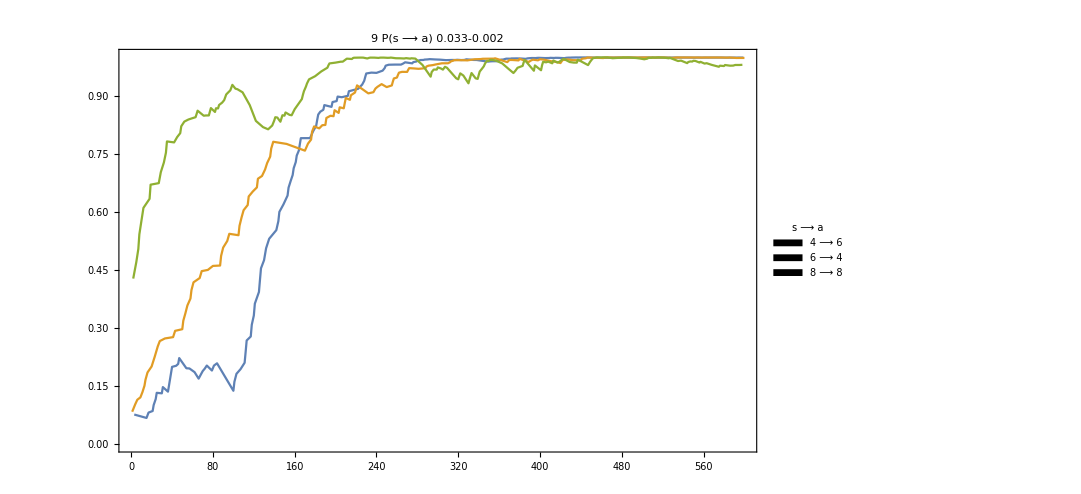

```mathematica
evolutionProbsPercept2ActionTMP=currentProbPercept2Action[[Position[possiblePairs,#]⟦1,1⟧]]&/@possiblePairs;
evolutionProbsPercept2Action=Table[If[evolutionProbsPercept2ActionTMP⟦pair,iter⟧≠0.,{iter,evolutionProbsPercept2ActionTMP⟦pair,iter⟧},Nothing],{pair,NsampledPairs},{iter,Niterations}];

ListPlot[evolutionProbsPercept2Action,
PlotRange->{0,1},
ImageSize->800,
Frame->True,
Joined->True,
BaseStyle->18,
PlotLegends->Placed[SwatchLegend[
Style[(""<>ToString[#⟦1⟧]<>" ⟶ "<>ToString[#⟦2⟧]),16]&/@possiblePairs,
LegendLabel->Style["  s ⟶ a\n",17],
LegendMarkers->Graphics[Disk[]],
LegendFunction->(Framed[#,Background->LightGray]&)],{Bottom,Right}],
FrameTicks->{Automatic,Automatic},
PlotLabel->ToString@DIM<>"          P(s ⟶ a)         "<>ToString@ϕupdateINIT<>"-"<>ToString@ϕupdateFIN
]
```

#### Partial traceability

```mathematica
(*minDIM=1;
maxDIM=30;
allLeakingNodesDIMS=ConstantArray[{},{1+maxDIM-minDIM}];
DIMindex=0;

Do[
DIMindex++;
graphINFO=getGraph[DIM,Method->"Square2PS"];
directedGraph=DeleteDuplicates@graphINFO⟦1⟧;
nVertices=VertexCount@directedGraph;
allLeakingNodesDIMS⟦DIMindex⟧=Table[findLeakingNodes[DIM,graphINFO,inMode,nVertices-DIM+outMode],{inMode,DIM},{outMode,DIM}];
,{DIM,minDIM,maxDIM}
];

Put[allLeakingNodesDIMS,myPATHimport<>"allLeakingNodes2PSDIMS.txt"]*)
```

```mathematica
allLeakingNodesDIMS=Get[myPATHimport<>"allLeakingNodes2PSDIMS.txt"];
```

```mathematica
DIM=21;

graphINFO=getGraph[DIM,Method->"Square2PS"];
directedGraph=DeleteDuplicates@graphINFO⟦1⟧;

allLeakingNodes=allLeakingNodesDIMS⟦DIM⟧;

cellPositions=graphINFO⟦2,2;;-2⟧;

cellsUpara=Table[
Join[#⟦s,k⟧,{1,Subscript[P, s,k,graphINFO⟦3,s+1,k⟧]}](* There are three indices here: 1) s = layer in the circuit; 2) k = position of the phase shifter in the layer; 3) MZ label in each layer. *)
,{s, Length@#},{k,Length[#⟦s⟧]}]&@cellPositions;

layersPara=Table[Normal@chipLayer[DIM,cellsUpara,layer],{layer,Length@cellPositions}];

phaseSettingsInitialization=Map[(#->RandomReal[{0,2π}])&,Table[
Subscript[P, s,k,graphINFO⟦3,s+1,k⟧] ,{s,Length@cellPositions},{k,Length[cellPositions⟦s⟧]}],{2}
];
```

```mathematica
Niterations=601;

phaseSettings=phaseSettingsInitialization;

nodesLayer=graphINFO⟦3,2;;-2⟧;
posNodesInLayers=Table[Association[(nodesLayer⟦l,#⟧->#)&/@Range@Length@cellPositions⟦l⟧],{l,Length@cellPositions}];

fromNodetoLayer=Association@Flatten@Table[nodesLayer⟦l,i⟧->l,{l,Length@nodesLayer},{i,Length@nodesLayer[[l]]}];
updateCausalDiamondSequence=Table[
Sort[Join[(<|(#-> {x})&/@Range[Min@#,Max@#]&@Keys@#|>),#]&@GroupBy[allLeakingNodes⟦inMode,outMode,1⟧,fromNodetoLayer],#1>#2&]
,{inMode,DIM},{outMode,DIM}];
updateCDstartingLayer=Map[Min@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDfinalLayer=Map[Max@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDnodesLayerwise=Map[Values,updateCausalDiamondSequence,{2}];


ϕupdateINIT=0.033;
ϕupdateFIN=0.002;
ϕupdate=ϕupdateINIT;
ϕstep=(ϕupdateINIT-ϕupdateFIN)/Niterations;
ϕupdate-=ϕstep;

NsampledPairs=4(*Floor@(DIM/2)*);
inModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
outModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
possiblePairs=Sort[{inModes⟦#⟧,outModes⟦#⟧}&/@Range@NsampledPairs]

currentProbPercept2Action=ConstantArray[0.,{NsampledPairs,Niterations}];

NiterationsHowManySteps=2;
NiterationsSteps={1,600}(*1+Round/@Subdivide[Niterations,NiterationsHowManySteps]*);
partialProbs=ConstantArray[{},{NsampledPairs,NiterationsHowManySteps,Round[Length@layersPara/2]}];
cont=0;


(* ---------------------------- *)

Do[

{s,a}=RandomChoice[possiblePairs];(* The same circuit is used to reinforce multiple rewarded (s,a) pairs. *)
indexNextPair=Position[possiblePairs,{s,a}]⟦1,1⟧;

init=IdentityMatrix@DIM;

If[MemberQ[NiterationsSteps,iter],
cont++;
Print[iter," ",cont];

Do[
layerValued=layersPara⟦layer⟧/.phaseSettings⟦layer⟧; (* Inserts phase values to the new paramaterized circuit layer. *)
partialU=layerValued.init; (* Adds a new layer to the right of the partial circuit. *)
If[EvenQ@layer, (* This is relevant for circuits where BS are implemented as tunable MZI, so that each layer actually consists of two layers. *)
Table[partialProbs⟦pair,cont,Round[layer/2]⟧=abs2@partialU⟦;;,possiblePairs⟦pair,1⟧⟧,{pair,NsampledPairs}];
];
init=partialU;
,{layer,1,Length@layersPara}
];
(*Print@partialProbs;*)
,

None
];



If[updateCDstartingLayer⟦s,a⟧≠1,
layersFixed=Dot@@Reverse@Table[layersPara⟦layer⟧/.phaseSettings⟦layer⟧,{layer,updateCDstartingLayer⟦s,a⟧-1}];,
layersFixed=IdentityMatrix@DIM (* Initial transformation, the identity matrix. *)
];
layersVariable=layersPara⟦updateCDstartingLayer⟦s,a⟧;;⟧;

updateResult=updateCausalDiamond[layersFixed,layersVariable,
updateCausalDiamondSequence⟦s,a⟧,updateCDstartingLayer⟦s,a⟧, updateCDfinalLayer⟦s,a⟧,
posNodesInLayers,phaseSettings,ϕupdate,{s,a}];

phaseSettings=updateResult⟦1⟧;
u=updateResult⟦2⟧;
currentProbPercept2Action⟦indexNextPair,iter⟧=abs2@u⟦a,s⟧;
,

{iter,Niterations}
];

(* ---------------------------- *)
```

{{2,4},{4,20},{14,12},{18,16}}

1 1

600 2

```mathematica
Table[Framed[barChart3D[#,600]&/@(2partialProbs⟦pair⟧)],{pair,NsampledPairs}]
```

{{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-}}

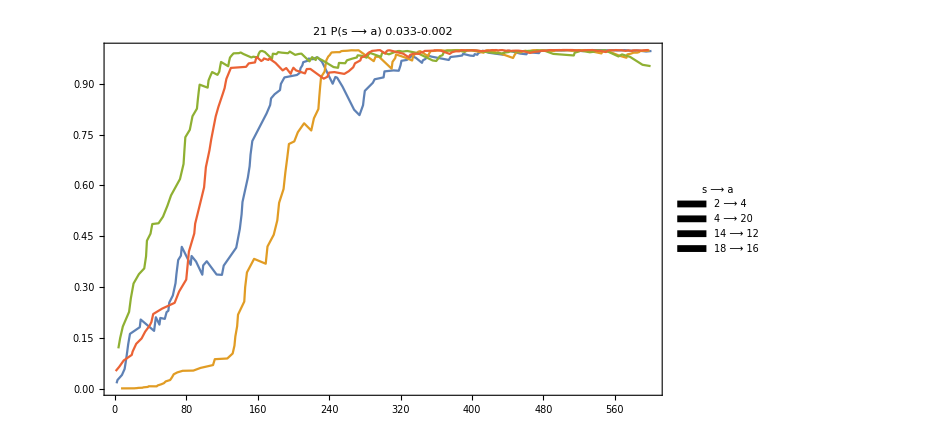

```mathematica
evolutionProbsPercept2ActionTMP=currentProbPercept2Action[[Position[possiblePairs,#]⟦1,1⟧]]&/@possiblePairs;
evolutionProbsPercept2Action=Table[If[evolutionProbsPercept2ActionTMP⟦pair,iter⟧≠0.,{iter,evolutionProbsPercept2ActionTMP⟦pair,iter⟧},Nothing],{pair,NsampledPairs},{iter,Niterations}];

ListPlot[evolutionProbsPercept2Action,
PlotRange->{0,1},
ImageSize->700,
Frame->True,
Joined->True,
BaseStyle->18,
PlotLegends->Placed[SwatchLegend[
Style[(""<>ToString[#⟦1⟧]<>" ⟶ "<>ToString[#⟦2⟧]),16]&/@possiblePairs,
LegendLabel->Style["  s ⟶ a\n",17],
LegendMarkers->Graphics[Disk[]],
LegendFunction->(Framed[#,Background->LightGray]&)],{Bottom,Right}],
FrameTicks->{Automatic,Automatic},
PlotLabel->ToString@DIM<>"          P(s ⟶ a)         "<>ToString@ϕupdateINIT<>"-"<>ToString@ϕupdateFIN
]
```

### Based on the Gram-Schmidt orthonormalization

```mathematica
(* Function to update a single matrix element Subscript[U, out,in] unitary U based on the Gram-Schmidt orthonormalization process and a given reward R. *)

variateGS[U_,in_Integer,out_Integer,R_]:= Module[{aux ={},m=Length@U ,unitary,i, j, v,index,count=0},

unitary=ConstantArray[{},m];

For[i = 1, i ≤m, i++,
count++;
v = U⟦1+Mod[out+i-1-1,m]⟧;
If[i==1,v⟦in⟧*=R];(* Here one can insert any sophisticated update rule. This is just an illustrative example. *)

If[i>1,
For[j = 1, j <= count - 1, j++,
 v = v - Conjugate[aux⟦j⟧].v*aux⟦j⟧
]
];
v=Normalize[v];
AppendTo[aux, v];
unitary⟦1+Mod[out+i-1-1,m]⟧=v
];
   
unitary
   ];
```

```mathematica
DIM=10;
originalU=HaarUnitary@DIM;
MatrixForm@originalU

updatedIN=4;
updatedOUT=2;
runMC=75;
α=1.1;

tmp=originalU;
absValues=ConstantArray[{},runMC+1];
absValues⟦1⟧=Flatten@Abs@tmp;
clementsPhases=ConstantArray[{},runMC+1];
clementsPhases⟦1⟧=unitaryDecomposition[tmp,Method->"Square"]⟦2;;⟧;

Do[
tmp=variateGS[tmp,updatedIN,updatedOUT,α];
absValues⟦run+1⟧=Flatten@Abs@tmp;
clementsPhases⟦run+1⟧=unitaryDecomposition[tmp,Method->"Square"]⟦2;;⟧
,{run,runMC}]

UnitaryMatrixQ@tmp


ArrayPlot[Abs@tmp,
PlotLegends->Automatic,
ImageSize->500
]
```

(0.283934+0.218524 ⅈ | -0.0664397+0.101715 ⅈ | -0.143318-0.198843 ⅈ | -0.136175-0.0979136 ⅈ | -0.429568-0.003602 ⅈ | 0.150891-0.173802 ⅈ | -0.186961+0.140161 ⅈ | 0.340907+0.234339 ⅈ | 0.414343+0.330071 ⅈ | 0.120546+0.101251 ⅈ
-0.312513+0.0124564 ⅈ | 0.175784-0.0320536 ⅈ | -0.6319+0.0187297 ⅈ | 0.072005+0.0300813 ⅈ | -0.31068-0.320023 ⅈ | 0.149712-0.0160322 ⅈ | 0.340007+0.0147748 ⅈ | 0.0822246-0.19751 ⅈ | -0.066892+0.051863 ⅈ | -0.2195-0.161151 ⅈ
0.0246599-0.104284 ⅈ | -0.616949+0.174164 ⅈ | -0.145827-0.212474 ⅈ | -0.0428248-0.305745 ⅈ | -0.173163+0.177828 ⅈ | -0.0129212-0.115169 ⅈ | 0.0843183+0.19425 ⅈ | -0.18393+0.0648963 ⅈ | -0.222043-0.252055 ⅈ | -0.336242+0.17893 ⅈ
0.320377+0.344094 ⅈ | 0.182103-0.211869 ⅈ | -0.0347775-0.307456 ⅈ | -0.504245+0.304231 ⅈ | -0.184878-0.0131274 ⅈ | -0.071326+0.201124 ⅈ | 0.0931407-0.0679999 ⅈ | -0.166157-0.054682 ⅈ | -0.233318-0.257492 ⅈ | -0.03716+0.11154 ⅈ
0.206493+0.0764014 ⅈ | -0.0369996-0.351426 ⅈ | -0.421586+0.121606 ⅈ | -0.0592638-0.300985 ⅈ | 0.338331-0.125863 ⅈ | -0.46657+0.00555154 ⅈ | 0.0961445+0.12295 ⅈ | -0.19872+0.290503 ⅈ | 0.141719+0.0988271 ⅈ | 0.111372-0.0387724 ⅈ
-0.25274+0.00750715 ⅈ | -0.189194-0.155518 ⅈ | -0.0674527-0.166041 ⅈ | -0.069454-0.211421 ⅈ | -0.204263+0.333609 ⅈ | -0.302789+0.372783 ⅈ | -0.148455-0.130725 ⅈ | 0.198008-0.297786 ⅈ | -0.208457+0.264049 ⅈ | 0.302792-0.197246 ⅈ
-0.0752325+0.000648793 ⅈ | 0.0468327+0.119693 ⅈ | -0.0641792-0.0123304 ⅈ | 0.082282-0.185065 ⅈ | -0.239937+0.0607914 ⅈ | 0.294146+0.0894047 ⅈ | 0.120556-0.109543 ⅈ | -0.407299+0.258834 ⅈ | 0.0866635-0.330746 ⅈ | 0.598268-0.206155 ⅈ
-0.311426-0.261571 ⅈ | 0.0348933+0.0436676 ⅈ | -0.206678+0.0568499 ⅈ | -0.259429+0.213291 ⅈ | -0.146273-0.138879 ⅈ | -0.197051-0.123732 ⅈ | -0.690647-0.0403479 ⅈ | -0.254593+0.0696155 ⅈ | 0.107057-0.122835 ⅈ | -0.0411707+0.0370632 ⅈ
0.380039-0.0413204 ⅈ | 0.0741864+0.392665 ⅈ | 0.16479+0.106077 ⅈ | 0.128396+0.0219552 ⅈ | -0.305628-0.189393 ⅈ | -0.365549-0.0464308 ⅈ | 0.0130897+0.136974 ⅈ | -0.305809-0.156885 ⅈ | -0.14499+0.23161 ⅈ | -0.0506219-0.399305 ⅈ
-0.0272919-0.333055 ⅈ | 0.06342-0.309996 ⅈ | 0.17709+0.183015 ⅈ | -0.433021-0.147403 ⅈ | -0.073506-0.0245751 ⅈ | 0.288714-0.22187 ⅈ | 0.104881+0.415763 ⅈ | -0.144111-0.145743 ⅈ | -0.198507+0.279433 ⅈ | 0.173626+0.0450358 ⅈ)

True

-Graphics-

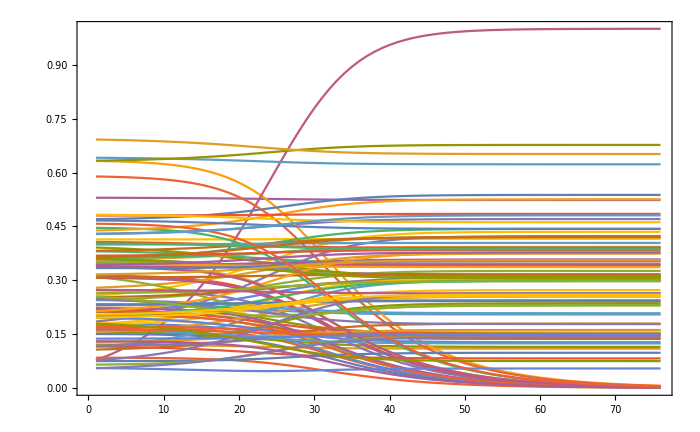

```mathematica
ListPlot[Transpose@absValues,
PlotRange->{0,1},
Joined->True,
ImageSize->700,
FrameTicksStyle->16,
Frame->True
]
```

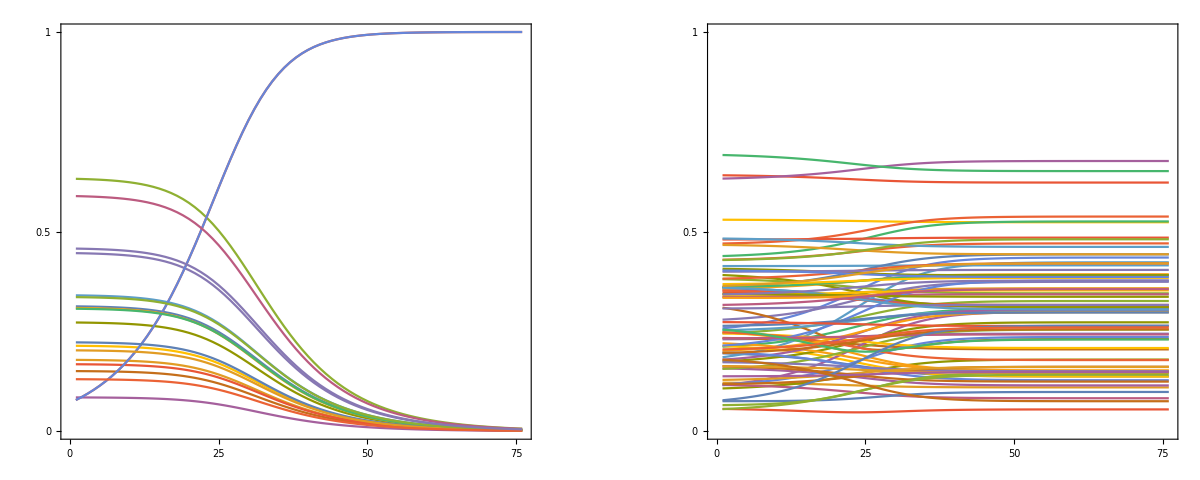

```mathematica
indicesRowColumn=Join[
Table[DIM(updatedOUT-1)+in,{in,DIM}],
Table[DIM(out-1)+updatedIN,{out,DIM}]
];

curves2plots=With[{curves=Transpose@absValues},
{curves⟦indicesRowColumn⟧,Delete[curves,{#}&/@indicesRowColumn]}
];

GraphicsRow[ListPlot[#,
PlotRange->{0,1},
Joined->True,
FrameTicksStyle->18,
Frame->True,
FrameTicks->{{{0,0.5,1},None},{{0,25,50,75},None}},
AspectRatio->0.85
]&/@curves2plots,
Spacings->100,
ImageSize->1200]
```

```mathematica
Updating multiple matrix elements at once
```

Here we test how this update mechanism performs when there are multiple rewarded (s, a) pairs.
We will suppose there are five rewarded (s,a) pairs: (1,1),(1,2),(2,1),(2,2) and one additional pair chosen by the user (updatedIN,updatedOUT), which are updated with different frequencies.

(0.292367+0.24835 ⅈ | -0.438874+0.193864 ⅈ | -0.25493-0.169318 ⅈ | 0.175979+0.186789 ⅈ | 0.0263671+0.228994 ⅈ | -0.264038-0.361378 ⅈ | 0.0516713+0.100608 ⅈ | -0.0357583+0.139029 ⅈ | 0.317552-0.0349854 ⅈ | -0.270978-0.0282583 ⅈ
-0.0260735+0.101221 ⅈ | -0.136686-0.225978 ⅈ | -0.0919183+0.0106157 ⅈ | 0.0535839-0.0366305 ⅈ | 0.287343+0.146015 ⅈ | -0.1603+0.0419812 ⅈ | -0.375607+0.43875 ⅈ | -0.201313-0.385099 ⅈ | -0.308278-0.373511 ⅈ | 0.0835825-0.10613 ⅈ
0.0553552+0.00364781 ⅈ | 0.0709783+0.0601837 ⅈ | 0.231776-0.302123 ⅈ | 0.112543-0.167334 ⅈ | -0.292678-0.0523446 ⅈ | -0.277335-0.356644 ⅈ | -0.187321+0.162587 ⅈ | 0.00157448+0.260283 ⅈ | -0.346306+0.0792794 ⅈ | 0.291771+0.411669 ⅈ
-0.282191-0.202148 ⅈ | -0.149988-0.00135906 ⅈ | -0.309731+0.319957 ⅈ | -0.0986222+0.180387 ⅈ | -0.582053-0.207764 ⅈ | -0.212408-0.137126 ⅈ | 0.129314+0.0249307 ⅈ | -0.167396-0.0142963 ⅈ | -0.0128058-0.295799 ⅈ | 0.146587-0.125873 ⅈ
0.179589+0.126108 ⅈ | -0.134462-0.432173 ⅈ | 0.223317+0.214684 ⅈ | -0.260958-0.443789 ⅈ | -0.0593876+0.195943 ⅈ | -0.075828-0.0416335 ⅈ | 0.399104+0.0291976 ⅈ | -0.0575604-0.0231598 ⅈ | 0.223597-0.218417 ⅈ | 0.0320683+0.27178 ⅈ
0.272918-0.301083 ⅈ | -0.178241-0.331939 ⅈ | 0.130609-0.0026933 ⅈ | 0.176352-0.197023 ⅈ | -0.137109-0.145542 ⅈ | -0.0556175+0.209681 ⅈ | -0.31311-0.00492904 ⅈ | 0.0942987+0.462181 ⅈ | 0.0255935-0.1079 ⅈ | -0.186921-0.388695 ⅈ
0.538474+0.0976911 ⅈ | -0.148067+0.19342 ⅈ | -0.0255271+0.019161 ⅈ | 0.222904-0.117731 ⅈ | -0.404783+0.0217268 ⅈ | 0.395771+0.0890042 ⅈ | 0.0337798-0.0298926 ⅈ | 0.100921-0.391228 ⅈ | -0.138341-0.0121435 ⅈ | 0.230242-0.100738 ⅈ
0.0120195+0.0168514 ⅈ | 0.35558+0.0911572 ⅈ | 0.319358-0.491294 ⅈ | 0.0263973+0.132528 ⅈ | -0.142199-0.0637908 ⅈ | -0.0680167+0.0573546 ⅈ | 0.362741+0.204841 ⅈ | -0.028835-0.0845704 ⅈ | 0.074419-0.424939 ⅈ | -0.168957-0.273527 ⅈ
0.336017-0.234533 ⅈ | 0.195035-0.287073 ⅈ | 0.0309724+0.238718 ⅈ | -0.0671727+0.618329 ⅈ | 0.0183086+0.170248 ⅈ | 0.105523-0.104831 ⅈ | 0.0985333+0.302756 ⅈ | 0.249509+0.0940668 ⅈ | -0.11668+0.042052 ⅈ | 0.000332582+0.165974 ⅈ
0.191447+0.0237331 ⅈ | 0.0221303-0.0840897 ⅈ | 0.18377+0.0731844 ⅈ | -0.20323+0.0455746 ⅈ | -0.125896-0.238631 ⅈ | -0.503627-0.0377044 ⅈ | -0.0795585-0.182443 ⅈ | 0.104699-0.463619 ⅈ | -0.14322+0.313411 ⅈ | -0.396828-0.0559464 ⅈ)

True

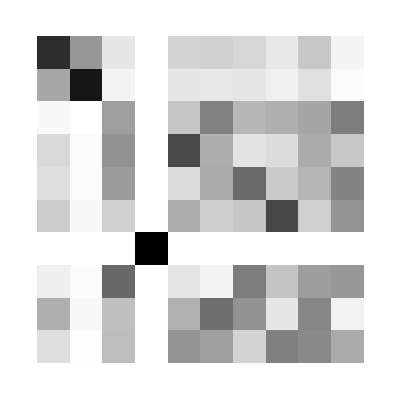

```mathematica
DIM=10;
originalU=HaarUnitary@DIM;
MatrixForm@originalU

updatedIN=4;
updatedOUT=7;
runMC=500;
α=1.1;

tmp=originalU;
absValues=ConstantArray[{},runMC+1];
absValues⟦1⟧=Flatten@Abs@tmp;

Do[
If[RandomChoice[{0.3,0.7}->{True,False}],
tmp=variateGS[tmp,RandomChoice[{0.5,0.5}->{1,2}],RandomChoice[{0.5,0.5}->{1,2}],α],
tmp=variateGS[tmp,updatedIN,updatedOUT,α]
];
absValues⟦run+1⟧=Flatten@Abs@tmp;
,{run,runMC}]

UnitaryMatrixQ@tmp

ArrayPlot[Abs@tmp]
```

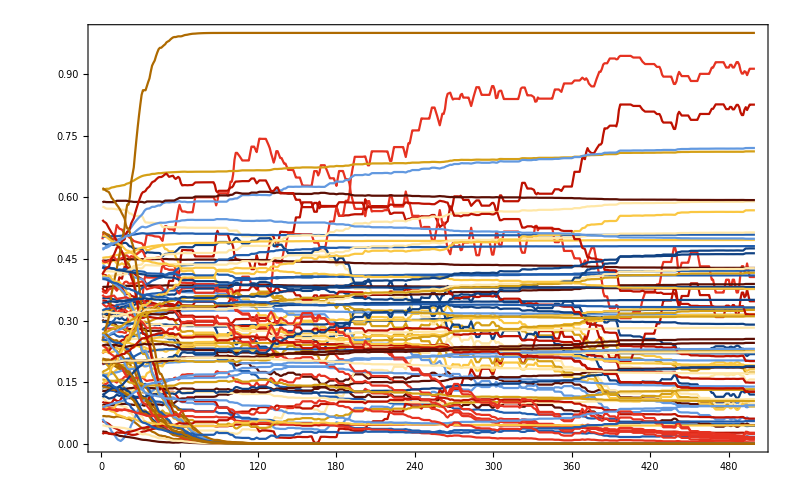

```mathematica
ListPlot[MovingAverage[#,2]&/@Transpose@absValues,
PlotRange->{0,1},
Joined->True,
PlotStyle->Flatten@Table[Directive[#,Thickness[0.002]]&/@ColorData[20,"ColorList"]⟦;;DIM⟧,{i,DIM}],
ImageSize->800,
FrameTicksStyle->18,
Frame->True
]
```

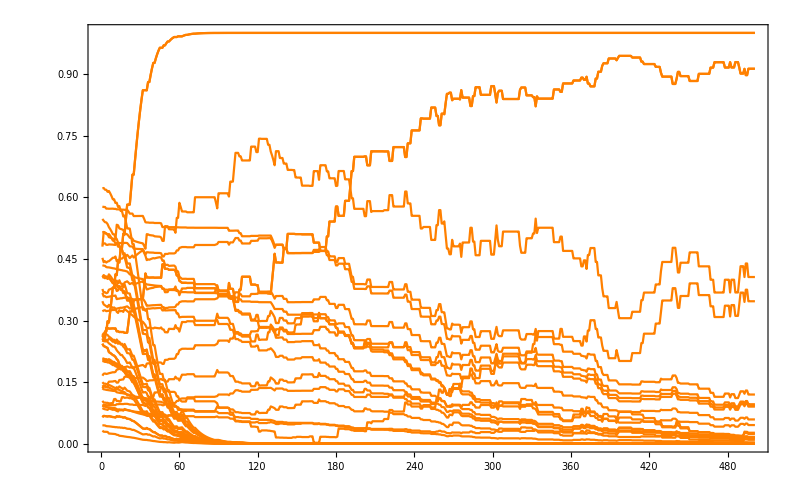

```mathematica
absElementsEvolution=Transpose@absValues;

ListPlot[Join[
Table[Abs@absElementsEvolution[[DIM(updatedOUT-1)+in]],{in,DIM}],
Table[Abs@absElementsEvolution[[DIM(2-1)+in]],{in,DIM}],
Table[Abs@absElementsEvolution[[DIM(out-1)+updatedIN]],{out,DIM}],
Table[Abs@absElementsEvolution[[DIM(out-1)+2]],{out,DIM}]
],
PlotRange->{0,1},
Joined->True,
PlotStyle->Directive[Orange,Thickness[0.002]],
ImageSize->800,
FrameTicksStyle->18,
Frame->True
]
```

## Figures

### Fig. 4 (Causal Diamond)

#### Panel A

This snippet serves to generate the dataset allLeakingNodesSquareDIMS, which contains all leaking nodes for square architectures. It is not necessary to run this snippet again.

```mathematica
(*
minDIM=1;
maxDIM=16;
allLeakingNodesSquareDIMS=ConstantArray[{},{1+maxDIM-minDIM}];
DIMindex=0;

Do[
DIMindex++;
graphINFO=getGraph[DIM,Method->"Square"];
directedGraph=DeleteDuplicates@graphINFO⟦1⟧;
nVertices=VertexCount@directedGraph;
allLeakingNodesSquareDIMS⟦DIMindex⟧=Table[findLeakingNodes[DIM,graphINFO,inMode,nVertices-DIM+outMode],{inMode,DIM},{outMode,DIM}];
,{DIM,minDIM,maxDIM}
];

Put[allLeakingNodesSquareDIMS,myPATHexport<>"allLeakingNodesSquareDIMS.txt"]
*)
```

```mathematica
allLeakingNodesSquareDIMS=Get[myPATHimport<>"allLeakingNodesSquareDIMS.txt"];
```

```mathematica
DIM=12;
allLeakingNodes=allLeakingNodesSquareDIMS⟦DIM⟧;

graphINFO=getGraph[DIM,Method->"Square"];
directedGraph=DeleteDuplicates@graphINFO⟦1⟧;
nVertices=VertexCount@directedGraph;
```

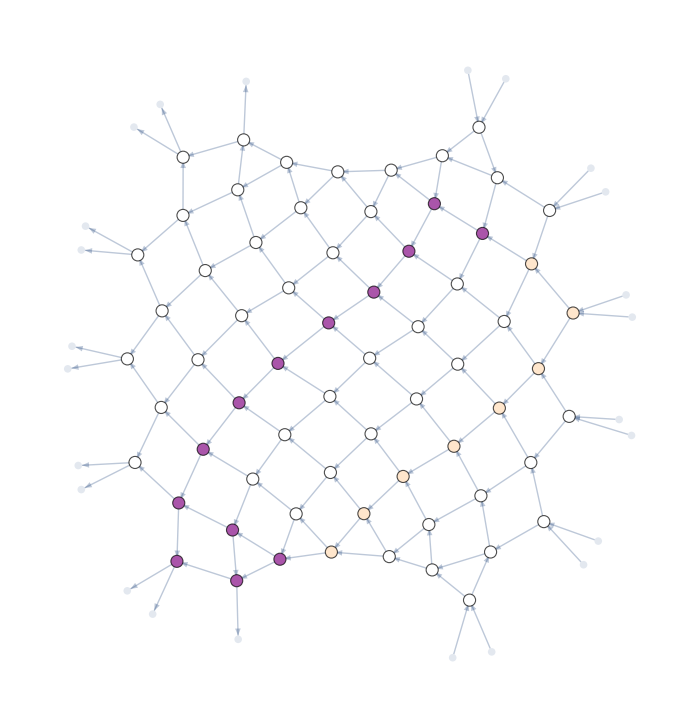
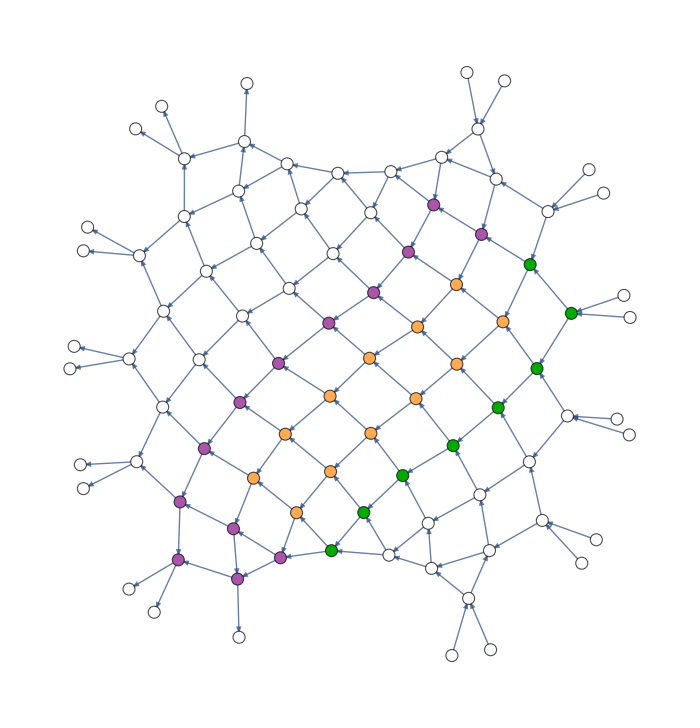

```mathematica
inMode=6;
outMode=11;

{lightCone,leakingNodes}=allLeakingNodes⟦inMode,outMode⟧;

highlightedNodes=Join[
Style[#,White]&/@Range[DIM+1,nVertices-DIM],
Style[#,Lighter@Orange]&/@Complement[Intersection[VertexOutComponent[directedGraph,{inMode}],VertexInComponent[directedGraph,{nVertices-DIM+outMode}]],lightCone],
Style[#,Darker@Green]&/@Complement[lightCone,leakingNodes],
Style[#,Lighter@Purple]&/@leakingNodes,
Style[#,White]&/@Range@DIM,
Style[#,White]&/@Range[nVertices-DIM+1,nVertices]
];

plot1=HighlightGraph[directedGraph,
Join[
Style[#,White]&/@Range[DIM+1,nVertices-DIM],
Style[#,LightOrange]&/@Complement[lightCone,leakingNodes],
Style[#,Lighter@Purple]&/@leakingNodes
],
VertexSize->0.6,
GraphLayout->"SpringEmbedding",
GraphHighlight->lightCone,
GraphHighlightStyle->"DehighlightFade",
ImageSize->700
];

plot2=HighlightGraph[directedGraph,
highlightedNodes,
GraphLayout->"SpringEmbedding",
VertexSize->0.6,
ImageSize->700
];

{plot1,plot2}
```

```mathematica
Export[myPATHexport<>"Panel4a.pdf",plot1];
```

#### Panels B-C

```mathematica
DIM=12;

graphINFO=getGraph[DIM,Method->"Square2PS"];(* We consider the case where beamsplitters are implemented as Mach-Zehnder interferometers. *)
directedGraph=DeleteDuplicates@graphINFO⟦1⟧;
nVertices=VertexCount@directedGraph;

allLeakingNodes=allLeakingNodesDIMS⟦DIM⟧;

cellPositions=graphINFO⟦2,2;;-2⟧;

cellsUpara=Table[Join[#⟦s,k⟧,{1,Subscript[P, s,k,graphINFO⟦3,s+1,k⟧]}
],{s, Length@#},{k,Length[#⟦s⟧]}]&@cellPositions;

layersPara=Table[Normal@chipLayer[DIM,cellsUpara,layer],{layer,Length@cellPositions}];

phaseSettingsInitialization=Map[(#->RandomReal[{0,2π}])&,Table[
Subscript[P, s,k,graphINFO⟦3,s+1,k⟧] ,{s,Length@cellPositions},{k,Length[cellPositions⟦s⟧]}],{2}
];
```

```mathematica
Niterations=500;

phaseSettings=phaseSettingsInitialization;

nodesLayer=graphINFO⟦3,2;;-2⟧;
posNodesInLayers=Table[Association[(nodesLayer[[l,#]]->#)&/@Range@Length@cellPositions⟦l⟧],{l,Length@cellPositions}];

fromNodetoLayer=Association@Flatten@Table[nodesLayer[[l,i]]->l,{l,Length@nodesLayer},{i,Length@nodesLayer[[l]]}];
updateCausalDiamondSequence=Table[
Sort[Join[(<|(#-> {x})&/@Range[Min@#,Max@#]&@Keys@#|>),#]&@GroupBy[allLeakingNodes⟦inMode,outMode,2⟧,fromNodetoLayer],#1>#2&]
,{inMode,DIM},{outMode,DIM}];
updateCDstartingLayer=Map[Min@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDfinalLayer=Map[Max@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDnodesLayerwise=Map[Values,updateCausalDiamondSequence,{2}];


ϕupdateINIT=0.03;(* The size of the update decreases with time. *)
ϕupdateFIN=0.002;
ϕupdate=ϕupdateINIT;
ϕstep=(ϕupdateINIT-ϕupdateFIN)/Niterations;
ϕupdate-=ϕstep;

NsampledPairs=Floor@(DIM/3);
inModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
outModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
possiblePairs=Sort[{inModes⟦#⟧,outModes⟦#⟧}&/@Range@NsampledPairs]

currentProbPercept2Action=ConstantArray[0.,{NsampledPairs,Niterations}];



Do[

{s,a}=RandomChoice[possiblePairs];
indexNextPair=Position[possiblePairs,{s,a}]⟦1,1⟧;

If[updateCDstartingLayer⟦s,a⟧≠1,
layersFixed=Dot@@Reverse@Table[layersPara⟦layer⟧/.phaseSettings⟦layer⟧,{layer,updateCDstartingLayer⟦s,a⟧-1}];,
layersFixed=IdentityMatrix@DIM
];
layersVariable=layersPara⟦updateCDstartingLayer⟦s,a⟧;;⟧;

updateResult=updateCausalDiamond[layersFixed,layersVariable,
updateCausalDiamondSequence⟦s,a⟧,updateCDstartingLayer⟦s,a⟧, updateCDfinalLayer⟦s,a⟧,
posNodesInLayers,phaseSettings,ϕupdate,{s,a}];

phaseSettings=updateResult⟦1⟧;
u=updateResult⟦2⟧;
currentProbPercept2Action⟦indexNextPair,iter⟧=abs2@u⟦a,s⟧;
,

{iter,Niterations}
];
```

{{2,8},{4,4},{10,6},{12,2}}

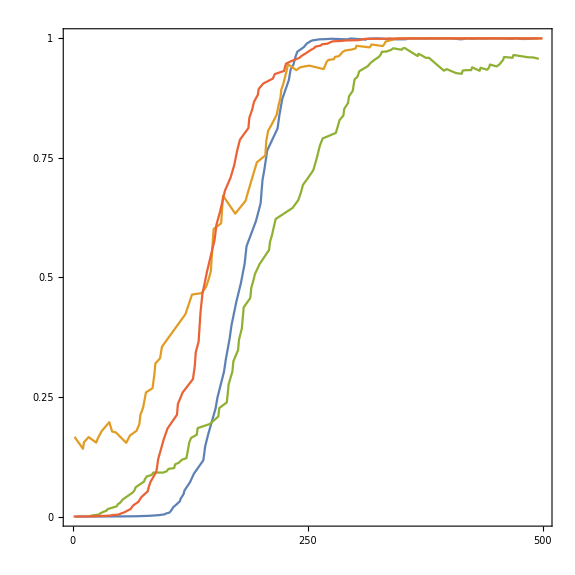

```mathematica
evolutionProbsPercept2ActionTMP=currentProbPercept2Action⟦Position[possiblePairs,#]⟦1,1⟧⟧&/@possiblePairs;
evolutionProbsPercept2Action=Table[If[evolutionProbsPercept2ActionTMP⟦pair,iter⟧≠0.,{iter,evolutionProbsPercept2ActionTMP⟦pair,iter⟧},Nothing],{pair,NsampledPairs},{iter,Niterations}];

panelC=ListPlot[evolutionProbsPercept2Action,
PlotRange->{{0,500},{0,1}},
ImageSize->575,
Frame->True,
Joined->True,
BaseStyle->26,
AspectRatio->1,
FrameTicks->{{{0,0.25,0.5,0.75,1},None},{{0,250,500,1000},None}}
]
```

```mathematica
evolutionProbsPercept2Action
```

{{{3,0.0000135735},{4,0.0000189138},{7,0.0000256566},{9,0.0000357104},{10,0.0000506462},{13,0.0000585978},{16,0.0000793479},{20,0.000088714},{22,0.000116272},{26,0.000121057},{33,0.000103059},{34,0.00015189},{38,0.000263771},{44,0.00024768},{45,0.000351589},{54,0.00037118},{56,0.000479989},{60,0.000483795},{69,0.000691911},{74,0.00108957},{82,0.00157767},{92,0.00302563},{98,0.00470646},{99,0.00611938},{103,0.00835721},{104,0.0105258},{105,0.0130962},{106,0.0161189},{107,0.0196427},{110,0.0245589},{114,0.0318837},{115,0.0376859},{118,0.0469467},{119,0.0545611},{125,0.0723687},{129,0.0895436},{139,0.117615},{140,0.131675},{141,0.146715},{144,0.170513},{152,0.225503},{154,0.248295},{161,0.302713},{163,0.329104},{167,0.371825},{169,0.399996},{174,0.447781},{179,0.48809},{183,0.528724},{185,0.565212},{195,0.61769},{200,0.655065},{201,0.680061},{202,0.703941},{204,0.725778},{207,0.765429},{218,0.811501},{220,0.839784},{223,0.87316},{230,0.912567},{231,0.924536},{232,0.935313},{235,0.945584},{236,0.95383},{237,0.960758},{239,0.971928},{246,0.981644},{249,0.988812},{253,0.993771},{255,0.995619},{260,0.997019},{262,0.997801},{268,0.998213},{274,0.998895},{276,0.999069},{292,0.997829},{295,0.999165},{296,0.999613},{312,0.997236},{313,0.998559},{315,0.999386},{320,0.999673},{322,0.999796},{323,0.999805},{324,0.999812},{325,0.999817},{335,0.998458},{336,0.999394},{345,0.997809},{355,0.998055},{356,0.999353},{358,0.999758},{359,0.999765},{363,0.999765},{366,0.99976},{377,0.999355},{380,0.999759},{389,0.999697},{391,0.99976},{392,0.999767},{400,0.99976},{403,0.999761},{413,0.997965},{417,0.9988},{418,0.99969},{426,0.999166},{429,0.999187},{430,0.999693},{437,0.999187},{440,0.999195},{442,0.999697},{445,0.999759},{448,0.999759},{450,0.999766},{455,0.999753},{467,0.998856},{470,0.999702},{471,0.999763},{472,0.999771},{478,0.998574},{486,0.998857},{489,0.999395},{493,0.999776},{494,0.999783},{495,0.999784}},{{2,0.166613},{11,0.141711},{12,0.155392},{17,0.166206},{25,0.154675},{27,0.1646},{31,0.178888},{39,0.197403},{42,0.177792},{46,0.17589},{57,0.154239},{61,0.169573},{68,0.179298},{71,0.193503},{72,0.212334},{75,0.227992},{78,0.259673},{85,0.268288},{87,0.298088},{88,0.320026},{93,0.330996},{95,0.355052},{120,0.423243},{127,0.464253},{137,0.467084},{142,0.480583},{145,0.498155},{147,0.51268},{148,0.54335},{149,0.573047},{150,0.601479},{158,0.613096},{159,0.642438},{160,0.670874},{173,0.633367},{184,0.660338},{186,0.674766},{196,0.740752},{205,0.755149},{206,0.785186},{208,0.806806},{211,0.817104},{217,0.839681},{219,0.85909},{221,0.875169},{222,0.892648},{224,0.903962},{228,0.934767},{229,0.945779},{238,0.933494},{242,0.939318},{247,0.941364},{252,0.942838},{267,0.935638},{269,0.94445},{270,0.950176},{272,0.95462},{278,0.956518},{279,0.961067},{281,0.96186},{283,0.962461},{285,0.966245},{287,0.971195},{290,0.974551},{297,0.976583},{301,0.978792},{302,0.984321},{316,0.981044},{318,0.987127},{330,0.983779},{332,0.989119},{333,0.993296},{342,0.997738},{343,0.999049},{344,0.999508},{348,0.999786},{354,0.999786},{357,0.999814},{360,0.999859},{361,0.999908},{362,0.999929},{364,0.999916},{370,0.999857},{371,0.99988},{372,0.99988},{374,0.999892},{375,0.999908},{378,0.999868},{382,0.999803},{383,0.999832},{384,0.999876},{385,0.999888},{386,0.999888},{388,0.999896},{390,0.999871},{393,0.999853},{394,0.999871},{396,0.999899},{399,0.999906},{401,0.999925},{404,0.999934},{406,0.999935},{409,0.999846},{412,0.999862},{420,0.999799},{422,0.999865},{428,0.99982},{431,0.999879},{435,0.999849},{439,0.999778},{447,0.999871},{449,0.999854},{453,0.999829},{457,0.999808},{461,0.999878},{464,0.999753},{465,0.999841},{474,0.999767},{476,0.999755},{477,0.999767},{487,0.999774},{488,0.999826},{491,0.999812},{492,0.999834},{499,0.999639}},{{19,0.00137724},{21,0.00244371},{28,0.00416227},{29,0.00615715},{32,0.00933843},{36,0.0121569},{37,0.0154486},{47,0.0215002},{48,0.0254798},{51,0.0297886},{53,0.0352109},{59,0.0435116},{64,0.0504072},{66,0.0556268},{67,0.0611835},{76,0.0731926},{77,0.0786913},{79,0.0840472},{84,0.086932},{86,0.092141},{96,0.0918721},{100,0.0946928},{102,0.0996492},{108,0.101398},{109,0.109213},{113,0.112571},{116,0.118501},{121,0.122047},{122,0.132064},{123,0.142849},{124,0.154416},{126,0.164463},{132,0.170991},{133,0.18497},{146,0.193532},{155,0.209306},{156,0.226919},{164,0.23861},{165,0.257312},{166,0.276803},{170,0.303609},{171,0.324659},{176,0.348197},{177,0.369991},{180,0.393329},{181,0.415462},{182,0.437434},{189,0.456993},{190,0.477945},{192,0.491632},{194,0.507354},{199,0.528287},{209,0.55756},{210,0.57487},{212,0.587793},{214,0.605228},{216,0.622102},{234,0.645398},{240,0.661525},{243,0.678382},{245,0.693466},{250,0.706999},{256,0.724094},{259,0.74407},{261,0.759692},{263,0.775371},{266,0.790653},{280,0.802064},{282,0.815291},{284,0.829146},{288,0.838401},{289,0.852722},{293,0.864677},{294,0.878467},{298,0.890123},{299,0.90275},{300,0.914361},{303,0.91952},{305,0.931214},{314,0.941793},{317,0.948645},{321,0.95481},{326,0.961474},{328,0.966825},{329,0.971914},{334,0.972401},{339,0.975987},{341,0.979265},{350,0.976035},{351,0.978461},{353,0.980055},{367,0.962846},{368,0.967821},{376,0.959056},{379,0.95938},{395,0.932281},{398,0.935581},{408,0.927159},{414,0.925883},{415,0.932619},{419,0.933454},{424,0.933435},{425,0.939407},{433,0.932091},{434,0.938467},{441,0.934254},{443,0.938788},{444,0.945207},{451,0.941174},{454,0.945328},{456,0.950193},{458,0.954777},{459,0.96099},{468,0.959256},{469,0.965106},{485,0.960273},{490,0.960016},{496,0.95705}},{{1,0.0000419424},{5,0.0000686376},{6,0.000106804},{8,0.000171207},{14,0.000234832},{15,0.000347083},{18,0.000471012},{23,0.000723995},{24,0.00101828},{30,0.00119649},{35,0.00157927},{40,0.00199422},{41,0.00267755},{43,0.00323059},{49,0.00405903},{50,0.00528927},{52,0.00680449},{55,0.00883689},{58,0.0120621},{62,0.0161278},{63,0.0198094},{65,0.0240847},{70,0.0309707},{73,0.0404182},{80,0.053174},{81,0.062157},{83,0.0731128},{89,0.0935557},{90,0.106345},{91,0.120233},{94,0.141018},{97,0.162173},{101,0.1844},{111,0.212913},{112,0.235507},{117,0.259331},{128,0.287489},{130,0.315567},{131,0.343683},{134,0.365778},{135,0.395689},{136,0.426384},{138,0.464359},{143,0.512664},{151,0.578352},{153,0.6104},{157,0.63869},{162,0.681313},{168,0.70851},{172,0.735466},{175,0.764944},{178,0.788013},{187,0.812425},{188,0.833853},{191,0.85102},{193,0.867289},{197,0.881648},{198,0.89441},{203,0.905706},{213,0.915733},{215,0.925184},{225,0.931831},{226,0.940486},{227,0.947018},{233,0.952722},{241,0.958818},{244,0.963763},{248,0.968528},{251,0.972545},{254,0.976337},{257,0.979522},{258,0.982472},{264,0.984864},{265,0.987381},{271,0.988725},{273,0.990685},{275,0.992427},{277,0.993731},{286,0.994553},{291,0.995616},{304,0.996103},{306,0.99683},{307,0.997328},{308,0.997812},{309,0.998157},{310,0.998535},{311,0.99877},{319,0.998894},{327,0.999029},{331,0.999123},{337,0.99922},{338,0.999311},{340,0.999389},{346,0.999427},{347,0.999527},{349,0.999556},{352,0.999644},{365,0.999657},{369,0.999726},{373,0.999756},{381,0.999788},{387,0.99979},{397,0.999807},{402,0.999811},{405,0.999866},{407,0.999852},{410,0.999877},{411,0.999877},{416,0.99985},{421,0.999888},{423,0.999866},{427,0.999904},{432,0.999871},{436,0.999884},{438,0.999917},{446,0.999862},{452,0.999825},{460,0.999816},{462,0.999854},{463,0.999865},{466,0.999865},{473,0.999855},{475,0.999865},{479,0.999817},{480,0.99982},{481,0.99982},{482,0.99982},{483,0.99982},{484,0.99982},{497,0.999831},{498,0.999858},{500,0.99982}}}

```mathematica
Export[myPATHexport<>"Panel4c.pdf",panelC];
```

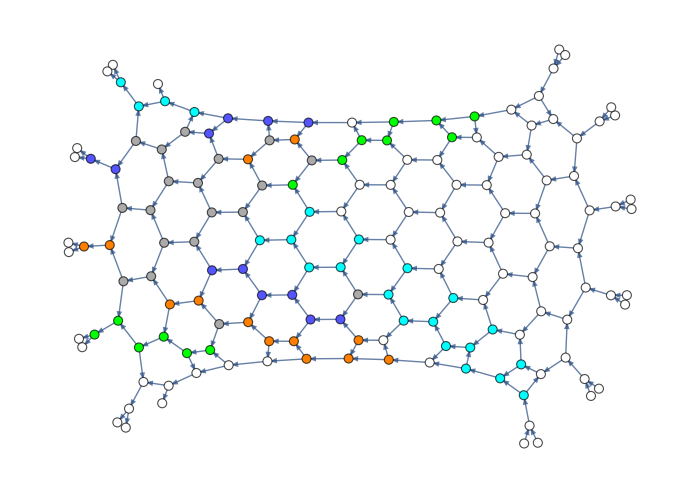

```mathematica
colors={Green,Lighter@Blue,Orange,Cyan,Red,Pink,Yellow,Magenta,Brown};

allLeakingNodesAllPairs=allLeakingNodes⟦possiblePairs⟦#,1⟧,possiblePairs⟦#,2⟧,2⟧&/@Range@NsampledPairs;

highlightedNodes=Flatten@Table[Style[allLeakingNodesAllPairs⟦pathN,node⟧,colors⟦pathN⟧,Thick],{pathN,Length@allLeakingNodesAllPairs},{node,Length@allLeakingNodesAllPairs⟦pathN⟧}];

overlappingNodes=First/@Cases[Tally[Flatten@allLeakingNodesAllPairs],u_/;u[[2]]≥2];
highlightedOverlappingNodes=Flatten@Table[Style[node,Lighter@Gray],{node,overlappingNodes}];

otherNodes=Style[#,White]&/@Complement[VertexList@directedGraph,DeleteDuplicates@Flatten@allLeakingNodesAllPairs];

panelB=HighlightGraph[Graph@directedGraph,
Join[highlightedNodes,highlightedOverlappingNodes,otherNodes],
ImageSize->700,
VertexSize->1.1,
AspectRatio->0.7
]
```

```mathematica
Export[myPATHexport<>"Panel4b.pdf",panelB];
```

### Fig. 7 (Quantum ECM)

```mathematica
(*graphINFO=getGraph[DIM=10,Method->"Random"];
dag=Sort@DeleteDuplicates[graphINFO⟦1⟧];*)
ECMfig2={1->4,2->4,1->3,2->5,3->6,4-> 5,4->6,1->7,4->7,5->7,3->8,6->8,5->9,6->9,7-> 9,7->8};

infoQECM=initializeQuantumECM[ECMfig2];

qECM=infoQECM["graphECM"];
fromStoECMsubgraph=infoQECM["fromStoECMsubgraph"];
percepts=infoQECM["percepts"];
actions=infoQECM["actions"];
fromStoActions=infoQECM["fromStoActions"];
verticesQECM=VertexCount@qECM;


fromVtoINOUTvertices=Association[(#->Sort@VertexComponent[UndirectedGraph@qECM,#,{1}]&)/@(Range@verticesQECM)];

fromVtoUnitary=Association[#->HaarUnitary[Length@fromVtoINOUTvertices[#]]&/@Range@verticesQECM];
(fromVtoUnitary[#]=IdentityMatrix[Length@fromVtoUnitary[#]])&/@infoQECM["actions"];

(*layeredVertices=findCausalPartition[graphECM,percepts,actions];*)
layeredVertices=findCausalPartition[qECM,percepts,actions];

infoPercepts=Association@Table[s->infoPercept[s,fromStoECMsubgraph,qECM,fromVtoUnitary],{s,percepts}];
```

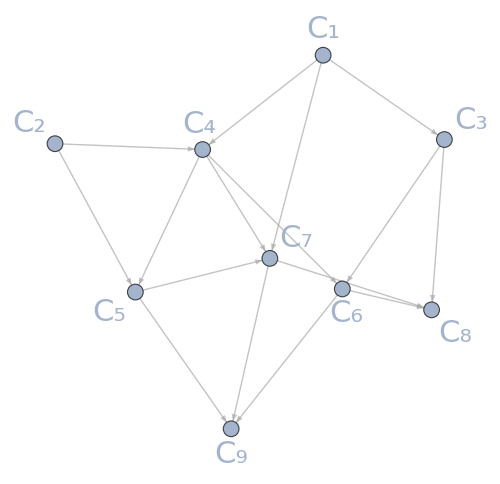

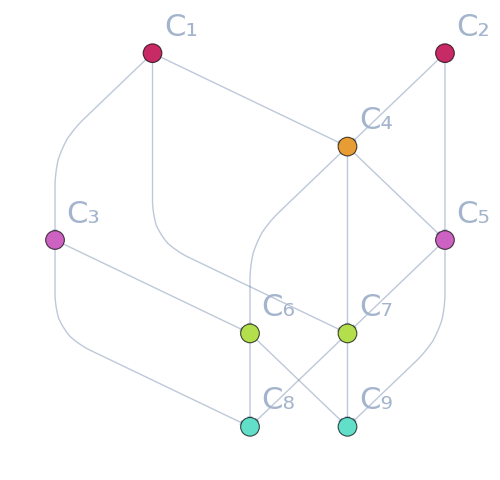

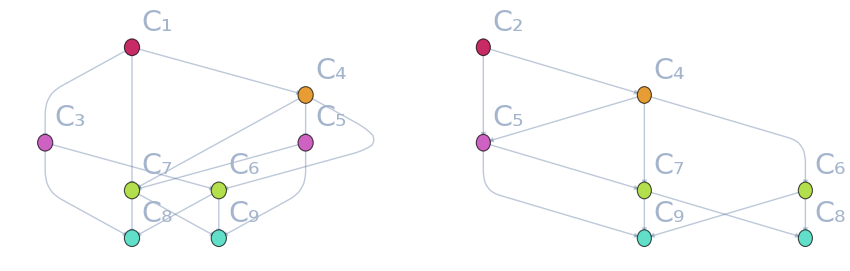

```mathematica
palette=Flatten@ConstantArray[ColorData[54,"ColorList"],5];

imageSizeFixed=500;
aspectRatio=0.8;
fontSize=22;


panelA=Framed[Graph[qECM,
ImageSize->imageSizeFixed,
VertexLabels->Table[i->Style[Subscript[C, i],1.4fontSize],{i,VertexCount@qECM}],
VertexSize->0.20,EdgeStyle->Lighter@Gray,
AspectRatio->1.2aspectRatio,
GraphLayout->"SpringElectricalEmbedding"
],
Alignment->Center,FrameStyle->GrayLevel[.7],RoundingRadius->6]



(*panelB=Framed[HighlightGraph[qECM,
Join[
Table[Style[node,Black],{node,VertexCount@qECM}],
Table[Style[node,Green],{node,percepts}],
Table[Style[node,Red],{node,actions}]
],
GraphHighlightStyle->"DehighlightFade",
VertexLabels->Table[i->Style[Subscript[C, i],1.4fontSize],{i,VertexCount@qECM}],
VertexSize->0.22,
ImageSize->imageSizeFixed,
AspectRatio->1.3aspectRatio
],
FrameStyle->GrayLevel[.7],RoundingRadius->8]*)



panelB=Framed[HighlightGraph[qECM,
Table[Style[#,ColorData[54,"ColorList"]⟦l⟧]&/@layeredVertices⟦l⟧,{l,Length@layeredVertices}],
VertexLabels->Table[i->Style[Subscript[C, i],1.4fontSize],{i,VertexCount@qECM}],
VertexSize->0.20,
GraphHighlightStyle->"DehighlightFade",
ImageSize->imageSizeFixed,
AspectRatio->1.2aspectRatio
],
FrameStyle->GrayLevel[.7],RoundingRadius->6]



panelsCD=Framed[GraphicsRow[
Table[
With[{layeredVerticesFromPerceptU=layeredVertices,g=fromStoECMsubgraph[perceptU]},
HighlightGraph[g,
Table[Style[#,ColorData[54,"ColorList"]⟦l⟧]&/@layeredVerticesFromPerceptU⟦l⟧,{l,Length@layeredVerticesFromPerceptU}],
VertexLabels->Table[i->Style[Subscript[C, i],1.3fontSize],{i,VertexCount@qECM}],
VertexSize->0.35,
GraphHighlightStyle->"DehighlightFade",
AspectRatio->0.5
]
],
{perceptU,percepts}
],
ImageSize->850
],
FrameStyle->GrayLevel[.7],
RoundingRadius->6
]



Export[myPATHexport<>"panelsA.pdf",panelA];
Export[myPATHexport<>"panelsB.pdf",panelB];
Export[myPATHexport<>"panelsCD.pdf",panelsCD];
```

### Fig. 8 (Causal Diamond / Gram-Schmidt)

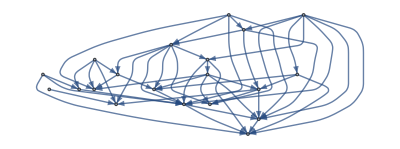

```mathematica
(*graphINFO=getGraph[DIM=10,Method->"Random"];
dag=Sort@DeleteDuplicates[graphINFO⟦1⟧];*)
(*ECMfig2={1->4,2->4,1->3,2->5,3->6,4-> 5,4->6,1->7,4->7,5->7,3->8,6->8,5->9,6->9,7-> 9,7->8};*)
dag=getDAG[vertexCount=20,edgeCountTMP=50]

infoQECM=initializeQuantumECM[dag(*ECMfig2*)];

qECM=infoQECM["graphECM"];
fromStoECMsubgraph=infoQECM["fromStoECMsubgraph"];
percepts=infoQECM["percepts"];
actions=infoQECM["actions"];
fromStoActions=infoQECM["fromStoActions"];
verticesQECM=VertexCount@qECM;


fromVtoINOUTvertices=Association[(#->Sort@VertexInComponent[qECM,#,1]&)/@(Range@verticesQECM)];(* For each vertex V, the list of vertices before and after V. *)
fromVtoUnitary=Association[#->HaarUnitary[Length@fromVtoINOUTvertices[#]]&/@Range@verticesQECM];(* For each vertex V, a Haar-random unitary with size given by the local connectivity. *)

(*layeredVertices=findCausalPartition[graphECM,percepts,actions];*)
layeredVertices=findCausalPartition[qECM,percepts,actions];

infoPercepts=Association@Table[s->infoPercept[s,fromStoECMsubgraph,qECM,fromVtoUnitary],{s,percepts}];
```

20

1

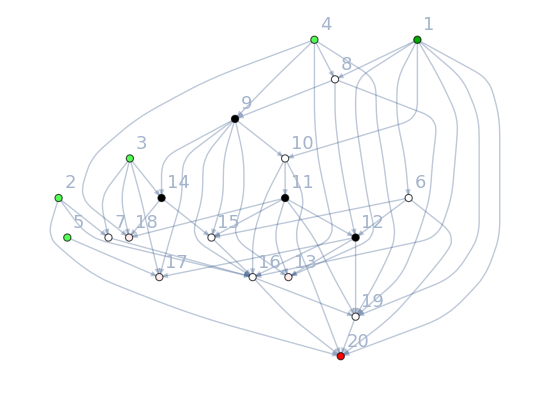

```mathematica
leakingNodesQECM=Association@Flatten@ParallelTable[{s,a}->findLeakingNodesAnyDAG[qECM,s,a]⟦3⟧,{s,infoQECM["percepts"]},{a,infoQECM["actions"]}];

a=20(*RandomChoice@infoQECM["actions"]*)
s=1(*RandomChoice@infoQECM["percepts"]*)


panelA=HighlightGraph[qECM,Join[
Table[Style[node,White],{node,VertexCount@qECM}],
Table[Style[node,Black],{node,leakingNodesQECM[{s,a}]}],
Table[Style[node,Lighter@Green],{node,infoQECM["percepts"]}],
Table[Style[node,LightPink],{node,infoQECM["actions"]}],
{Style[a,Red]},
{Style[s,Darker@Green]}
],
GraphHighlightStyle-> "DehighlightFade",
VertexLabels->Table[i->Style[i,18],{i,verticesQECM}],
VertexSize->0.35,ImageSize->550,
AspectRatio->0.7
]
```

```mathematica
Export[myPATHexport<>"panelA.pdf",panelA];
```

```mathematica
infoQECM["percepts"]
infoQECM["fromStoActions"]

{s,a}=Last@SortBy[
Flatten[Table[{s,a},{s,infoQECM["percepts"]},{a,infoQECM["fromStoActions"][s]}],1],
VertexCount@Subgraph[qECM,FindShortestPath[qECM,#⟦1⟧,#⟦2⟧]]&
] (* Select the (s,a) pair that has the LONGEST SHORTEST path. This pair will be used in the next analysis. *)
```

{1,2,3,4,5}

<|1→{13,17,18,20},2→{20},3→{17,18,20},4→{13,17,18,20},5→{17}|>

{3,20}

```mathematica
optimizedPath=Subgraph[qECM,FindShortestPath[qECM,s,a]] (* This is the path in the ECM that will be optimized via Gram-Schmidt. *)
UtoOptimize=Drop[VertexList@optimizedPath,1]

inOutModesToOptimize=Partition[VertexList@optimizedPath,2,1] (* Retrieve the clips to be optimized from the edge labels. *)
fromVtoInOutModesToOptimize=Association@Thread[UtoOptimize->inOutModesToOptimize](* These are the in/out modes of huge qECM unitary that, at each step in the qECM, will be optimized via a Gram-Schmidt process. <| vertex -> (in,out), ... |> *)

inMode=s;
outMode=a;

indicesToOptimize=Association@Table[
v->(Position[fromVtoINOUTvertices[v],#]⟦1,1⟧&/@fromVtoInOutModesToOptimize[v]),
{v,Keys@fromVtoInOutModesToOptimize}
](* These are the in/out modes of each unitary that, at each step in the qECM, will be optimized via a Gram-Schmidt process. <| vertex -> (in,out), ... |> *)

orderedVerticesFromS=Select[Flatten@layeredVertices,MemberQ[infoPercepts[s]["vertices"],#]&]

SplitBy[orderedVerticesFromS,MemberQ[UtoOptimize,#]&]
```

-Graphics-

{7,16,20}

{{3,7},{7,16},{16,20}}

<|7→{3,7},16→{7,16},20→{16,20}|>

<|7→{2,3},16→{4,8},20→{5,7}|>

{3,14,7,15,16,19,17,18,20}

{{3,14},{7},{15},{16},{19,17,18},{20}}

```mathematica
nOptSteps=100;
rewardValues={1.1,1.2,1.3};
prob=ConstantArray[0,{Length@rewardValues,nOptSteps}];

monitoredSteps={2,nOptSteps};
savedConfig4Trace=ConstantArray[0,2];
savedConfigCont=0;

(*MatrixForm[Chop[abs2@infoPercepts[s]["unitaries"][#],10^-4]]&/@FindShortestPath[qECM,s,a]*)



Do[
initUlist=infoPercepts[s]["unitaries"];

Do[

If[MemberQ[monitoredSteps,step]&&nReward==Length@rewardValues,
savedConfigCont++;
savedConfig4Trace⟦savedConfigCont⟧=initUlist
];

Do[
If[MemberQ[UtoOptimize,v],
initUlist[v]=variateGS[initUlist[v],indicesToOptimize[v]⟦1⟧,indicesToOptimize[v]⟦2⟧,rewardValues⟦nReward⟧],(* Unitaries are updated via a Gram-Schmidt process. *)
Do[initUlist[v]=variateGS[initUlist[v],i,i,rewardValues⟦nReward⟧],{i,Length@initUlist[v]}](* Unitaries are updated via a Gram-Schmidt process. *)
]
,{v,orderedVerticesFromS}];

allLayers=Reverse@ParallelTable[
getUstep[infoQECM["nModes"],fromVtoINOUTvertices[v],initUlist[v]],{v,orderedVerticesFromS}]; (* Embeds each unitary into a larger transformation whose size is given by the size of the qECM. *);

UfullECM=Dot@@allLayers;
prob⟦nReward,step⟧=abs2[UfullECM⟦outMode,inMode⟧];
,{step,nOptSteps}
]
,{nReward,Length@rewardValues}
];
```

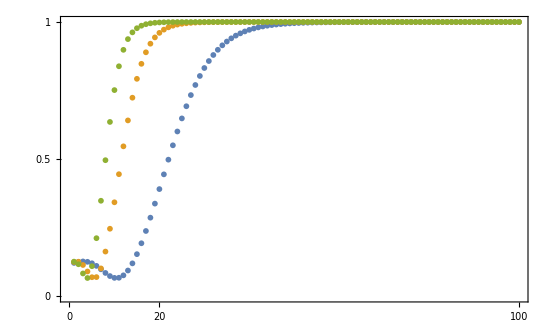

```mathematica
panelB=ListPlot[prob,
PlotRange->{0,1},
ImageSize->550,
FrameTicksStyle->20,
PlotStyle->PointSize[0.0075],
Frame->True,
AspectRatio->0.6,
FrameTicks->{{{0,0.5,1},None},{{0,20,100},None}}(*,
PlotLegends->Placed[Style[#,20]&/@rewardValues,{Left,Top}]*)
]
```

```mathematica
Export[myPATHexport<>"panelB.pdf",panelB];
```

### Fig. 9 (Impact of λ on unitary transformations)

#### How the fidelity between two effective unitary transformations scales with λ

```mathematica
nMaxLambdaGaps=3;

DIMbin=10;
minDIM=20;
maxDIM=70;

runMC=100;
gapsL={0.005,0.01,0.015};

fidelities=ConstantArray[{},nMaxLambdaGaps];

Monitor[
For[m=minDIM,m≤maxDIM,m+=DIMbin,

DIM=m;
nBS=BScount[DIM];
graphINFO=getGraph[DIM,Method->"Square2PS"];

For[gap=1,gap<=nMaxLambdaGaps,gap++,

AppendTo[fidelities⟦gap⟧,MeanAround@Table[
With[{cellPositions=graphINFO[[2,2;;-2]]},
powerValues=RandomVariate[UniformDistribution[{0,2π}],2nBS];
U1=getChipLambda[DIM,cellPositions,1.000-0.5gapsL⟦gap⟧,powerValues];
U2=getChipLambda[DIM,cellPositions,1.000+0.5gapsL⟦gap⟧,powerValues];
];
fidelity[U1,U2],
{run,runMC}
]
];

];
],{m,gap,run}
];
```

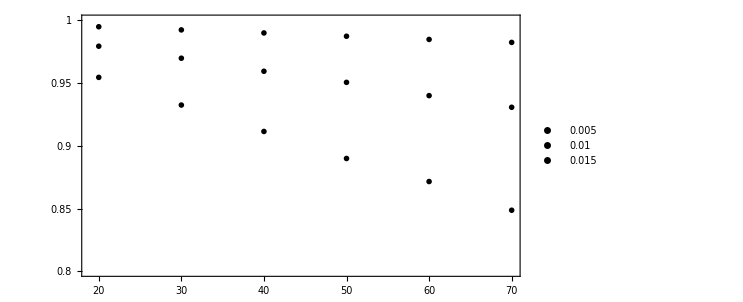

```mathematica
panelA=ListPlot[fidelities,
PlotRange->{All,{0.8,1}},
Frame->True,
ImageSize->550,
BaseStyle->20,
PlotStyle->Black,
PlotMarkers->"OpenMarkers",
PlotLegends->Placed[Style[#,18]&/@(gapsL),{Left,Bottom}],
AspectRatio->0.55,
FrameTicks->{{{0.75,0.8,0.85,0.9,0.95,1},None},{{{1,20},{2,30},{3,40},{4,50},{5,60},{6,70}},None}},
FrameTicksStyle->20
]
```

```mathematica
Export[myPATHexport<>"Panel9a.pdf",panelA]
```

C:\Users\fulvi\Desktop\ZenodoFiles\Panel9a.pdf

```mathematica
fidelitiesMEAN
fidelitiesSTD
```

{{0.994735,0.992216,0.989786,0.987164,0.984626,0.982262},{0.979227,0.969667,0.959289,0.950449,0.939878,0.930608},{0.954416,0.93238,0.911354,0.889834,0.871477,0.848628}}

{{0.0000692681,0.0000917385,0.0000868008,0.0000933571,0.000107246,0.000106279},{0.000283344,0.000300135,0.000380084,0.000365477,0.00038082,0.000394776},{0.000678295,0.000645999,0.000771523,0.000763692,0.000743747,0.000811203}}

#### Multiple λ on U

```mathematica
allLeakingNodesDIMS=Get[myPATHimport<>"allLeakingNodes2PSDIMS.txt"];
```

```mathematica
DIM=10;

graphINFO=getGraph[DIM,Method->"Square2PS"];
directedGraph=DeleteDuplicates@graphINFO⟦1⟧;

allLeakingNodes=allLeakingNodesDIMS⟦DIM⟧;

cellPositions=graphINFO⟦2,2;;-2⟧;

cellsUpara=Table[Join[#⟦s,k⟧,{1,Subscript[P, s,k,graphINFO⟦3,s+1,k⟧]}
],{s, Length@#},{k,Length[#⟦s⟧]}]&@cellPositions;

layersParaλ=Table[Normal@chipLayer[DIM,cellsUpara,layer],{λindex,3},{layer,Length@cellPositions}];

randomSettings=Table[RandomReal[{0,2π}],{s,Length@cellPositions},{k,Length[cellPositions⟦s⟧]}];

phaseSettingsInitialization=Table[
Subscript[P, s,k,graphINFO⟦3,s+1,k⟧] -># randomSettings⟦s,k⟧,{s,Length@cellPositions},{k,Length[cellPositions⟦s⟧]}]&/@{0.995,1,1.005};
```

```mathematica
Niterations=750;

phaseSettingsλ=phaseSettingsInitialization;

nodesLayer=graphINFO⟦3,2;;-2⟧;
posNodesInLayers=Table[Association[(nodesLayer⟦l,#⟧->#)&/@Range@Length@cellPositions⟦l⟧],{l,Length@cellPositions}];

fromNodetoLayer=Association@Flatten@Table[nodesLayer⟦l,i⟧->l,{l,Length@nodesLayer},{i,Length@nodesLayer⟦l⟧}];
updateCausalDiamondSequence=Table[
Sort[Join[(<|(#-> {x})&/@Range[Min@#,Max@#]&@Keys@#|>),#]&@GroupBy[allLeakingNodes⟦inMode,outMode,2⟧,fromNodetoLayer],#1>#2&]
,{inMode,DIM},{outMode,DIM}];
updateCDstartingLayer=Map[Min@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDfinalLayer=Map[Max@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDnodesLayerwise=Map[Values,updateCausalDiamondSequence,{2}];

ϕupdateINIT=0.025;
ϕupdateFIN=0.001;
ϕupdate=ϕupdateINIT;
ϕstep=(ϕupdateINIT-ϕupdateFIN)/Niterations;
ϕupdate-=ϕstep;

NsampledPairs=Floor@(DIM/2)-1;
inModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
outModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
possiblePairs=Sort[{inModes⟦#⟧,outModes⟦#⟧}&/@Range@NsampledPairs]

currentProbPercept2Action=ConstantArray[0.,{NsampledPairs,Niterations}];



Do[

{s,a}=RandomChoice[possiblePairs];
indexNextPair=Position[possiblePairs,{s,a}]⟦1,1⟧;

layersFixedλ=ConstantArray[{},3];

Table[
If[updateCDstartingLayer⟦s,a⟧≠1,
layersFixedλ⟦λindex⟧=Dot@@Reverse@Table[layersParaλ⟦λindex,layer⟧/.phaseSettingsλ⟦λindex,layer⟧,{layer,updateCDstartingLayer⟦s,a⟧-1}];,
layersFixedλ⟦λindex⟧=IdentityMatrix@DIM
],{λindex,3}
];
layersVariableλ=Table[layersParaλ⟦λindex,updateCDstartingLayer⟦s,a⟧;;⟧,{λindex,3}];

updateResult=updateCausalDiamondLambda[layersFixedλ,layersVariableλ,
updateCausalDiamondSequence⟦s,a⟧,updateCDstartingLayer⟦s,a⟧, updateCDfinalLayer⟦s,a⟧,
posNodesInLayers,phaseSettingsλ,ϕupdate,{s,a}];

phaseSettingsλ=updateResult⟦1⟧;
u=updateResult⟦2⟧;
currentProbPercept2Action⟦indexNextPair,iter⟧=(abs2@u⟦1,a,s⟧abs2@u⟦2,a,s⟧abs2@u⟦3,a,s⟧)^(1/3);
,

{iter,Niterations}
];
```

{{4,8},{6,4},{8,10},{10,2}}

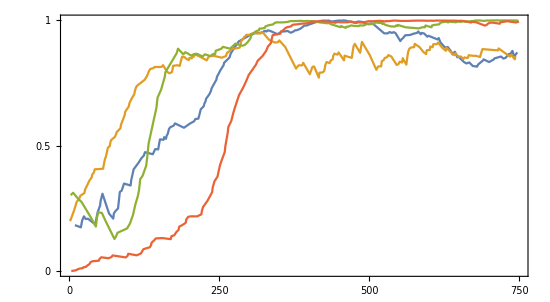

```mathematica
evolutionProbsPercept2ActionTMP=currentProbPercept2Action[[Position[possiblePairs,#]⟦1,1⟧]]&/@possiblePairs;
evolutionProbsPercept2Action=Table[If[evolutionProbsPercept2ActionTMP⟦pair,iter⟧≠0.,{iter,evolutionProbsPercept2ActionTMP⟦pair,iter⟧},Nothing],{pair,NsampledPairs},{iter,Niterations}];

panelB=ListPlot[evolutionProbsPercept2Action,
PlotRange->{{0,750},{0,1}},
ImageSize->550,
Frame->True,
Joined->True,
FrameTicksStyle->20,
AspectRatio->0.55,
FrameTicks->{{{0,0.5,1},None},{{0,250,500,750},None}}
]
```

```mathematica
Export[myPATHexport<>"Panel9b.pdf",panelB]
```

C:\Users\fulvi\Desktop\ZenodoFiles\Panel9b.pdf

```mathematica
evolutionProbsPercept2Action
phaseSettingsInitialization
```

{{{9,0.183844},{19,0.174975},{21,0.201033},{24,0.218767},{27,0.208451},{31,0.20912},{40,0.192134},{43,0.188097},{47,0.235421},{51,0.261501},{52,0.28075},{55,0.308875},{66,0.23},{73,0.209608},{74,0.230063},{77,0.240854},{81,0.250213},{82,0.271994},{83,0.294032},{84,0.31622},{87,0.320871},{89,0.334943},{91,0.349356},{102,0.34151},{103,0.362945},{105,0.384139},{107,0.405821},{115,0.431508},{120,0.450219},{124,0.460707},{126,0.474396},{139,0.465985},{143,0.48651},{148,0.485393},{149,0.499761},{150,0.513037},{151,0.525303},{157,0.523423},{158,0.534258},{161,0.527539},{162,0.538725},{164,0.547792},{165,0.557331},{166,0.566512},{168,0.573235},{174,0.580264},{176,0.588924},{191,0.571536},{201,0.588126},{208,0.597547},{210,0.606327},{215,0.607784},{217,0.625417},{218,0.635315},{219,0.64511},{224,0.657066},{225,0.667099},{227,0.67694},{228,0.687357},{232,0.700271},{234,0.707769},{236,0.718199},{237,0.728163},{245,0.762601},{246,0.773878},{248,0.783071},{250,0.792139},{252,0.801212},{257,0.820054},{258,0.830084},{267,0.851308},{269,0.866791},{272,0.878705},{274,0.885261},{275,0.8922},{278,0.89964},{281,0.908816},{282,0.914624},{298,0.936117},{301,0.941154},{310,0.948153},{318,0.94903},{324,0.952957},{325,0.957303},{329,0.954691},{330,0.958837},{334,0.957978},{347,0.944059},{351,0.949792},{354,0.956142},{356,0.954301},{361,0.955818},{364,0.956732},{369,0.949733},{372,0.952405},{374,0.955086},{375,0.957134},{376,0.95919},{379,0.959696},{385,0.965487},{386,0.967319},{389,0.972668},{391,0.976979},{392,0.978388},{396,0.978404},{397,0.979844},{398,0.980934},{399,0.981911},{406,0.987609},{410,0.99108},{411,0.991841},{412,0.992396},{413,0.992886},{414,0.99334},{415,0.993738},{418,0.996595},{420,0.996841},{423,0.998098},{431,0.997773},{432,0.998374},{438,0.994304},{441,0.99557},{443,0.996126},{445,0.99708},{448,0.997834},{450,0.998206},{451,0.998508},{454,0.997581},{456,0.99861},{457,0.998928},{460,0.998252},{477,0.989107},{478,0.991478},{480,0.993486},{482,0.994704},{490,0.992228},{493,0.987495},{496,0.98527},{500,0.983277},{502,0.985892},{503,0.987423},{505,0.984906},{506,0.98631},{525,0.947481},{531,0.947175},{534,0.952478},{538,0.94906},{541,0.952254},{544,0.948119},{552,0.916505},{553,0.921286},{557,0.929692},{558,0.933169},{559,0.936381},{560,0.93948},{569,0.941168},{573,0.945266},{580,0.949244},{581,0.952088},{582,0.954838},{586,0.943367},{587,0.946369},{588,0.949263},{592,0.946272},{597,0.933995},{599,0.937691},{614,0.923189},{616,0.928592},{619,0.91097},{626,0.892572},{630,0.889356},{631,0.893337},{637,0.874319},{639,0.863426},{640,0.867694},{643,0.874111},{647,0.852237},{648,0.856534},{655,0.840453},{658,0.833608},{662,0.827471},{667,0.831405},{673,0.817249},{680,0.814822},{681,0.819331},{682,0.823705},{690,0.839621},{691,0.84375},{700,0.833151},{708,0.843558},{709,0.847781},{720,0.855014},{724,0.846826},{728,0.850126},{729,0.854061},{732,0.861706},{733,0.865246},{736,0.866072},{738,0.87426},{739,0.877497},{742,0.854601},{746,0.868322},{747,0.871609}},{{1,0.199711},{4,0.218519},{8,0.244848},{12,0.276417},{16,0.287698},{18,0.300388},{25,0.312153},{26,0.325118},{30,0.344758},{33,0.360223},{37,0.373759},{38,0.385223},{41,0.394727},{42,0.405929},{56,0.408313},{57,0.421164},{58,0.43347},{59,0.445281},{61,0.458709},{62,0.469998},{63,0.48082},{64,0.491784},{67,0.497879},{68,0.509289},{69,0.520587},{71,0.525634},{76,0.535738},{79,0.554644},{85,0.569626},{86,0.584004},{88,0.596283},{90,0.608488},{92,0.621732},{93,0.635201},{95,0.642468},{99,0.656601},{100,0.66954},{104,0.688844},{108,0.704397},{109,0.716903},{111,0.732552},{113,0.739251},{125,0.761528},{129,0.7755},{133,0.799024},{135,0.805676},{140,0.808895},{142,0.813422},{152,0.813574},{154,0.814546},{156,0.820715},{163,0.794092},{167,0.788095},{171,0.793176},{172,0.806326},{173,0.818237},{177,0.819452},{180,0.820408},{184,0.817968},{185,0.828526},{186,0.837964},{187,0.846641},{188,0.854755},{192,0.852429},{196,0.844413},{199,0.841153},{200,0.849421},{204,0.847626},{205,0.855231},{207,0.85361},{209,0.862076},{212,0.860786},{216,0.856471},{229,0.839775},{231,0.849164},{233,0.856242},{241,0.857587},{254,0.850481},{261,0.856784},{263,0.870083},{266,0.8744},{271,0.885404},{279,0.888188},{284,0.890675},{285,0.901227},{286,0.910398},{287,0.918459},{290,0.925796},{291,0.931748},{294,0.93689},{295,0.941596},{300,0.941139},{304,0.946324},{307,0.94773},{309,0.950793},{313,0.946703},{315,0.947117},{319,0.947116},{320,0.950846},{323,0.949713},{333,0.921659},{335,0.91902},{343,0.910345},{346,0.911697},{348,0.912264},{350,0.91931},{360,0.892759},{378,0.807023},{382,0.819781},{388,0.819866},{390,0.829895},{401,0.784528},{405,0.812543},{408,0.815991},{416,0.770912},{417,0.790674},{422,0.791471},{425,0.797305},{426,0.810049},{427,0.822697},{429,0.833299},{434,0.82879},{436,0.839528},{439,0.843479},{440,0.85762},{442,0.866586},{447,0.862554},{449,0.871428},{458,0.839658},{459,0.858737},{465,0.853932},{471,0.849652},{472,0.866609},{473,0.88214},{474,0.896577},{476,0.905537},{485,0.869758},{486,0.886016},{487,0.900172},{488,0.913241},{501,0.860758},{512,0.802197},{515,0.815482},{520,0.815896},{521,0.836379},{524,0.840426},{526,0.849334},{530,0.852695},{532,0.860829},{537,0.855048},{546,0.821387},{549,0.825079},{551,0.834869},{555,0.831084},{556,0.848585},{562,0.822659},{563,0.841169},{564,0.858216},{565,0.873913},{567,0.886267},{570,0.891081},{575,0.89228},{576,0.905464},{584,0.892562},{591,0.871834},{595,0.864776},{596,0.880025},{601,0.880989},{602,0.89487},{606,0.892055},{607,0.904094},{613,0.904247},{615,0.910755},{622,0.889764},{628,0.87801},{629,0.889877},{635,0.875011},{642,0.8605},{644,0.868331},{649,0.854187},{653,0.855113},{657,0.844716},{659,0.851712},{663,0.849191},{665,0.850951},{666,0.860399},{669,0.859016},{674,0.857939},{678,0.857906},{685,0.853318},{686,0.861977},{687,0.870003},{688,0.877518},{689,0.884615},{715,0.879525},{716,0.887183},{735,0.854494},{737,0.862676},{743,0.844009},{744,0.857183}},{{2,0.303008},{6,0.312715},{15,0.287152},{20,0.276549},{36,0.212845},{44,0.17808},{45,0.19666},{46,0.215974},{48,0.235093},{54,0.232228},{60,0.201444},{75,0.128845},{78,0.140363},{80,0.153188},{96,0.1705},{101,0.190696},{106,0.224805},{110,0.267041},{114,0.29885},{116,0.322404},{117,0.344429},{118,0.366847},{122,0.380226},{128,0.420907},{130,0.460191},{131,0.484637},{132,0.508768},{138,0.574405},{145,0.650393},{146,0.671759},{147,0.691587},{153,0.724184},{159,0.774597},{160,0.792587},{179,0.868983},{181,0.886319},{190,0.86377},{193,0.872025},{197,0.867675},{203,0.858513},{206,0.862916},{211,0.86615},{214,0.864612},{222,0.854956},{226,0.86398},{235,0.856703},{240,0.865553},{243,0.864535},{244,0.878126},{253,0.885778},{256,0.893522},{268,0.886381},{277,0.906757},{288,0.898181},{292,0.900474},{297,0.911588},{302,0.927358},{303,0.938165},{306,0.944793},{308,0.949753},{312,0.956522},{316,0.959362},{317,0.96655},{321,0.966614},{326,0.969086},{327,0.975073},{332,0.979377},{340,0.983141},{341,0.986263},{342,0.988594},{344,0.98963},{345,0.991513},{349,0.990923},{355,0.990972},{358,0.991581},{362,0.992155},{365,0.993366},{366,0.994536},{367,0.995302},{368,0.995907},{377,0.996475},{380,0.99647},{383,0.996637},{384,0.997259},{393,0.995913},{394,0.996812},{407,0.995555},{419,0.99039},{424,0.989557},{428,0.987677},{433,0.98784},{435,0.985588},{437,0.983121},{452,0.971976},{453,0.976112},{461,0.96915},{462,0.972444},{463,0.974471},{466,0.974111},{467,0.976009},{470,0.978893},{475,0.976824},{483,0.976482},{484,0.979019},{491,0.978607},{492,0.98039},{495,0.983015},{498,0.986016},{504,0.983861},{508,0.986237},{509,0.988377},{511,0.990777},{514,0.989592},{518,0.988957},{519,0.991036},{522,0.985061},{523,0.987645},{527,0.981048},{536,0.975038},{543,0.974419},{545,0.978563},{547,0.976774},{548,0.980842},{550,0.979183},{561,0.971326},{583,0.967106},{585,0.968635},{589,0.971827},{593,0.971337},{594,0.978647},{604,0.971488},{605,0.978678},{608,0.980541},{617,0.983345},{618,0.987897},{621,0.99135},{623,0.991847},{627,0.993933},{632,0.990972},{634,0.993774},{638,0.993067},{645,0.991398},{646,0.994534},{651,0.99354},{654,0.993218},{656,0.995661},{661,0.993164},{664,0.994393},{668,0.995024},{671,0.996342},{675,0.996352},{676,0.997829},{677,0.998624},{683,0.998434},{684,0.998794},{692,0.996808},{694,0.997666},{695,0.998388},{697,0.998458},{699,0.998406},{702,0.998352},{703,0.998722},{704,0.998831},{705,0.998887},{707,0.998706},{710,0.99886},{711,0.998905},{712,0.998905},{713,0.998905},{714,0.998905},{717,0.998621},{721,0.998667},{722,0.998841},{725,0.998775},{726,0.998916},{731,0.998639},{734,0.998859},{740,0.998328},{741,0.998855},{749,0.998031}},{{3,0.00114257},{5,0.00177516},{7,0.00250382},{10,0.00355607},{11,0.00483861},{13,0.00652634},{14,0.0084723},{17,0.0107323},{22,0.0125974},{23,0.0155218},{28,0.0183334},{29,0.022064},{32,0.0262295},{34,0.0310204},{35,0.0364296},{39,0.0403937},{49,0.0422301},{50,0.048927},{53,0.0557817},{65,0.0521446},{70,0.0566132},{72,0.0632135},{94,0.0552078},{97,0.0616926},{98,0.069863},{112,0.0636238},{119,0.0707597},{121,0.0782916},{123,0.0872658},{127,0.0909179},{134,0.0956251},{136,0.103677},{137,0.114085},{141,0.122424},{144,0.130931},{155,0.132262},{169,0.128052},{170,0.13951},{175,0.14359},{178,0.155344},{182,0.164773},{183,0.177627},{189,0.185095},{194,0.193491},{195,0.207176},{198,0.216657},{202,0.218889},{213,0.2187},{220,0.226755},{221,0.241432},{223,0.256691},{230,0.279778},{238,0.315062},{239,0.33399},{242,0.358894},{247,0.377137},{249,0.400251},{251,0.421532},{255,0.449039},{259,0.474528},{260,0.497449},{262,0.524703},{264,0.551784},{265,0.574417},{270,0.598856},{273,0.627903},{276,0.651787},{280,0.681062},{283,0.702174},{289,0.727892},{293,0.747664},{296,0.764058},{299,0.781584},{305,0.801811},{311,0.822297},{314,0.838265},{322,0.856817},{328,0.877281},{331,0.894623},{336,0.908464},{337,0.920275},{338,0.930936},{339,0.940268},{352,0.946046},{353,0.954632},{357,0.960218},{359,0.966131},{363,0.971783},{370,0.975219},{371,0.979001},{373,0.981837},{381,0.983588},{387,0.985794},{395,0.987155},{400,0.988453},{402,0.991505},{403,0.992933},{404,0.993927},{409,0.994655},{421,0.995454},{430,0.994485},{444,0.989406},{446,0.992395},{455,0.991222},{464,0.991469},{468,0.993094},{469,0.995214},{479,0.988406},{481,0.991394},{489,0.990196},{494,0.992966},{497,0.994605},{499,0.995627},{507,0.995568},{510,0.996359},{513,0.996595},{516,0.996729},{517,0.997528},{528,0.994556},{529,0.996728},{533,0.99588},{535,0.996855},{539,0.9974},{540,0.997947},{542,0.998271},{554,0.996822},{566,0.996915},{568,0.997275},{571,0.99742},{572,0.99767},{574,0.997839},{577,0.997714},{578,0.997941},{579,0.998108},{590,0.998121},{598,0.99733},{600,0.997712},{603,0.997691},{609,0.997477},{610,0.997948},{611,0.998216},{612,0.998356},{620,0.998025},{624,0.997969},{625,0.998221},{633,0.997774},{636,0.997792},{641,0.997998},{650,0.996785},{652,0.99752},{660,0.99603},{670,0.990337},{672,0.993237},{679,0.991054},{693,0.978224},{696,0.980826},{698,0.985588},{701,0.989673},{706,0.989967},{718,0.985757},{719,0.991407},{723,0.992987},{727,0.994334},{730,0.995754},{745,0.990542},{748,0.992877},{750,0.994205}}}

{{{P_(1,1,11)→3.18348,P_(1,2,12)→4.2447,P_(1,3,13)→0.431877,P_(1,4,14)→0.890309,P_(1,5,15)→4.98219},{P_(2,1,16)→2.47974,P_(2,2,17)→2.87025,P_(2,3,18)→4.51863,P_(2,4,19)→5.8311,P_(2,5,20)→1.1777},{P_(3,1,21)→4.78786,P_(3,2,22)→5.09177,P_(3,3,23)→4.71666,P_(3,4,24)→2.92171},{P_(4,1,25)→4.8022,P_(4,2,26)→0.35531,P_(4,3,27)→4.41238,P_(4,4,28)→2.88983},{P_(5,1,29)→4.47584,P_(5,2,30)→5.68718,P_(5,3,31)→4.45085,P_(5,4,32)→5.12047,P_(5,5,33)→2.57418},{P_(6,1,34)→5.18533,P_(6,2,35)→4.13223,P_(6,3,36)→5.26622,P_(6,4,37)→5.29365,P_(6,5,38)→4.7268},{P_(7,1,39)→4.23315,P_(7,2,40)→0.554272,P_(7,3,41)→0.0581213,P_(7,4,42)→5.98798},{P_(8,1,43)→1.30614,P_(8,2,44)→5.44564,P_(8,3,45)→1.45191,P_(8,4,46)→5.25949},{P_(9,1,47)→5.55551,P_(9,2,48)→4.35894,P_(9,3,49)→4.92921,P_(9,4,50)→4.58002,P_(9,5,51)→3.28897},{P_(10,1,52)→4.05326,P_(10,2,53)→4.3364,P_(10,3,54)→5.55392,P_(10,4,55)→5.76836,P_(10,5,56)→2.67301},{P_(11,1,57)→4.37054,P_(11,2,58)→5.80122,P_(11,3,59)→2.32244,P_(11,4,60)→2.85112},{P_(12,1,61)→1.95469,P_(12,2,62)→2.74042,P_(12,3,63)→0.9988,P_(12,4,64)→1.1251},{P_(13,1,65)→2.86624,P_(13,2,66)→3.32484,P_(13,3,67)→2.33394,P_(13,4,68)→2.44285,P_(13,5,69)→4.22724},{P_(14,1,70)→4.54432,P_(14,2,71)→6.06165,P_(14,3,72)→5.39524,P_(14,4,73)→5.78074,P_(14,5,74)→5.27941},{P_(15,1,75)→1.95035,P_(15,2,76)→2.57693,P_(15,3,77)→0.089588,P_(15,4,78)→0.897564},{P_(16,1,79)→4.02234,P_(16,2,80)→2.96761,P_(16,3,81)→3.97242,P_(16,4,82)→3.8776},{P_(17,1,83)→1.98632,P_(17,2,84)→4.99246,P_(17,3,85)→6.16261,P_(17,4,86)→4.10272,P_(17,5,87)→3.6724},{P_(18,1,88)→5.99646,P_(18,2,89)→4.36352,P_(18,3,90)→5.84251,P_(18,4,91)→4.8963,P_(18,5,92)→5.19978},{P_(19,1,93)→5.17908,P_(19,2,94)→3.65128,P_(19,3,95)→3.02465,P_(19,4,96)→0.27194},{P_(20,1,97)→5.47417,P_(20,2,98)→3.85253,P_(20,3,99)→4.64172,P_(20,4,100)→3.6515}},{{P_(1,1,11)→3.19948,P_(1,2,12)→4.26603,P_(1,3,13)→0.434047,P_(1,4,14)→0.894783,P_(1,5,15)→5.00722},{P_(2,1,16)→2.4922,P_(2,2,17)→2.88468,P_(2,3,18)→4.54134,P_(2,4,19)→5.8604,P_(2,5,20)→1.18362},{P_(3,1,21)→4.81192,P_(3,2,22)→5.11736,P_(3,3,23)→4.74036,P_(3,4,24)→2.93639},{P_(4,1,25)→4.82633,P_(4,2,26)→0.357095,P_(4,3,27)→4.43455,P_(4,4,28)→2.90436},{P_(5,1,29)→4.49834,P_(5,2,30)→5.71576,P_(5,3,31)→4.47322,P_(5,4,32)→5.1462,P_(5,5,33)→2.58712},{P_(6,1,34)→5.21139,P_(6,2,35)→4.15299,P_(6,3,36)→5.29269,P_(6,4,37)→5.32025,P_(6,5,38)→4.75055},{P_(7,1,39)→4.25442,P_(7,2,40)→0.557057,P_(7,3,41)→0.0584134,P_(7,4,42)→6.01807},{P_(8,1,43)→1.3127,P_(8,2,44)→5.47301,P_(8,3,45)→1.4592,P_(8,4,46)→5.28592},{P_(9,1,47)→5.58343,P_(9,2,48)→4.38085,P_(9,3,49)→4.95398,P_(9,4,50)→4.60303,P_(9,5,51)→3.3055},{P_(10,1,52)→4.07363,P_(10,2,53)→4.35819,P_(10,3,54)→5.58183,P_(10,4,55)→5.79735,P_(10,5,56)→2.68644},{P_(11,1,57)→4.3925,P_(11,2,58)→5.83037,P_(11,3,59)→2.33411,P_(11,4,60)→2.86545},{P_(12,1,61)→1.96452,P_(12,2,62)→2.75419,P_(12,3,63)→1.00382,P_(12,4,64)→1.13076},{P_(13,1,65)→2.88064,P_(13,2,66)→3.34155,P_(13,3,67)→2.34566,P_(13,4,68)→2.45513,P_(13,5,69)→4.24849},{P_(14,1,70)→4.56716,P_(14,2,71)→6.09211,P_(14,3,72)→5.42235,P_(14,4,73)→5.80979,P_(14,5,74)→5.30594},{P_(15,1,75)→1.96015,P_(15,2,76)→2.58988,P_(15,3,77)→0.0900382,P_(15,4,78)→0.902074},{P_(16,1,79)→4.04255,P_(16,2,80)→2.98252,P_(16,3,81)→3.99238,P_(16,4,82)→3.89709},{P_(17,1,83)→1.9963,P_(17,2,84)→5.01755,P_(17,3,85)→6.19358,P_(17,4,86)→4.12334,P_(17,5,87)→3.69086},{P_(18,1,88)→6.02659,P_(18,2,89)→4.38544,P_(18,3,90)→5.87187,P_(18,4,91)→4.9209,P_(18,5,92)→5.22591},{P_(19,1,93)→5.2051,P_(19,2,94)→3.66962,P_(19,3,95)→3.03985,P_(19,4,96)→0.273306},{P_(20,1,97)→5.50168,P_(20,2,98)→3.87189,P_(20,3,99)→4.66505,P_(20,4,100)→3.66985}},{{P_(1,1,11)→3.21548,P_(1,2,12)→4.28736,P_(1,3,13)→0.436217,P_(1,4,14)→0.899257,P_(1,5,15)→5.03226},{P_(2,1,16)→2.50466,P_(2,2,17)→2.8991,P_(2,3,18)→4.56405,P_(2,4,19)→5.8897,P_(2,5,20)→1.18954},{P_(3,1,21)→4.83598,P_(3,2,22)→5.14295,P_(3,3,23)→4.76406,P_(3,4,24)→2.95107},{P_(4,1,25)→4.85046,P_(4,2,26)→0.358881,P_(4,3,27)→4.45672,P_(4,4,28)→2.91888},{P_(5,1,29)→4.52083,P_(5,2,30)→5.74434,P_(5,3,31)→4.49558,P_(5,4,32)→5.17193,P_(5,5,33)→2.60006},{P_(6,1,34)→5.23744,P_(6,2,35)→4.17376,P_(6,3,36)→5.31915,P_(6,4,37)→5.34685,P_(6,5,38)→4.77431},{P_(7,1,39)→4.2757,P_(7,2,40)→0.559843,P_(7,3,41)→0.0587054,P_(7,4,42)→6.04816},{P_(8,1,43)→1.31927,P_(8,2,44)→5.50037,P_(8,3,45)→1.4665,P_(8,4,46)→5.31235},{P_(9,1,47)→5.61135,P_(9,2,48)→4.40275,P_(9,3,49)→4.97875,P_(9,4,50)→4.62605,P_(9,5,51)→3.32203},{P_(10,1,52)→4.094,P_(10,2,53)→4.37998,P_(10,3,54)→5.60974,P_(10,4,55)→5.82633,P_(10,5,56)→2.69987},{P_(11,1,57)→4.41446,P_(11,2,58)→5.85952,P_(11,3,59)→2.34578,P_(11,4,60)→2.87977},{P_(12,1,61)→1.97434,P_(12,2,62)→2.76796,P_(12,3,63)→1.00884,P_(12,4,64)→1.13641},{P_(13,1,65)→2.89505,P_(13,2,66)→3.35826,P_(13,3,67)→2.35739,P_(13,4,68)→2.4674,P_(13,5,69)→4.26973},{P_(14,1,70)→4.58999,P_(14,2,71)→6.12257,P_(14,3,72)→5.44946,P_(14,4,73)→5.83884,P_(14,5,74)→5.33247},{P_(15,1,75)→1.96995,P_(15,2,76)→2.60283,P_(15,3,77)→0.0904884,P_(15,4,78)→0.906584},{P_(16,1,79)→4.06277,P_(16,2,80)→2.99743,P_(16,3,81)→4.01234,P_(16,4,82)→3.91657},{P_(17,1,83)→2.00629,P_(17,2,84)→5.04264,P_(17,3,85)→6.22454,P_(17,4,86)→4.14396,P_(17,5,87)→3.70931},{P_(18,1,88)→6.05672,P_(18,2,89)→4.40737,P_(18,3,90)→5.90123,P_(18,4,91)→4.9455,P_(18,5,92)→5.25204},{P_(19,1,93)→5.23113,P_(19,2,94)→3.68797,P_(19,3,95)→3.05505,P_(19,4,96)→0.274673},{P_(20,1,97)→5.52919,P_(20,2,98)→3.89125,P_(20,3,99)→4.68837,P_(20,4,100)→3.6882}}}

### Fig. 10 (Partial traceability)

```mathematica
(*minDIM=1;
maxDIM=30;
allLeakingNodesDIMS=ConstantArray[{},{1+maxDIM-minDIM}];
DIMindex=0;

Do[
DIMindex++;
graphINFO=getGraph[DIM,Method->"Square2PS"];
directedGraph=DeleteDuplicates@graphINFO⟦1⟧;
nVertices=VertexCount@directedGraph;
allLeakingNodesDIMS⟦DIMindex⟧=Table[findLeakingNodes[DIM,graphINFO,inMode,nVertices-DIM+outMode],{inMode,DIM},{outMode,DIM}];
,{DIM,minDIM,maxDIM}
];

Put[allLeakingNodesDIMS,myPATHexport<>"allLeakingNodes2PSDIMS.txt"]*)
```

```mathematica
allLeakingNodesDIMS=Get[myPATHimport<>"allLeakingNodes2PSDIMS.txt"];
```

```mathematica
DIM=21;

graphINFO=getGraph[DIM,Method->"Square2PS"];
directedGraph=DeleteDuplicates@graphINFO⟦1⟧;

allLeakingNodes=allLeakingNodesDIMS⟦DIM⟧;

cellPositions=graphINFO⟦2,2;;-2⟧;

cellsUpara=Table[
Join[#⟦s,k⟧,{1,Subscript[P, s,k,graphINFO⟦3,s+1,k⟧]}]
,{s, Length@#},{k,Length[#⟦s⟧]}]&@cellPositions;

layersPara=Table[Normal@chipLayer[DIM,cellsUpara,layer],{layer,Length@cellPositions}];

phaseSettingsInitialization=Map[(#->RandomReal[{0,2π}])&,Table[
Subscript[P, s,k,graphINFO⟦3,s+1,k⟧] ,{s,Length@cellPositions},{k,Length[cellPositions⟦s⟧]}],{2}
];
```

```mathematica
Niterations=601;

phaseSettings=phaseSettingsInitialization;

nodesLayer=graphINFO⟦3,2;;-2⟧;
posNodesInLayers=Table[Association[(nodesLayer⟦l,#⟧->#)&/@Range@Length@cellPositions⟦l⟧],{l,Length@cellPositions}];

fromNodetoLayer=Association@Flatten@Table[nodesLayer⟦l,i⟧->l,{l,Length@nodesLayer},{i,Length@nodesLayer⟦l⟧}];
updateCausalDiamondSequence=Table[
Sort[Join[(<|(#-> {x})&/@Range[Min@#,Max@#]&@Keys@#|>),#]&@GroupBy[allLeakingNodes⟦inMode,outMode,1⟧,fromNodetoLayer],#1>#2&]
,{inMode,DIM},{outMode,DIM}];
updateCDstartingLayer=Map[Min@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDfinalLayer=Map[Max@Keys@#&,updateCausalDiamondSequence,{2}];
updateCDnodesLayerwise=Map[Values,updateCausalDiamondSequence,{2}];


ϕupdateINIT=0.03;
ϕupdateFIN=0.0025;
ϕupdate=ϕupdateINIT;
ϕstep=(ϕupdateINIT-ϕupdateFIN)/Niterations;
ϕupdate-=ϕstep;

NsampledPairs=3(*Floor@(DIM/2)*);
inModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
outModes=2RandomSample[Range@Floor@(DIM/2),NsampledPairs];
possiblePairs=Sort[{inModes⟦#⟧,outModes⟦#⟧}&/@Range@NsampledPairs]

currentProbPercept2Action=ConstantArray[0.,{NsampledPairs,Niterations}];

NiterationsHowManySteps=2;
NiterationsSteps={1,600}(*1+Round/@Subdivide[Niterations,NiterationsHowManySteps]*);
partialProbs=ConstantArray[{},{NsampledPairs,NiterationsHowManySteps,Round[Length@layersPara/2]}];
cont=0;


Do[

{s,a}=RandomChoice[possiblePairs];
indexNextPair=Position[possiblePairs,{s,a}]⟦1,1⟧;

init=IdentityMatrix@DIM;

If[MemberQ[NiterationsSteps,iter],
cont++;
Print[iter," ",cont];

Do[
layerValued=layersPara⟦layer⟧/.phaseSettings⟦layer⟧;
partialU=layerValued.init;
If[EvenQ@layer,
Table[partialProbs⟦pair,cont,Round[layer/2]⟧=abs2@partialU⟦;;,possiblePairs⟦pair,1⟧⟧,{pair,NsampledPairs}];
];
init=partialU;
,{layer,1,Length@layersPara}
];
,

None
];


If[updateCDstartingLayer⟦s,a⟧≠1,
layersFixed=Dot@@Reverse@Table[layersPara⟦layer⟧/.phaseSettings⟦layer⟧,{layer,updateCDstartingLayer⟦s,a⟧-1}];,
layersFixed=IdentityMatrix@DIM
];
layersVariable=layersPara⟦updateCDstartingLayer⟦s,a⟧;;⟧;

updateResult=updateCausalDiamond[layersFixed,layersVariable,
updateCausalDiamondSequence⟦s,a⟧,updateCDstartingLayer⟦s,a⟧, updateCDfinalLayer⟦s,a⟧,
posNodesInLayers,phaseSettings,ϕupdate,{s,a}];

phaseSettings=updateResult⟦1⟧;
u=updateResult⟦2⟧;
currentProbPercept2Action⟦indexNextPair,iter⟧=abs2@u⟦a,s⟧;
,

{iter,Niterations}
];
```

{{12,18},{16,6},{18,20}}

1 1

600 2

```mathematica
FigTrace=GraphicsRow[
Table[
GraphicsColumn[
barChart3D[#]&/@(2partialProbs[[pair]]),
ImageSize->700,
Spacings->{0,0}
],{pair,NsampledPairs}],
Spacings->50,
ImageSize->1300
]
```

-Graphics-

```mathematica
Export[myPATHexport<>"FigTrace.pdf",FigTrace];
```